```mathematica
(*
movement1004
update from 0925:
from 1 cell generalize to all KTs


101723
spindel location calculation

110223
spindle metaphase plate calculation
*)
```

```mathematica
control=Import["C:\\Users\\taoji\\OneDrive - UCSF\\Desktop\\New folder\\moviesearch\\controlXYnew0926.csv"];
```

```mathematica
tsa=Import["C:\\Users\\taoji\\OneDrive - UCSF\\Desktop\\New folder\\moviesearch\\TSAXYnew0926.csv"];
```

```mathematica
channalchosefunc[channel_]:=If[channel==1,20,41];
```

```mathematica
inputpathgenerate[datainput_,channel_,index_]:=Module[{movementfolder,movementpath},
movementfolder=DirectoryName[DirectoryName[DirectoryName[DirectoryName[DirectoryName[AbsoluteFileName[Select[FileNames[All,{DirectoryName[DirectoryName[DirectoryName[DirectoryName[AbsoluteFileName[datainput[[index]][[channalchosefunc[channel]]]]]]]]}],StringEndsQ[#,"_"<>ToString[datainput[[index]][[6]]-1]<>".tif"]&][[1]]]]]]]];
movementpath=movementfolder<>"export.csv"
];
```

```mathematica
inputfoldergenerate[datainput_,channel_,index_]:=Module[{movementfolder,movementpath},
movementfolder=DirectoryName[DirectoryName[DirectoryName[DirectoryName[DirectoryName[AbsoluteFileName[Select[FileNames[All,{DirectoryName[DirectoryName[DirectoryName[DirectoryName[AbsoluteFileName[datainput[[index]][[channalchosefunc[channel]]]]]]]]}],StringEndsQ[#,"_"<>ToString[datainput[[index]][[6]]-1]<>".tif"]&][[1]]]]]]]];
movementfolder
];
```

```mathematica
controlallmovepath=DeleteDuplicates[Flatten[Table[Table[inputpathgenerate[control,channel,i],{i,2,Length[control]}],{channel,1,2}]]];
controlallmovefolder=DeleteDuplicates[Flatten[Table[Table[inputfoldergenerate[control,channel,i],{i,2,Length[control]}],{channel,1,2}]]];
```

```mathematica
tsaallmovepath=DeleteDuplicates[Flatten[Table[Table[inputpathgenerate[tsa,channel,i],{i,2,Length[tsa]}],{channel,1,2}]]];
tsaallmovefolder=DeleteDuplicates[Flatten[Table[Table[inputfoldergenerate[tsa,channel,i],{i,2,Length[tsa]}],{channel,1,2}]]];
```

```mathematica
datagenerate[movementfolder_]:=Module[{movementpath,sisterpath,trackingPath,pairpath,exportpath0,exportpath1,exportpath2,table,trackLabels,data,tracklabeltoID,pairTablle,trackIDs,time,collectsort,prepair,pair,overlap,xpairs,xpairsWithFrame,ypairs,ypairsWithFrame,zpairs,zpairsWithFrame,xyzpositionsindex,xypositionsindex,xpositions,ypositions,zpositions,xpositionsWithTime,ypositionsWithTime,zpositionsWithTime,XYZwithFrame,FunctionXYZwithFrames,FunctionXYZwithFramesNumberOnly,lengththreashold,ktgather,filterktgather,example,timegather,totaltime,ktsX,ktsY,ktsZ,ktsXYZ,centert,folder,oldexample,metaplate,metaplateRegion},


movementpath=movementfolder<>"export.csv";
sisterpath=movementfolder<>"pairs.xlsx";
trackingPath=movementpath;
pairpath=sisterpath;

exportpath0=movementfolder;
exportpath1=exportpath0<>"\\ch1\\";
exportpath2=exportpath0<>"\\ch2\\";
table=Import[trackingPath];
trackLabels=
Flatten[Import[pairpath],1];
data=Drop[table,4];
tracklabeltoID[x_]:=Flatten[Select[data,#[[1]]=="Track_"<>ToString[IntegerPart[x]]&,1]][[3]];
pairTablle=
Map[tracklabeltoID,trackLabels,{2}];
trackIDs=Max[Transpose[data][[3]]] ;
time=Max[Transpose[data][[9]]];(* length of the movie *)
collectsort=Table[Sort[Select[data,#[[3]]==id&],#1[[9]]<#2[[9]]&],{id,0,trackIDs}];(*categorize and sort spots data by ID and time *)
prepair= Table[{{ii,jj,tt},{Select[collectsort[[ii]],#[[9]]==tt-1&],Select[collectsort[[jj]],#[[9]]==tt-1&]}},{ii,1,trackIDs+1},{jj,1,trackIDs+1},{tt,1,time+1}];(*pair all possible KTs *)

pair[reali_,realj_,realt_]:=prepair[[reali+1,realj+1,realt+1]];(*transfer between different index system, FIJI use index from 0, Mathematica use from 1, so need to +1 *)
overlap[reali_,realj_,realt_]:=ContainsNone[pair[reali,realj,realt][[2]],{{}}];(*decide if KT i,j are both trackable at time t *)

overlap[reali_,realj_]:=Select[Range[0,time],overlap[reali,realj,#]==True&] ;(*decide how much time overlap between two possible sister KT pairs *)

xpairs=Table[
{Select[
collectsort[[ii]],#[[9]]==realt&][[1]][[5]],Select[
collectsort[[jj]],#[[9]]==realt&][[1]][[5]]}
,{ii,trackIDs+1},{jj,trackIDs+1},{realt,overlap[ii-1,jj-1]}];
xpairsWithFrame=Table[
{Select[
collectsort[[ii]],#[[9]]==realt&][[1]][[5]],Select[
collectsort[[jj]],#[[9]]==realt&][[1]][[5]],{"frame=",Select[
collectsort[[jj]],#[[9]]==realt&][[1]][[9]]}}
,{ii,trackIDs+1},{jj,trackIDs+1},{realt,overlap[ii-1,jj-1]}];

ypairs=Table[
{Select[
collectsort[[ii]],#[[9]]==realt&][[1]][[6]],Select[
collectsort[[jj]],#[[9]]==realt&][[1]][[6]]}
,{ii,trackIDs+1},{jj,trackIDs+1},{realt,overlap[ii-1,jj-1]}];

ypairsWithFrame=Table[
{Select[
collectsort[[ii]],#[[9]]==realt&][[1]][[6]],Select[
collectsort[[jj]],#[[9]]==realt&][[1]][[6]],{"frame=",Select[
collectsort[[jj]],#[[9]]==realt&][[1]][[9]]}}
,{ii,trackIDs+1},{jj,trackIDs+1},{realt,overlap[ii-1,jj-1]}];

zpairs=Table[
{Select[
collectsort[[ii]],#[[9]]==realt&][[1]][[7]],Select[
collectsort[[jj]],#[[9]]==realt&][[1]][[7]]}
,{ii,trackIDs+1},{jj,trackIDs+1},{realt,overlap[ii-1,jj-1]}];
zpairsWithFrame=Table[
{Select[
collectsort[[ii]],#[[9]]==realt&][[1]][[7]],Select[
collectsort[[jj]],#[[9]]==realt&][[1]][[7]],{"frame=",Select[
collectsort[[jj]],#[[9]]==realt&][[1]][[9]]}}
,{ii,trackIDs+1},{jj,trackIDs+1},{realt,overlap[ii-1,jj-1]}];
(*
Catrgorize postions of KTs by track IDs and time
*)
xyzpositionsindex=Table[{{ii-1},Sort[collectsort[[ii]],#1[[9]]<#2[[9]]&][[jj]][[9]],{Sort[collectsort[[ii]],#1[[9]]<#2[[9]]&][[jj]][[5]],Sort[collectsort[[ii]],#1[[9]]<#2[[9]]&][[jj]][[6]], (* sort by time *) Sort[collectsort[[ii]],#1[[9]]<#2[[9]]&][[jj]][[7]]}},{ii,trackIDs+1},{jj,Length[collectsort[[ii]]]}];

xypositionsindex=Table[{{ii-1},Sort[collectsort[[ii]],#1[[9]]<#2[[9]]&][[jj]][[9]],{Sort[collectsort[[ii]],#1[[9]]<#2[[9]]&][[jj]][[5]],Sort[collectsort[[ii]],#1[[9]]<#2[[9]]&][[jj]][[6]]}},{ii,trackIDs+1},{jj,Length[collectsort[[ii]]]}];

xpositions=Table[Sort[collectsort[[ii]],#1[[9]]<#2[[9]]&][[jj]][[5]],{ii,trackIDs+1},{jj,Length[collectsort[[ii]]]}];
ypositions=Table[Sort[collectsort[[ii]],#1[[9]]<#2[[9]]&][[jj]][[6]],{ii,trackIDs+1},{jj,Length[collectsort[[ii]]]}];
zpositions=Table[Sort[collectsort[[ii]],#1[[9]]<#2[[9]]&][[jj]][[7]],{ii,trackIDs+1},{jj,Length[collectsort[[ii]]]}];
xpositionsWithTime=Table[{Sort[collectsort[[ii]],#1[[9]]<#2[[9]]&][[jj]][[5]],{"frame=",Sort[collectsort[[ii]],#1[[9]]<#2[[9]]&][[jj]][[9]]}},{ii,trackIDs+1},{jj,Length[collectsort[[ii]]]}];
ypositionsWithTime=Table[{Sort[collectsort[[ii]],#1[[9]]<#2[[9]]&][[jj]][[6]],{"frame=",Sort[collectsort[[ii]],#1[[9]]<#2[[9]]&][[jj]][[9]]}},{ii,trackIDs+1},{jj,Length[collectsort[[ii]]]}];
zpositionsWithTime=Table[{Sort[collectsort[[ii]],#1[[9]]<#2[[9]]&][[jj]][[7]],{"frame=",Sort[collectsort[[ii]],#1[[9]]<#2[[9]]&][[jj]][[9]]}},{ii,trackIDs+1},{jj,Length[collectsort[[ii]]]}];


(*
collect KTxyzsisterdata
*)

xpairsWithFrame=Table[
{Select[
collectsort[[ii]],#[[9]]==realt&][[1]][[5]],Select[
collectsort[[jj]],#[[9]]==realt&][[1]][[5]],{"frame=",Select[
collectsort[[jj]],#[[9]]==realt&][[1]][[9]]}}
,{ii,trackIDs+1},{jj,trackIDs+1},{realt,overlap[ii-1,jj-1]}];
ypairsWithFrame=Table[
{Select[
collectsort[[ii]],#[[9]]==realt&][[1]][[6]],Select[
collectsort[[jj]],#[[9]]==realt&][[1]][[6]],{"frame=",Select[
collectsort[[jj]],#[[9]]==realt&][[1]][[9]]}}
,{ii,trackIDs+1},{jj,trackIDs+1},{realt,overlap[ii-1,jj-1]}];
zpairsWithFrame=Table[
{Select[
collectsort[[ii]],#[[9]]==realt&][[1]][[7]],Select[
collectsort[[jj]],#[[9]]==realt&][[1]][[7]],{"frame=",Select[
collectsort[[jj]],#[[9]]==realt&][[1]][[9]]}}
,{ii,trackIDs+1},{jj,trackIDs+1},{realt,overlap[ii-1,jj-1]}];

XYZwithFrame=Table[If[Transpose[xpairs[[ii,ii]]]=={},{},Transpose[{(Transpose[xpairs[[ii,ii]]][[1]]),(Transpose[ypairs[[ii,ii]]][[1]]),(Transpose[zpairs[[ii,ii]]][[1]]),Transpose[xpairsWithFrame[[ii,ii]]][[3]]}]],{ii,trackIDs+1}];
FunctionXYZwithFrames[reali_]:=XYZwithFrame[[reali+1]];
FunctionXYZwithFramesNumberOnly[reali_]:=Transpose[{Transpose[FunctionXYZwithFrames[reali]][[1]],Transpose[FunctionXYZwithFrames[reali]][[2]],Transpose[FunctionXYZwithFrames[reali]][[3]],1+Transpose[Transpose[FunctionXYZwithFrames[reali]][[4]]][[2]]}];





(*

spindle movement calculation
to be add here

*)


(*
add extra steps to filter by tracking time to solve the problem from noise
*)

oldexample=data;
lengththreashold=5;
ktgather=GatherBy[oldexample,#[[3]]&];

filterktgather=Select[ktgather,Length[#]>lengththreashold&];
example=Flatten[filterktgather,1];


folder=movementfolder;


timegather=GroupBy[example,#[[9]]&];
totaltime=Max[Transpose[example][[9]]];
ktsX=Table[Transpose[timegather[t]][[5]],{t,totaltime}];
ktsY=Table[Transpose[timegather[t]][[6]],{t,totaltime}];
ktsZ=Table[Transpose[timegather[t]][[7]],{t,totaltime}];
ktsXYZ=Table[Transpose[{Transpose[timegather[t]][[5]],Transpose[timegather[t]][[6]],Transpose[timegather[t]][[7]]}],{t,totaltime}];
centert=Table[Join[Mean[ktsXYZ[[t]]],{t}],{t,totaltime}];


(* metaphase plate:  *)

metaplate=Table[Join[LinearModelFit[ktsXYZ[[t]],{x,y},{x,y}]["BestFitParameters"],{t}],{t,totaltime}];

(*metaplateRegion=Table[Join[{ImplicitRegion[metaplate[[t]][[1]]==z,{x,y,z}]},{t}],{t,totaltime}];*)









Export[folder<>"spindlecenter.csv",centert];
Export[folder<>"metaplate.csv",metaplate];







(*end spindle calculation*)




(*
Export
*)


{Table[{Export[exportpath1<>"\\"<>ToString[trackLabels[[ii]][[1]]]<>"-"<>ToString[trackLabels[[ii]][[2]]]<>"\\"<>
"Path from Track_"<>ToString[IntegerPart[trackLabels[[ii]][[1]]]]<>" to Track_"<>ToString[IntegerPart[trackLabels[[ii]][[1]]]]<>".tifcroppedimages"<>"\\"<>"(+-1)\\"<>"KTlocation_"<>ToString[IntegerPart[trackLabels[[ii]][[1]]]]<>"self.csv",FunctionXYZwithFramesNumberOnly[trackLabels[[ii]][[1]]]],Export[exportpath1<>"\\"<>ToString[trackLabels[[ii]][[1]]]<>"-"<>ToString[trackLabels[[ii]][[2]]]<>"\\"<>
"Path from Track_"<>ToString[IntegerPart[trackLabels[[ii]][[2]]]]<>" to Track_"<>ToString[IntegerPart[trackLabels[[ii]][[2]]]]<>".tifcroppedimages"<>"\\"<>"(+-1)\\"<>"KTlocation_"<>ToString[IntegerPart[trackLabels[[ii]][[2]]]]<>"self.csv",FunctionXYZwithFramesNumberOnly[trackLabels[[ii]][[2]]]]},{ii,Length[trackLabels]}],
Table[{Export[exportpath2<>"\\"<>ToString[trackLabels[[ii]][[1]]]<>"-"<>ToString[trackLabels[[ii]][[2]]]<>"\\"<>
"Path from Track_"<>ToString[IntegerPart[trackLabels[[ii]][[1]]]]<>" to Track_"<>ToString[IntegerPart[trackLabels[[ii]][[1]]]]<>".tifcroppedimages"<>"\\"<>"(+-1)\\"<>"KTlocation_"<>ToString[IntegerPart[trackLabels[[ii]][[1]]]]<>"self.csv",FunctionXYZwithFramesNumberOnly[trackLabels[[ii]][[1]]]],Export[exportpath2<>"\\"<>ToString[trackLabels[[ii]][[1]]]<>"-"<>ToString[trackLabels[[ii]][[2]]]<>"\\"<>
"Path from Track_"<>ToString[IntegerPart[trackLabels[[ii]][[2]]]]<>" to Track_"<>ToString[IntegerPart[trackLabels[[ii]][[2]]]]<>".tifcroppedimages"<>"\\"<>"(+-1)\\"<>"KTlocation_"<>ToString[IntegerPart[trackLabels[[ii]][[2]]]]<>"self.csv",FunctionXYZwithFramesNumberOnly[trackLabels[[ii]][[2]]]]},{ii,Length[trackLabels]}],
(*
export all KT it's own data,
next export sister data
*)
Table[{Export[exportpath1<>"\\"<>ToString[trackLabels[[ii]][[1]]]<>"-"<>ToString[trackLabels[[ii]][[2]]]<>"\\"<>
"Path from Track_"<>ToString[IntegerPart[trackLabels[[ii]][[1]]]]<>" to Track_"<>ToString[IntegerPart[trackLabels[[ii]][[1]]]]<>".tifcroppedimages"<>"\\"<>"(+-1)\\"<>"KTlocation_"<>ToString[IntegerPart[trackLabels[[ii]][[1]]]]<>"sister.csv",FunctionXYZwithFramesNumberOnly[trackLabels[[ii]][[2]]]],Export[exportpath1<>"\\"<>ToString[trackLabels[[ii]][[1]]]<>"-"<>ToString[trackLabels[[ii]][[2]]]<>"\\"<>
"Path from Track_"<>ToString[IntegerPart[trackLabels[[ii]][[2]]]]<>" to Track_"<>ToString[IntegerPart[trackLabels[[ii]][[2]]]]<>".tifcroppedimages"<>"\\"<>"(+-1)\\"<>"KTlocation_"<>ToString[IntegerPart[trackLabels[[ii]][[2]]]]<>"sister.csv",FunctionXYZwithFramesNumberOnly[trackLabels[[ii]][[1]]]]},{ii,Length[trackLabels]}],Table[{Export[exportpath2<>"\\"<>ToString[trackLabels[[ii]][[1]]]<>"-"<>ToString[trackLabels[[ii]][[2]]]<>"\\"<>
"Path from Track_"<>ToString[IntegerPart[trackLabels[[ii]][[1]]]]<>" to Track_"<>ToString[IntegerPart[trackLabels[[ii]][[1]]]]<>".tifcroppedimages"<>"\\"<>"(+-1)\\"<>"KTlocation_"<>ToString[IntegerPart[trackLabels[[ii]][[1]]]]<>"sister.csv",FunctionXYZwithFramesNumberOnly[trackLabels[[ii]][[2]]]],Export[exportpath2<>"\\"<>ToString[trackLabels[[ii]][[1]]]<>"-"<>ToString[trackLabels[[ii]][[2]]]<>"\\"<>
"Path from Track_"<>ToString[IntegerPart[trackLabels[[ii]][[2]]]]<>" to Track_"<>ToString[IntegerPart[trackLabels[[ii]][[2]]]]<>".tifcroppedimages"<>"\\"<>"(+-1)\\"<>"KTlocation_"<>ToString[IntegerPart[trackLabels[[ii]][[2]]]]<>"sister.csv",FunctionXYZwithFramesNumberOnly[trackLabels[[ii]][[1]]]]},{ii,Length[trackLabels]}]}






]
```

```mathematica
(*datagenerate["D:\\combine0802\\control\\d1c1control0707 done\\"]*)
```

```mathematica
(*generate all data*)
```

```mathematica
(*datagenerate["D:\\combine0802\\control\\d1c1control0707 done\\"]*)
```

```mathematica
Table[datagenerate[controlallmovefolder[[i]]],{i,Length[controlallmovefolder]}];
```

```mathematica
Table[datagenerate[tsaallmovefolder[[i]]],{i,Length[tsaallmovefolder]}];
```

```mathematica
(*
function from KT index to movment data
*)
```

```mathematica
moveresultpath[datainput_,channel_,index_]:=Module[{movementfolder,movementpath,ktmovefolder},
ktmovefolder=DirectoryName[DirectoryName[DirectoryName[DirectoryName[AbsoluteFileName[datainput[[index]][[channalchosefunc[channel]]]]]]]];
Select[FileNames[All,ktmovefolder],StringEndsQ[#,"self.csv"]&]
];
```

```mathematica
(*spindlelocationpath[datainput_,channel_,index_]:=Module[{movementfolder,movementpath},
ktmovefolder=DirectoryName[DirectoryName[DirectoryName[DirectoryName[AbsoluteFileName[datainput[[index]][[channalchosefunc[channel]]]]]]]];
Select[FileNames[All,ktmovefolder],StringEndsQ[#,"self.csv"]&]
];*)
```

```mathematica
sistermoveresultpath[datainput_,channel_,index_]:=Module[{movementfolder,movementpath,ktmovefolder},
ktmovefolder=DirectoryName[DirectoryName[DirectoryName[DirectoryName[AbsoluteFileName[datainput[[index]][[channalchosefunc[channel]]]]]]]];
Select[FileNames[All,ktmovefolder],StringEndsQ[#,"sister.csv"]&]
];
```

```mathematica
(*
KT by KT, list of all
*)
```

```mathematica
allKTscontrol=GatherBy[Drop[control,1],#[[{1,2,3,4,5}]]&];
```

```mathematica
allKTstsa=GatherBy[Drop[tsa,1],#[[{1,2,3,4,5}]]&];
```

```mathematica
(*
data analysis KT by KT
*)
```

```mathematica
ch1meanx[inputdata_]:=Mean[Transpose[inputdata][[10]]]
```

```mathematica
ch2meanx[inputdata_]:=Mean[Transpose[inputdata][[31]]]
```

```mathematica
ch1meany[inputdata_]:=Mean[Transpose[inputdata][[11]]]
```

```mathematica
ch2meany[inputdata_]:=Mean[Transpose[inputdata][[32]]]
```

```mathematica
ch1SDx[inputdata_]:=StandardDeviation[Transpose[inputdata][[10]]]
```

```mathematica
ch2SDx[inputdata_]:=StandardDeviation[Transpose[inputdata][[31]]]
```

```mathematica
ch1SDy[inputdata_]:=StandardDeviation[Transpose[inputdata][[11]]]
```

```mathematica
ch2SDy[inputdata_]:=StandardDeviation[Transpose[inputdata][[32]]]
```

```mathematica
(*
if tail
*)
```

```mathematica
ch1tail[inputdata_]:=AnyTrue[Transpose[inputdata][[15]],#=="TRUE"&];
```

```mathematica
ch2tail[inputdata_]:=AnyTrue[Transpose[inputdata][[36]],#=="TRUE"&];
```

```mathematica
(*
maxtail, - is tail left (Pole), + is tail right(DNA)
*)
```

```mathematica
directfunction[direction_]:=If[direction=="left",-1,1];
```

```mathematica
ch1maxtail[inputdata_]:=If[ch1tail[inputdata]==True,SortBy[Select[(directfunction/@(Transpose[inputdata][[16]]))*(Transpose[inputdata][[17]]),NumberQ],Abs][[-1]],0]
```

```mathematica
ch2maxtail[inputdata_]:=If[ch2tail[inputdata]==True,SortBy[Select[(directfunction/@(Transpose[inputdata][[37]]))*(Transpose[inputdata][[38]]),NumberQ],Abs][[-1]],0]
```

```mathematica
(*
strech time count
*)
```

```mathematica
ch1lefttailcount[inputdata_]:=Count[Transpose[inputdata][[16]],"left"]+Count[Transpose[inputdata][[16]],"both"]
```

```mathematica
ch1righttailcount[inputdata_]:=Count[Transpose[inputdata][[16]],"right"]+Count[Transpose[inputdata][[16]],"both"]
```

```mathematica
ch2lefttailcount[inputdata_]:=Count[Transpose[inputdata][[37]],"left"]+Count[Transpose[inputdata][[37]],"both"]
```

```mathematica
ch2righttailcount[inputdata_]:=Count[Transpose[inputdata][[37]],"right"]+Count[Transpose[inputdata][[37]],"both"]
```

```mathematica
(*
SD position
*)
```

```mathematica
singlemoveresultpath[inputdata_,channel_]:=Module[{movementfolder,movementpath,ktmovefolder},
ktmovefolder=DirectoryName[DirectoryName[DirectoryName[DirectoryName[AbsoluteFileName[inputdata[[channalchosefunc[channel]]]]]]]];
Select[FileNames[All,ktmovefolder],StringEndsQ[#,"self.csv"]&]
];
```

```mathematica
singlesistermoveresultpath[inputdata_,channel_]:=Module[{movementfolder,movementpath,ktmovefolder},
ktmovefolder=DirectoryName[DirectoryName[DirectoryName[DirectoryName[AbsoluteFileName[inputdata[[channalchosefunc[channel]]]]]]]];
Select[FileNames[All,ktmovefolder],StringEndsQ[#,"sister.csv"]&]
];
```

```mathematica
movementdata[inputdata_,channel_]:=Import[singlemoveresultpath[inputdata[[1]],channel][[1]]];
```

```mathematica
sistermovementdata[inputdata_,channel_]:=Import[singlesistermoveresultpath[inputdata[[1]],channel][[1]]];
```

```mathematica
xyznoframemovementdata[inputdata_,channel_]:=Transpose[Import[singlemoveresultpath[inputdata[[1]],channel][[1]]]][[{1,2,3}]]
```

```mathematica
sisterxyznoframemovementdata[inputdata_,channel_]:=Transpose[Import[singlesistermoveresultpath[inputdata[[1]],channel][[1]]]][[{1,2,3}]]
```

```mathematica
sdxymovementdata[inputdata_,channel_]:=Sqrt[StandardDeviation[xyznoframemovementdata[inputdata,channel][[1]]]^2+StandardDeviation[xyznoframemovementdata[inputdata,channel][[2]]]^2];
sistersdxymovementdata[inputdata_,channel_]:=Sqrt[StandardDeviation[sisterxyznoframemovementdata[inputdata,channel][[1]]]^2+StandardDeviation[sisterxyznoframemovementdata[inputdata,channel][[2]]]^2];
```

```mathematica
speeddata[inputdata_,channel_]:=Sqrt[Differences[xyznoframemovementdata[inputdata,channel][[1]]]^2+Differences[xyznoframemovementdata[inputdata,channel][[2]]]^2];
speedsisterdata[inputdata_,channel_]:=Sqrt[Differences[sisterxyznoframemovementdata[inputdata,channel][[1]]]^2+Differences[sisterxyznoframemovementdata[inputdata,channel][[2]]]^2];
```

```mathematica
meanspeeddata[inputdata_,channel_]:=Mean[Sqrt[Differences[xyznoframemovementdata[inputdata,channel][[1]]]^2+Differences[xyznoframemovementdata[inputdata,channel][[2]]]^2]];
meanspeedsisterdata[inputdata_,channel_]:=Mean[Sqrt[Differences[sisterxyznoframemovementdata[inputdata,channel][[1]]]^2+Differences[sisterxyznoframemovementdata[inputdata,channel][[2]]]^2]];
```

```mathematica
sdspeeddata[inputdata_,channel_]:=StandardDeviation[Sqrt[Differences[xyznoframemovementdata[inputdata,channel][[1]]]^2+Differences[xyznoframemovementdata[inputdata,channel][[2]]]^2]];
sdspeedsisterdata[inputdata_,channel_]:=StandardDeviation[Sqrt[Differences[sisterxyznoframemovementdata[inputdata,channel][[1]]]^2+Differences[sisterxyznoframemovementdata[inputdata,channel][[2]]]^2]];
```

```mathematica
sdkkdistance[inputdata_,channel_]:=StandardDeviation[Transpose[inputdata][[19]]];
```

```mathematica
meankkdistance[inputdata_,channel_]:=Mean[Transpose[inputdata][[19]]];
```

```mathematica
(*
KT relative move and distance to spindle center
*)
```

```mathematica
(*
1. spindle and sister move calculation
*)
```

```mathematica
spindlecenterpath[inputdata_,channel_]:=Module[{movementfolder,movementpath,ktmovefolder},
ktmovefolder=DirectoryName[DirectoryName[DirectoryName[DirectoryName[DirectoryName[DirectoryName[DirectoryName[DirectoryName[AbsoluteFileName[inputdata[[channalchosefunc[channel]]]]]]]]]]]];
Select[FileNames[All,ktmovefolder],StringEndsQ[#,"spindlecenter.csv"]&]
]
```

```mathematica
spindlemetapath[inputdata_,channel_]:=Module[{movementfolder,movementpath,ktmovefolder},
ktmovefolder=DirectoryName[DirectoryName[DirectoryName[DirectoryName[DirectoryName[DirectoryName[DirectoryName[DirectoryName[AbsoluteFileName[inputdata[[channalchosefunc[channel]]]]]]]]]]]];
Select[FileNames[All,ktmovefolder],StringEndsQ[#,"metaplate.csv"]&]
]
```

```mathematica
spindlecenterdata[inputdata_,channel_]:=Import[spindlecenterpath[inputdata[[1]],channel][[1]]];
```

```mathematica
spindlemetaplatedata[inputdata_,channel_]:=Import[spindlemetapath[inputdata[[1]],channel][[1]]];
```

```mathematica
movementdata[inputdata_,channel_]:=Import[singlemoveresultpath[inputdata[[1]],channel][[1]]];
```

```mathematica
sistermovementdata[inputdata_,channel_]:=Import[singlesistermoveresultpath[inputdata[[1]],channel][[1]]];
```

```mathematica
xyznoframemovementdata[inputdata_,channel_]:=Transpose[Import[singlemoveresultpath[inputdata[[1]],channel][[1]]]][[{1,2,3}]]
```

```mathematica
sisterxyznoframemovementdata[inputdata_,channel_]:=Transpose[Import[singlesistermoveresultpath[inputdata[[1]],channel][[1]]]][[{1,2,3}]]
```

```mathematica
sisterpairst[inputdata_,channel_]:=Select[GatherBy[Join[movementdata[inputdata,channel],sistermovementdata[inputdata,channel]],#[[4]]&],Length[#]==2&]
```

```mathematica
sistercentert[inputdata_,channel_]:=Map[Mean,sisterpairst[inputdata,channel]]
```

```mathematica
sistercenterandspindle[inputdata_,channel_]:=
Select[GatherBy[Join[sistercentert[inputdata,channel],spindlecenterdata[inputdata,channel]],#[[4]]&],Length[#]==2&]
```

```mathematica
sistercentertospindle[inputdata_,channel_]:=
Map[Sqrt[Total[#[[1]]^2]]&,Map[Differences,Select[GatherBy[Join[sistercentert[inputdata,channel],spindlecenterdata[inputdata,channel]],#[[4]]&],Length[#]==2&]]]
```

```mathematica
meansistercentertospindle[inputdata_,channel_]:=Mean[sistercentertospindle[inputdata,channel]]
```

```mathematica
(*
2. relative moves and pure moves
*)
```

```mathematica
singlemoveresultpath[inputdata_,channel_]:=Module[{movementfolder,movementpath,ktmovefolder},
ktmovefolder=DirectoryName[DirectoryName[DirectoryName[DirectoryName[AbsoluteFileName[inputdata[[channalchosefunc[channel]]]]]]]];
Select[FileNames[All,ktmovefolder],StringEndsQ[#,"self.csv"]&]
];
```

```mathematica
singlesistermoveresultpath[inputdata_,channel_]:=Module[{movementfolder,movementpath,ktmovefolder},
ktmovefolder=DirectoryName[DirectoryName[DirectoryName[DirectoryName[AbsoluteFileName[inputdata[[channalchosefunc[channel]]]]]]]];
Select[FileNames[All,ktmovefolder],StringEndsQ[#,"sister.csv"]&]
];
```

```mathematica
movementdata[inputdata_,channel_]:=Import[singlemoveresultpath[inputdata[[1]],channel][[1]]];
```

```mathematica
sistermovementdata[inputdata_,channel_]:=Import[singlesistermoveresultpath[inputdata[[1]],channel][[1]]];
```

```mathematica
xyznoframemovementdata[inputdata_,channel_]:=Transpose[Import[singlemoveresultpath[inputdata[[1]],channel][[1]]]][[{1,2,3}]]
```

```mathematica
sisterxyznoframemovementdata[inputdata_,channel_]:=Transpose[Import[singlesistermoveresultpath[inputdata[[1]],channel][[1]]]][[{1,2,3}]]
```

```mathematica
sdxymovementdata[inputdata_,channel_]:=Sqrt[StandardDeviation[xyznoframemovementdata[inputdata,channel][[1]]]^2+StandardDeviation[xyznoframemovementdata[inputdata,channel][[2]]]^2];
sistersdxymovementdata[inputdata_,channel_]:=Sqrt[StandardDeviation[sisterxyznoframemovementdata[inputdata,channel][[1]]]^2+StandardDeviation[sisterxyznoframemovementdata[inputdata,channel][[2]]]^2];
```

```mathematica
speeddata[inputdata_,channel_]:=Sqrt[Differences[xyznoframemovementdata[inputdata,channel][[1]]]^2+Differences[xyznoframemovementdata[inputdata,channel][[2]]]^2];
speedsisterdata[inputdata_,channel_]:=Sqrt[Differences[sisterxyznoframemovementdata[inputdata,channel][[1]]]^2+Differences[sisterxyznoframemovementdata[inputdata,channel][[2]]]^2];
```

```mathematica
meanspeeddata[inputdata_,channel_]:=Mean[Sqrt[Differences[xyznoframemovementdata[inputdata,channel][[1]]]^2+Differences[xyznoframemovementdata[inputdata,channel][[2]]]^2]];
meanspeedsisterdata[inputdata_,channel_]:=Mean[Sqrt[Differences[sisterxyznoframemovementdata[inputdata,channel][[1]]]^2+Differences[sisterxyznoframemovementdata[inputdata,channel][[2]]]^2]];
```

```mathematica
sdspeeddata[inputdata_,channel_]:=StandardDeviation[Sqrt[Differences[xyznoframemovementdata[inputdata,channel][[1]]]^2+Differences[xyznoframemovementdata[inputdata,channel][[2]]]^2]];
sdspeedsisterdata[inputdata_,channel_]:=StandardDeviation[Sqrt[Differences[sisterxyznoframemovementdata[inputdata,channel][[1]]]^2+Differences[sisterxyznoframemovementdata[inputdata,channel][[2]]]^2]];
```

```mathematica
sdkkdistance[inputdata_,channel_]:=StandardDeviation[Transpose[inputdata][[19]]];
```

```mathematica
meankkdistance[inputdata_,channel_]:=Mean[Transpose[inputdata][[19]]];
```

```mathematica
toplate[parameters_]:=ImplicitRegion[parameters[[1]]+parameters[[2]] x+parameters[[3]] y ==z ,{x,y,z}];
```

```mathematica
toplatenormvector[parameters_]:={parameters[[2]]/Sqrt[(parameters[[2]]^2)+(parameters[[3]]^2)+1],parameters[[3]]/Sqrt[(parameters[[2]]^2)+(parameters[[3]]^2)+1],-1/Sqrt[(parameters[[2]]^2)+(parameters[[3]]^2)+1]}
```

```mathematica
toplatenormvectorpositive[parameters_]:=If[toplatenormvector[parameters][[1]]>=0,toplatenormvector[parameters],toplatenormvector[parameters]];
```

```mathematica
platetoONormVectdist[parameters_]:={0,0,parameters[[1]]} . toplatenormvectorpositive[parameters];
```

```mathematica
pointtoONormVectdist[parameters_,xyzt_]:={xyzt[[1]],xyzt[[2]],xyzt[[3]]} . toplatenormvectorpositive[parameters]
```

```mathematica
todistance[gatherdata_]:=pointtoONormVectdist[gatherdata[[2]],gatherdata[[1]]]-platetoONormVectdist[gatherdata[[2]]];

(*RegionDistance[toplate[gatherdata[[2]]],topoint[gatherdata[[1]]]];*)
```

```mathematica
(*topoint[xyzt_]:={xyzt[[1]],xyzt[[2]],xyzt[[3]]};*)
```

```mathematica
(*
*)
```

```mathematica
(*todistance[gatherdata_]:=RegionDistance[toplate[gatherdata[[2]]],topoint[gatherdata[[1]]]];
*)
```

```mathematica
(*
gather by time
*)
```

```mathematica
xyzrelativemovementdata[inputdata_,channel_]:=Transpose[Flatten[Map[todistance,Select[GatherBy[Join[movementdata[inputdata,1],spindlemetaplatedata[inputdata,1]],#[[4]]&],Length[#]==2&]],1]]
```

```mathematica
sisterxyzrelativemovementdata[inputdata_,channel_]:=Transpose[Flatten[Map[todistance,Select[GatherBy[Join[sistermovementdata[inputdata,1],spindlemetaplatedata[inputdata,1]],#[[4]]&],Length[#]==2&]],1]]
```

```mathematica
xyzrelativemovementdata[allKTscontrol[[1]],1]
```

{-1.14546,-0.981071,-0.913107,-0.826134,-0.612325,-0.811647,-0.69498,-0.677944,-0.660173,-1.04771,-1.11971,-1.2573,-1.20509,-1.16092,-1.1879,-1.0955,-1.08519,-1.07049,-1.03964,-1.04288,-1.0234,-1.06859,-0.812481,-0.782742,-0.767638,-0.67706,-0.64465,-0.535646,-0.479352,-0.498865,-0.410203,-0.788275,-0.89926,-0.763834,-0.662838,-0.755839,-0.854398,-0.624365,-0.614641,-0.801924,-0.76067,-0.750378,-0.734844,-0.793068,-0.75965,-0.814647,-0.837342,-0.835101,-0.821443,-0.838671,-0.807282,-0.915706,-0.884555,-0.815703,-0.549922,-0.499243,-0.544746,-0.413907,-0.551996}

```mathematica
movementdata[allKTscontrol[[1]],1]
```

{{5.888,10.396,1.5,1},{5.888,10.58,1.5,2},{6.164,10.488,1.5,3},{6.624,10.396,1.5,4},{6.992,10.12,1.5,5},{7.176,9.752,1.75,6},{7.268,9.66,1.75,7},{7.176,9.568,1.75,8},{6.992,9.568,1.75,9},{6.808,9.752,2.,10},{6.44,9.844,2.,11},{6.256,9.844,2.,12},{5.98,9.936,2.,13},{5.704,10.028,2.,14},{5.52,10.028,2.,15},{5.796,9.752,2.,16},{6.164,9.66,2.,17},{6.44,9.568,2.,18},{6.624,9.476,2.,19},{6.808,9.384,2.,20},{6.992,9.384,2.,21},{7.084,9.384,2.,22},{6.992,9.476,1.75,23},{6.808,9.476,1.75,24},{6.716,9.568,1.75,25},{6.532,9.752,1.75,26},{6.348,9.844,1.75,27},{5.98,9.752,1.75,28},{5.704,9.752,1.75,29},{5.612,9.844,1.75,30},{5.336,9.936,1.75,31},{5.52,9.66,2.,32},{5.796,9.568,2.,33},{6.164,9.568,1.75,34},{6.532,9.476,1.75,35},{6.716,9.476,1.75,36},{6.9,9.384,1.75,37},{7.084,9.292,1.5,38},{7.084,9.292,1.5,39},{7.36,9.384,1.75,40},{7.36,9.568,1.75,41},{7.452,9.568,1.75,42},{7.452,9.476,1.75,43},{7.452,9.384,1.75,44},{7.268,9.568,1.75,45},{6.992,9.476,1.75,46},{6.532,9.476,1.75,47},{6.348,9.66,1.75,48},{6.072,9.66,1.75,49},{5.796,9.66,1.75,50},{5.704,9.936,1.75,51},{5.612,10.304,1.75,52},{5.612,10.488,1.75,53},{5.98,10.488,1.75,54},{6.072,10.212,1.5,55},{6.164,10.212,1.5,56},{6.072,10.212,1.5,57},{6.072,10.12,1.5,58},{5.98,10.304,1.75,59},{5.796,10.304,2.,60}}

```mathematica
sdrelativexyzmovementdata[inputdata_,channel_]:=StandardDeviation[xyzrelativemovementdata[inputdata,channel]];
sistersdrelativexyzmovementdata[inputdata_,channel_]:=StandardDeviation[sisterxyzrelativemovementdata[inputdata,channel]];
```

```mathematica
controlresult=Table[Join[i[[1]][[{1,2,4,5,20}]],{ch1meanx[i],ch2meanx[i],ch1meany[i],ch2meany[i],ch1SDx[i],ch2SDx[i],ch1SDy[i],ch2SDy[i],ch1tail[i],ch2tail[i],ch1maxtail[i],ch2maxtail[i],ch1lefttailcount[i],ch1righttailcount[i],ch2lefttailcount[i],ch2righttailcount[i],sdxymovementdata[i,1],sistersdxymovementdata[i,1],meanspeeddata[i,1],meanspeedsisterdata[i,1],sdspeeddata[i,1],sdspeedsisterdata[i,1],sdkkdistance[i,1],meankkdistance[i,1],sdrelativexyzmovementdata[i,1],sistersdrelativexyzmovementdata[i,1],meansistercentertospindle[i,1]}],{i,allKTscontrol}];
```

```mathematica
controlcellktmean[celli_]:=Map[Mean,Transpose[GroupBy[controlresult,#[[2]]&][celli]][[{22,23,30,31,32}]]]
```

```mathematica
controlresultplus=Table[Join[i,i[[{22,23,30,31,32}]]/controlcellktmean[i[[2]]]],{i,controlresult}];
```

```mathematica
Export["controlmovement111023.csv",controlresultplus]
```

controlmovement111023.csv

```mathematica
SystemOpen["controlmovement111023.csv"]
```

```mathematica
Length[controlresult[[1]]]
```

32

```mathematica
tsaresult=Table[Join[i[[1]][[{1,2,4,5,20}]],{ch1meanx[i],ch2meanx[i],ch1meany[i],ch2meany[i],ch1SDx[i],ch2SDx[i],ch1SDy[i],ch2SDy[i],ch1tail[i],ch2tail[i],ch1maxtail[i],ch2maxtail[i],ch1lefttailcount[i],ch1righttailcount[i],ch2lefttailcount[i],ch2righttailcount[i],sdxymovementdata[i,1],sistersdxymovementdata[i,1],meanspeeddata[i,1],meanspeedsisterdata[i,1],sdspeeddata[i,1],sdspeedsisterdata[i,1],sdkkdistance[i,1],meankkdistance[i,1],sdrelativexyzmovementdata[i,1],sistersdrelativexyzmovementdata[i,1],meansistercentertospindle[i,1]}],{i,allKTstsa}];
```

```mathematica
tsacellktmean[celli_]:=Map[Mean,Transpose[GroupBy[tsaresult,#[[2]]&][celli]][[{22,23,30,31,32}]]]
```

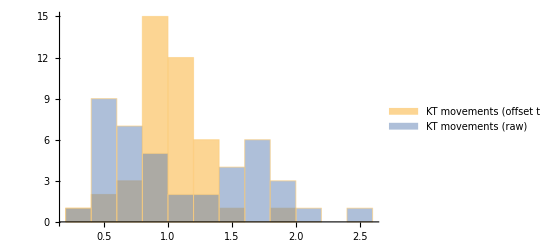

```mathematica
Histogram[{Transpose[controlresultplus][[33]],Transpose[controlresultplus][[22]]},10,ChartLegends->{"KT movements (offset the spindle movement)","KT movements (raw)"}]
```

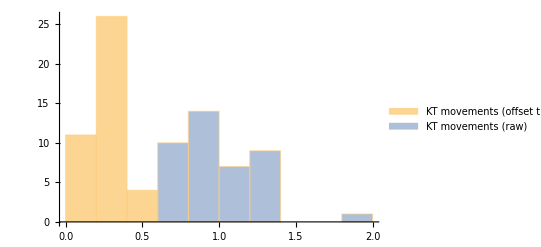

```mathematica
Histogram[{Transpose[controlresultplus][[30]],Transpose[controlresultplus][[35]]},10,ChartLegends->{"KT movements (offset the spindle movement)","KT movements (raw)"}]
```

```mathematica
Histogram[{Transpose[controlresultplus][[30]],Transpose[controlresultplus][[35]]},10,ChartLegends->{"KT movements (offset the spindle movement)","KT movements (raw)"}]
```

-Graphics-

```mathematica
tsaresultplus=Table[Join[i,i[[{22,23,30,31,32}]]/tsacellktmean[i[[2]]]],{i,tsaresult}];
```

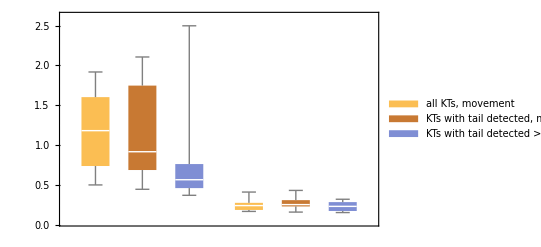

```mathematica
BoxWhiskerChart[{{Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]<1&]][[22]],Transpose[Select[controlresultplus,5>Total[#[[{18,19,20,21}]]]>=1&]][[22]],Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]>=5&]][[22]]},{Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]<1&]][[30]],Transpose[Select[controlresultplus,5>Total[#[[{18,19,20,21}]]]>=1&]][[30]],Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]>=5&]][[30]]}},ChartLegends->{"all KTs, movement","KTs with tail detected, movement","KTs with tail detected > 5 frames, movement"}]
```

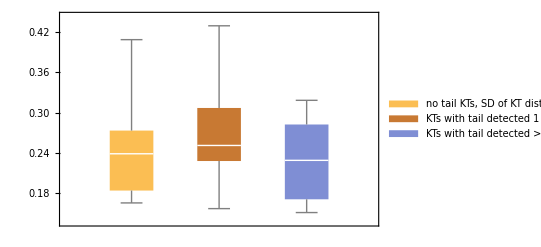

```mathematica
BoxWhiskerChart[{{Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]<1&]][[30]],Transpose[Select[controlresultplus,5>Total[#[[{18,19,20,21}]]]>=1&]][[30]],Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]>=5&]][[30]]}},ChartLegends->{"no tail KTs, SD of KT distance to metaphase plate
","KTs with tail detected 1 - 5 times, SD of KT distance to metaphase plate
","KTs with tail detected > 5 times, SD of KT distance to metaphase plate
"}]
```

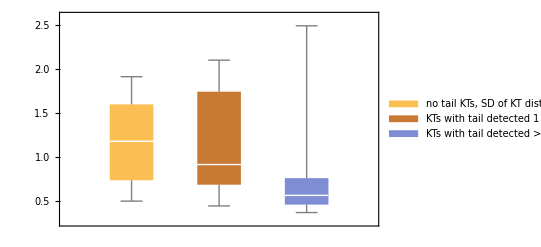

```mathematica
BoxWhiskerChart[{{Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]<1&]][[22]],Transpose[Select[controlresultplus,5>Total[#[[{18,19,20,21}]]]>=1&]][[22]],Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]>=5&]][[22]]}},ChartLegends->{"no tail KTs, SD of KT distance to metaphase plate
","KTs with tail detected 1 - 5 times, SD of KT distance to metaphase plate
","KTs with tail detected > 5 times, SD of KT distance to metaphase plate
"}]
```

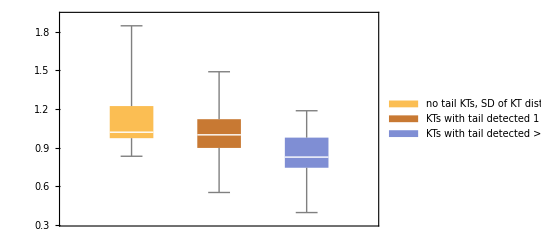

```mathematica
BoxWhiskerChart[{{Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]<1&]][[33]],Transpose[Select[controlresultplus,5>Total[#[[{18,19,20,21}]]]>=1&]][[33]],Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]>=5&]][[33]]}},ChartLegends->{"no tail KTs, SD of KT distance to metaphase plate
","KTs with tail detected 1 - 5 times, SD of KT distance to metaphase plate
","KTs with tail detected > 5 times, SD of KT distance to metaphase plate
"}]
```

```mathematica
LocationTest[{Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]<1&]][[33]],Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]>=5&]][[33]]}]
```

0.00626843

```mathematica
LocationTest[{Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]>5&]][[33]],Transpose[Select[controlresultplus,5>Total[#[[{18,19,20,21}]]]>=1&]][[33]]}]
```

0.0727083

```mathematica
LocationTest[{Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]>5&]][[22]],Transpose[Select[controlresultplus,5>Total[#[[{18,19,20,21}]]]>=1&]][[22]]}]
```

0.0585537

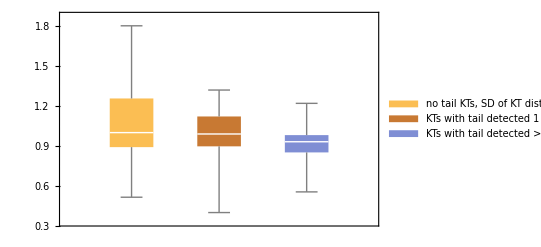

```mathematica
BoxWhiskerChart[{{Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]<1&]][[34]],Transpose[Select[controlresultplus,5>Total[#[[{18,19,20,21}]]]>=1&]][[34]],Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]>=5&]][[34]]}},ChartLegends->{"no tail KTs, SD of KT distance to metaphase plate (normalized)
","KTs with tail detected 1 - 5 times, SD of KT distance to metaphase plate(normalized)
","KTs with tail detected > 5 times, SD of KT distance to metaphase plate (normalized)
"}]
```

```mathematica
Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]>=5&]][[30]]
```

{0.170833,0.1647,0.176955,0.293441,0.318202,0.282199,0.151076,0.245167,0.254819,0.212478}

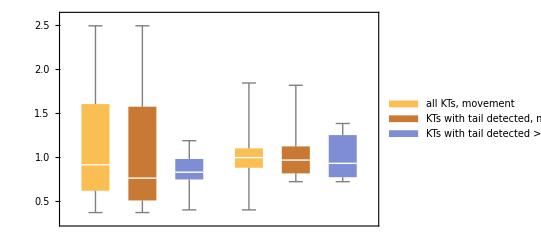

```mathematica
BoxWhiskerChart[{{Transpose[controlresultplus][[22]],Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]>=1&]][[22]],Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]>=5&]][[33]]},{Transpose[controlresultplus][[33]],Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]>=1&]][[35]],Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]>=5&]][[35]]}},ChartLegends->{"all KTs, movement","KTs with tail detected, movement","KTs with tail detected > 5 frames, movement"}]
```

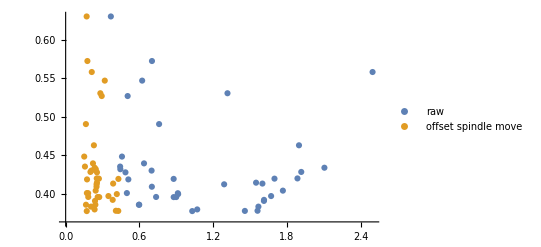

```mathematica
ListPlot[Map[Transpose,{{Transpose[controlresultplus][[22]],Transpose[controlresultplus][[6]]*2},{Transpose[controlresultplus][[30]],Transpose[controlresultplus][[6]]*2}}],PlotLegends->{"raw","offset spindle move"}]
```

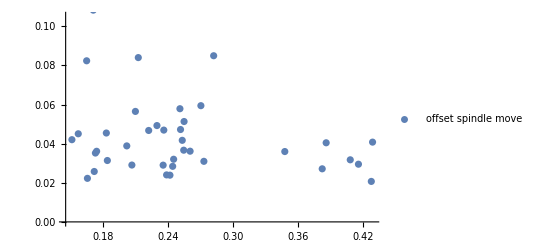

```mathematica
ListPlot[Map[Transpose,{{Transpose[controlresultplus][[30]],Transpose[controlresultplus][[10]]*2}}],PlotLegends->{"offset spindle move"}]
```

```mathematica
ListPlot[Map[Transpose,{{Transpose[controlresultplus][[30]],Transpose[controlresultplus][[10]]*2}}],PlotLegends->{"offset spindle move"}]
```

-Graphics-

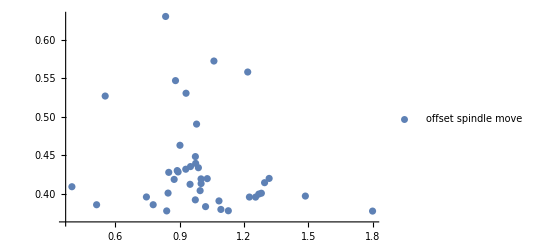

```mathematica
ListPlot[Map[Transpose,{{Transpose[controlresultplus][[34]],Transpose[controlresultplus][[6]]*2}}],PlotLegends->{"offset spindle move"}]
```

```mathematica
ListPlot[Map[Transpose,{{Transpose[controlresultplus][[22]],Transpose[controlresultplus][[6]]*2},{Transpose[controlresultplus][[30]],Transpose[controlresultplus][[6]]*2}}],PlotLegends->{"raw","offset spindle move"}]
```

-Graphics-

```mathematica
max6=Map[SortBy[#,#[[6]]&][[-1]][[6]]&,GatherBy[controlresultplus,#[[{1,2,3}]]&]];
```

```mathematica
max10=Map[SortBy[#,#[[10]]&][[-1]][[10]]&,GatherBy[controlresultplus,#[[{1,2,3}]]&]];
```

```mathematica
max22=Map[SortBy[#,#[[22]]&][[1]][[22]]&,GatherBy[controlresultplus,#[[{1,2,3}]]&]];
```

```mathematica
max30=Map[SortBy[#,#[[30]]&][[1]][[30]]&,GatherBy[controlresultplus,#[[{1,2,3}]]&]];
```

```mathematica
max33=Map[SortBy[#,#[[33]]&][[1]][[33]]&,GatherBy[controlresultplus,#[[{1,2,3}]]&]];
```

```mathematica
max34=Map[SortBy[#,#[[34]]&][[1]][[34]]&,GatherBy[controlresultplus,#[[{1,2,3}]]&]];
```

```mathematica
max33cellbycell=Map[Transpose[#][[33]]&,GatherBy[Map[SortBy[#,#[[33]]&][[1]]&,GatherBy[controlresultplus,#[[{1,2,3}]]&]],#[[2]]&]];
```

```mathematica
max10cellbycell=Map[Transpose[#][[10]]&,GatherBy[Map[SortBy[#,#[[10]]&][[-1]]&,GatherBy[controlresultplus,#[[{1,2,3}]]&]],#[[2]]&]];
```

```mathematica
max33cellbycell
```

{{0.888288,1.22474,1.2751,0.51242,0.97841},{1.31932,0.398133,1.22273,1.01774},{1.09256,0.745173},{0.994087,1.0225,0.834578,1.02307,0.989533},{1.84437,0.820624,1.06717,0.796911,0.793921},{1.00043,1.18656,0.902113},{1.}}

```mathematica
max6all=Map[SortBy[#,#[[6]]&][[-1]]&,GatherBy[controlresultplus,#[[{1,2,3}]]&]];
```

```mathematica
max10all=Map[SortBy[#,#[[10]]&][[-1]]&,GatherBy[controlresultplus,#[[{1,2,3}]]&]];
```

```mathematica
max22all=Map[SortBy[#,#[[22]]&][[1]]&,GatherBy[controlresultplus,#[[{1,2,3}]]&]];
```

```mathematica
max30all=Map[SortBy[#,#[[30]]&][[1]]&,GatherBy[controlresultplus,#[[{1,2,3}]]&]];
```

```mathematica
max34all=Map[SortBy[#,#[[34]]&][[1]]&,GatherBy[controlresultplus,#[[{1,2,3}]]&]];
```

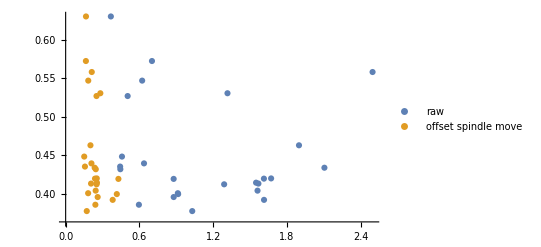

```mathematica
ListPlot[{Transpose[{max22,max6*2}],Transpose[{max30,max6*2}]},PlotLegends->{"raw","offset spindle move"}]
```

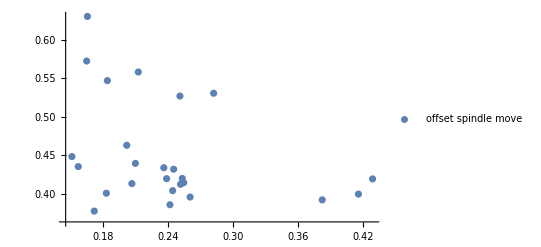

```mathematica
ListPlot[{Transpose[{max30,max6*2}]},PlotLegends->{"offset spindle move"}]
```

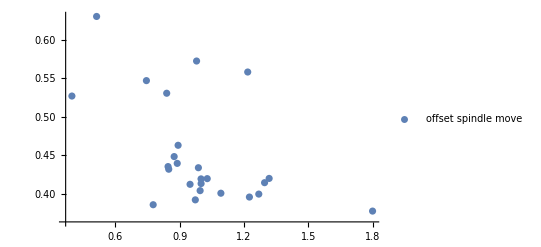

```mathematica
ListPlot[{Transpose[{max34,max6*2}]},PlotLegends->{"offset spindle move"},PlotRange->All]
```

```mathematica
ListPlot[{Transpose[{max34,max6*2}]},PlotLegends->{"offset spindle move"},PlotRange->All]
```

-Graphics-

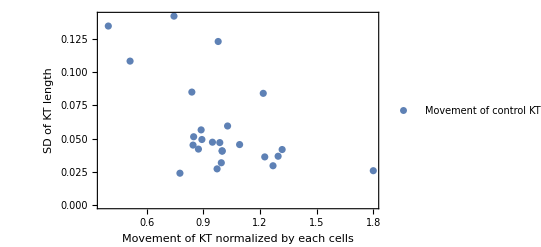

```mathematica
ListPlot[{Transpose[{max34,max10*2}]},PlotLegends->{"Movement of control KT normalized by each cells vs SD of KT length, deleted sister "},PlotRange->All,Frame->True,FrameLabel->{"Movement of KT normalized by each cells","SD of KT length "}]
```

```mathematica
Map[Transpose,Transpose[{max33cellbycell,max10cellbycell*2}]]
```

{{{0.888288,0.0565002},{1.22474,0.0361626},{1.2751,0.0295043},{0.51242,0.108293},{0.97841,0.12306}},{{1.31932,0.0417155},{0.398133,0.134694},{1.22273,0.0366709},{1.01774,0.0472423}},{{1.09256,0.0454544},{0.745173,0.142161}},{{0.994087,0.0404598},{1.0225,0.0594389},{0.834578,0.0849761},{1.02307,0.0271498},{0.989533,0.031753}},{{1.84437,0.025779},{0.820624,0.0420453},{1.06717,0.0238941},{0.796911,0.0513393},{0.793921,0.0450637}},{{1.00043,0.0469494},{1.18656,0.0840293},{0.902113,0.0492664}},{{1.,0.0407969}}}

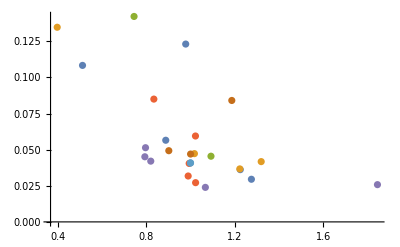

```mathematica
ListPlot[Map[Transpose,Transpose[{max33cellbycell,max10cellbycell*2}]]]
```

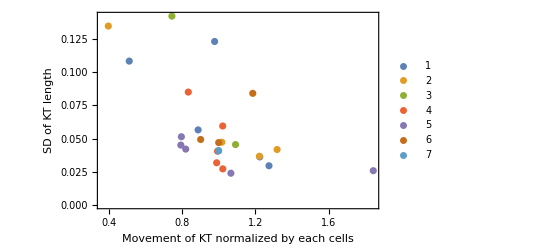

```mathematica
ListPlot[Map[Transpose,Transpose[{max33cellbycell,max10cellbycell*2}]],PlotRange->All,Frame->True,FrameLabel->{"Movement of KT normalized by each cells","SD of KT length "},PlotLegends->Automatic]
```

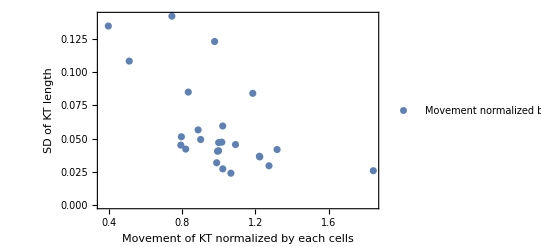

```mathematica
ListPlot[{Transpose[{max33,max10*2}]},PlotLegends->{"Movement normalized by each cells vs SD of KT length, deleted sister "},PlotRange->All,Frame->True,FrameLabel->{"Movement of KT normalized by each cells","SD of KT length "}]
```

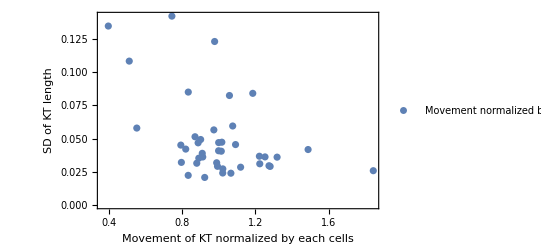

```mathematica
ListPlot[{Transpose[{Transpose[controlresultplus][[33]],Transpose[controlresultplus][[10]]*2}]},PlotLegends->{"Movement normalized by each cells vs SD of KT length, deleted sister "},PlotRange->All,Frame->True,FrameLabel->{"Movement of KT normalized by each cells","SD of KT length "}]
```

```mathematica
LocationTest[{Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]<1&]][[30]],Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]>=5&]][[30]]}]
```

0.407827

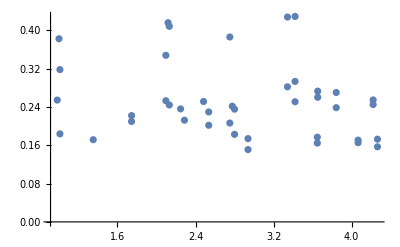

```mathematica
ListPlot[Transpose[{Transpose[controlresultplus][[32]],Transpose[controlresultplus][[30]]}],PlotRange->All]
```

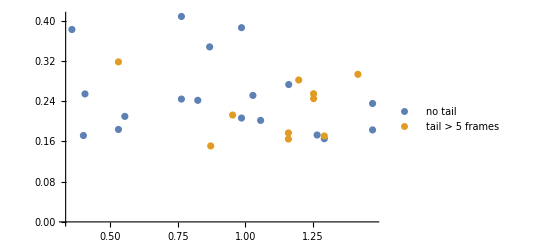

```mathematica
ListPlot[{Transpose[{Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]<1&]][[37]],Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]<1&]][[30]]}],Transpose[{Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]>=5&]][[37]],Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]>=5&]][[30]]}]},PlotRange->All,PlotLegends->{"no tail","tail > 5 frames"}]
```

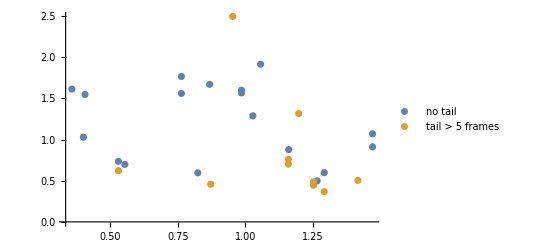

```mathematica
ListPlot[{Transpose[{Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]<1&]][[37]],Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]<1&]][[22]]}],Transpose[{Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]>=5&]][[37]],Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]>=5&]][[22]]}]},PlotRange->All,PlotLegends->{"no tail","tail > 5 frames"}]
```

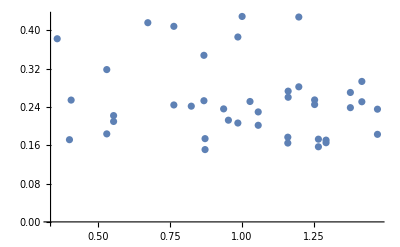

```mathematica
ListPlot[Transpose[{Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]<100&]][[37]],Transpose[Select[controlresultplus,Total[#[[{18,19,20,21}]]]<100&]][[30]]}],PlotRange->All]
```

```mathematica
Transpose[movementdata[allKTscontrol[[1]],1]][[{1,2}]]
```

{{5.888,5.888,6.164,6.624,6.992,7.176,7.268,7.176,6.992,6.808,6.44,6.256,5.98,5.704,5.52,5.796,6.164,6.44,6.624,6.808,6.992,7.084,6.992,6.808,6.716,6.532,6.348,5.98,5.704,5.612,5.336,5.52,5.796,6.164,6.532,6.716,6.9,7.084,7.084,7.36,7.36,7.452,7.452,7.452,7.268,6.992,6.532,6.348,6.072,5.796,5.704,5.612,5.612,5.98,6.072,6.164,6.072,6.072,5.98,5.796},{10.396,10.58,10.488,10.396,10.12,9.752,9.66,9.568,9.568,9.752,9.844,9.844,9.936,10.028,10.028,9.752,9.66,9.568,9.476,9.384,9.384,9.384,9.476,9.476,9.568,9.752,9.844,9.752,9.752,9.844,9.936,9.66,9.568,9.568,9.476,9.476,9.384,9.292,9.292,9.384,9.568,9.568,9.476,9.384,9.568,9.476,9.476,9.66,9.66,9.66,9.936,10.304,10.488,10.488,10.212,10.212,10.212,10.12,10.304,10.304}}

```mathematica
Transpose[movementdata[allKTscontrol[[1]],1]][[1]]+I * Transpose[movementdata[allKTscontrol[[1]],1]][[2]]
```

{5.888+10.396 ⅈ,5.888+10.58 ⅈ,6.164+10.488 ⅈ,6.624+10.396 ⅈ,6.992+10.12 ⅈ,7.176+9.752 ⅈ,7.268+9.66 ⅈ,7.176+9.568 ⅈ,6.992+9.568 ⅈ,6.808+9.752 ⅈ,6.44+9.844 ⅈ,6.256+9.844 ⅈ,5.98+9.936 ⅈ,5.704+10.028 ⅈ,5.52+10.028 ⅈ,5.796+9.752 ⅈ,6.164+9.66 ⅈ,6.44+9.568 ⅈ,6.624+9.476 ⅈ,6.808+9.384 ⅈ,6.992+9.384 ⅈ,7.084+9.384 ⅈ,6.992+9.476 ⅈ,6.808+9.476 ⅈ,6.716+9.568 ⅈ,6.532+9.752 ⅈ,6.348+9.844 ⅈ,5.98+9.752 ⅈ,5.704+9.752 ⅈ,5.612+9.844 ⅈ,5.336+9.936 ⅈ,5.52+9.66 ⅈ,5.796+9.568 ⅈ,6.164+9.568 ⅈ,6.532+9.476 ⅈ,6.716+9.476 ⅈ,6.9+9.384 ⅈ,7.084+9.292 ⅈ,7.084+9.292 ⅈ,7.36+9.384 ⅈ,7.36+9.568 ⅈ,7.452+9.568 ⅈ,7.452+9.476 ⅈ,7.452+9.384 ⅈ,7.268+9.568 ⅈ,6.992+9.476 ⅈ,6.532+9.476 ⅈ,6.348+9.66 ⅈ,6.072+9.66 ⅈ,5.796+9.66 ⅈ,5.704+9.936 ⅈ,5.612+10.304 ⅈ,5.612+10.488 ⅈ,5.98+10.488 ⅈ,6.072+10.212 ⅈ,6.164+10.212 ⅈ,6.072+10.212 ⅈ,6.072+10.12 ⅈ,5.98+10.304 ⅈ,5.796+10.304 ⅈ}

```mathematica
Fourier[Transpose[movementdata[allKTscontrol[[1]],1]][[1]]+I * Transpose[movementdata[allKTscontrol[[1]],1]][[2]]]
```

{49.8009+75.8 ⅈ,-0.47252+1.09014 ⅈ,-0.491761+2.1379 ⅈ,1.97563+1.04692 ⅈ,-1.15186+0.358977 ⅈ,-1.10454-0.530322 ⅈ,-0.99019-0.00502524 ⅈ,-0.0968066+0.201433 ⅈ,-0.326329+0.0348741 ⅈ,-0.0155817+0.0366756 ⅈ,0.0882259-0.151959 ⅈ,0.139903-0.260312 ⅈ,-0.0361559-0.0140255 ⅈ,-0.127187-0.0914083 ⅈ,-0.0525076+0.0218975 ⅈ,0.0237543+0.0356314 ⅈ,0.117905+0.00946415 ⅈ,-0.000744085-3.12604×10^-6 ⅈ,0.0205852+0.0406271 ⅈ,0.0303868+0.0225692 ⅈ,0.0621418-0.0340402 ⅈ,-0.0199531-0.0752075 ⅈ,-0.146836+0.0283388 ⅈ,0.0184942+0.0217633 ⅈ,-0.036491-0.000398252 ⅈ,0.047478-0.0160266 ⅈ,-0.0215848-0.00341193 ⅈ,0.0476712-0.0123759 ⅈ,0.0400516+0.0083331 ⅈ,0.0317639-0.0585613 ⅈ,-0.08314+0.0475086 ⅈ,0.00224118+0.0155082 ⅈ,0.0306079-0.0395534 ⅈ,0.0270709+0.0452098 ⅈ,0.0480109+0.0765078 ⅈ,0.0676541-0.0448361 ⅈ,0.00539625+0.00493492 ⅈ,0.127636-0.115389 ⅈ,0.0223446-0.0427455 ⅈ,0.0599787-0.0781851 ⅈ,0.0209982-0.0134684 ⅈ,0.113234+0.022919 ⅈ,0.0309544+0.0505153 ⅈ,-0.0147283-0.133751 ⅈ,-0.165708-0.00638473 ⅈ,0.0950172-0.0593857 ⅈ,0.102603+0.174812 ⅈ,-0.110604-0.0142118 ⅈ,0.0316192+0.0451203 ⅈ,0.155225-0.190773 ⅈ,-0.0763487+0.0331875 ⅈ,-0.0285346+0.0769578 ⅈ,-0.197335+0.0741313 ⅈ,0.279486+0.00819862 ⅈ,-0.0471533+0.282074 ⅈ,-0.0557769+0.757465 ⅈ,-1.69669+0.379682 ⅈ,1.39809-1.49132 ⅈ,-1.43187-0.552345 ⅈ,-0.45585+1.57226 ⅈ}

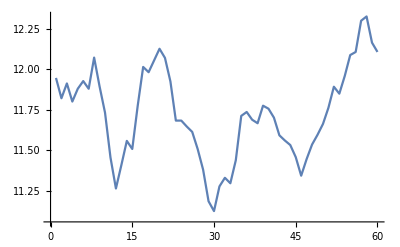

```mathematica
ListLinePlot[Abs[Fourier[Fourier[Transpose[movementdata[allKTscontrol[[1]],1]][[1]]+I * Transpose[movementdata[allKTscontrol[[1]],1]][[2]]]]]]
```

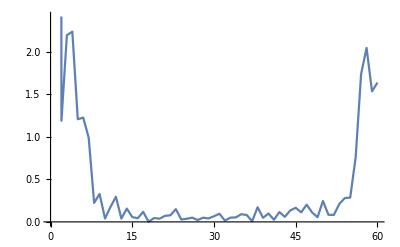
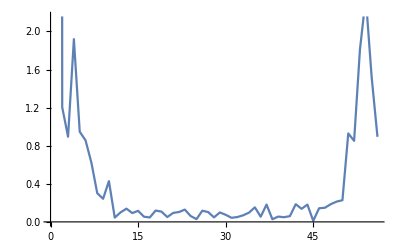
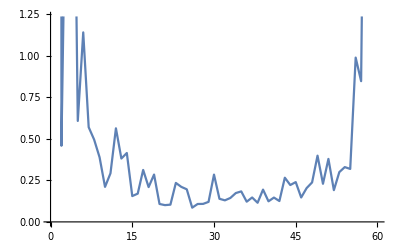
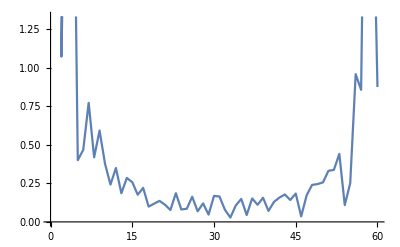
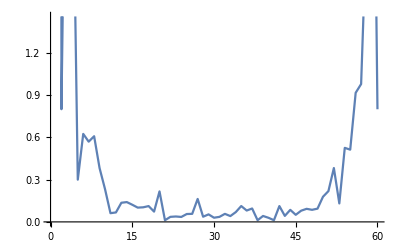
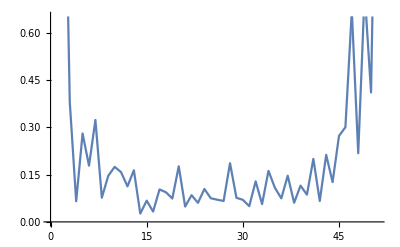
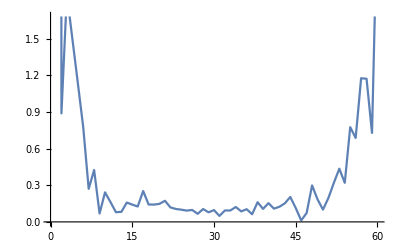
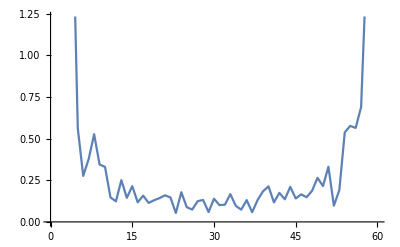
{{-Graphics-,0.0282501},{-Graphics-,0.0233791},{-Graphics-,0.0180813},{-Graphics-,0.0154892},{-Graphics-,0.0147522},{-Graphics-,0.0541465},{-Graphics-,0.0111369},{-Graphics-,0.0411967},{-Graphics-,0.0615302},{-Graphics-,0.0179911},{-Graphics-,0.0208577},{-Graphics-,0.0289416},{-Graphics-,0.0673469},{-Graphics-,0.0183355},{-Graphics-,0.0236212},{-Graphics-,0.0145104},{-Graphics-,0.0227272},{-Graphics-,0.0710804},{-Graphics-,0.0156975},{-Graphics-,0.0145375},{-Graphics-,0.0202299},{-Graphics-,0.0297194},{-Graphics-,0.0120177},{-Graphics-,0.0424881},{-Graphics-,0.010352},{-Graphics-,0.0135749},{-Graphics-,0.0158765},{-Graphics-,0.0142101},{-Graphics-,0.0128895},{-Graphics-,0.0210226},{-Graphics-,0.0180564},{-Graphics-,0.011947},{-Graphics-,0.0160195},{-Graphics-,0.0256696},{-Graphics-,0.0225319},{-Graphics-,0.0176067},{-Graphics-,0.0234747},{-Graphics-,0.0420147},{-Graphics-,0.0194336},{-Graphics-,0.0246332},{-Graphics-,0.0203985}}

```mathematica
fplots=Table[{ListLinePlot[Abs[Fourier[Transpose[movementdata[allKTscontrol[[i]],1]][[1]]+I * Transpose[movementdata[allKTscontrol[[i]],1]][[2]]]]],controlresultplus[[i]][[10]]},{i,Length[allKTscontrol]}]
```

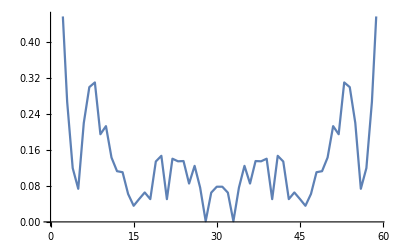
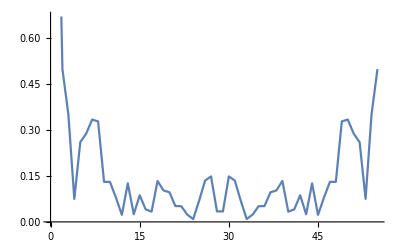
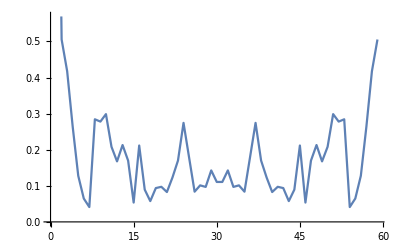
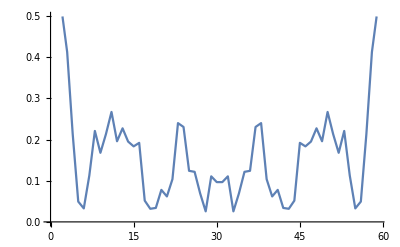
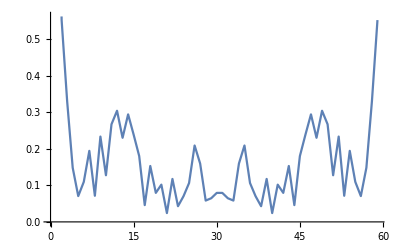
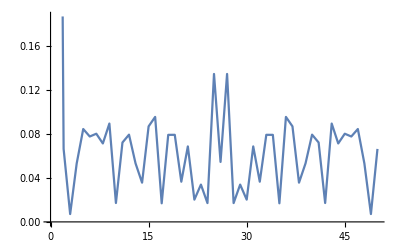
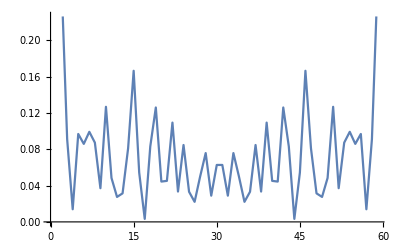
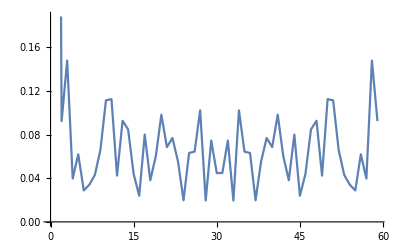
{{-Graphics-,0.0282501},{-Graphics-,0.0233791},{-Graphics-,0.0180813},{-Graphics-,0.0154892},{-Graphics-,0.0147522},{-Graphics-,0.0541465},{-Graphics-,0.0111369},{-Graphics-,0.0411967},{-Graphics-,0.0615302},{-Graphics-,0.0179911},{-Graphics-,0.0208577},{-Graphics-,0.0289416},{-Graphics-,0.0673469},{-Graphics-,0.0183355},{-Graphics-,0.0236212},{-Graphics-,0.0145104},{-Graphics-,0.0227272},{-Graphics-,0.0710804},{-Graphics-,0.0156975},{-Graphics-,0.0145375},{-Graphics-,0.0202299},{-Graphics-,0.0297194},{-Graphics-,0.0120177},{-Graphics-,0.0424881},{-Graphics-,0.010352},{-Graphics-,0.0135749},{-Graphics-,0.0158765},{-Graphics-,0.0142101},{-Graphics-,0.0128895},{-Graphics-,0.0210226},{-Graphics-,0.0180564},{-Graphics-,0.011947},{-Graphics-,0.0160195},{-Graphics-,0.0256696},{-Graphics-,0.0225319},{-Graphics-,0.0176067},{-Graphics-,0.0234747},{-Graphics-,0.0420147},{-Graphics-,0.0194336},{-Graphics-,0.0246332},{-Graphics-,0.0203985}}

```mathematica
Table[{ListLinePlot[Abs[Fourier[Abs[Fourier[Differences[Transpose[movementdata[allKTscontrol[[i]],1]][[1]]]+I * Differences[Transpose[movementdata[allKTscontrol[[i]],1]][[2]]]]]]]],controlresultplus[[i]][[10]]},{i,Length[allKTscontrol]}]
```

CorrelationFunction::bdlag: The lag specification 50 should be a symbol, an integer with magnitude less than the length of the data, or a range specification indicating such integers.

CorrelationFunction::bdlag: The lag specification 50. should be a symbol, an integer with magnitude less than the length of the data, or a range specification indicating such integers.

General::stop: Further output of CorrelationFunction::bdlag will be suppressed during this calculation.

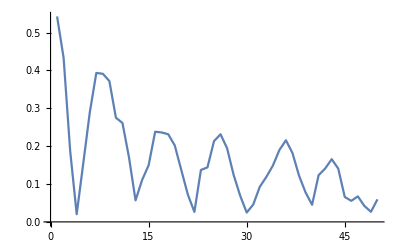
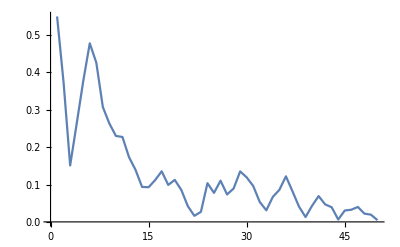
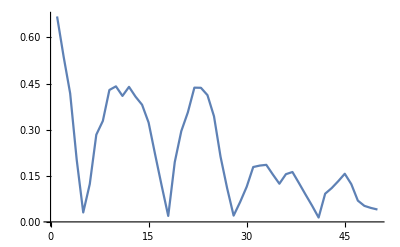
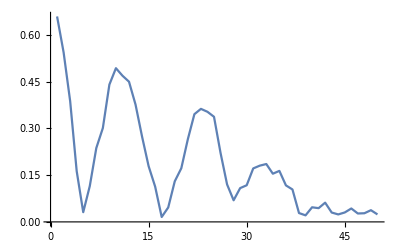
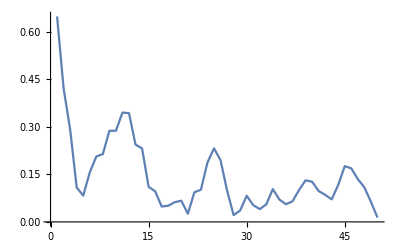
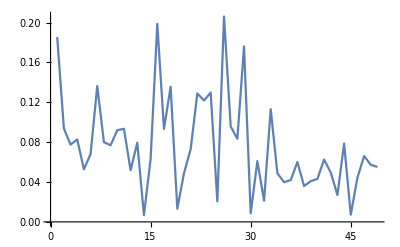
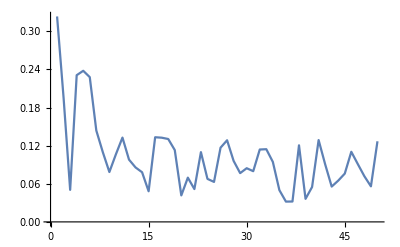
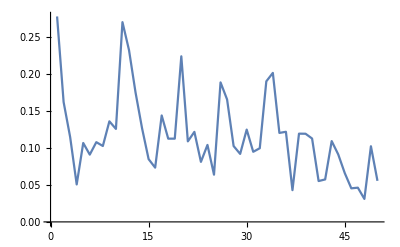
{{-Graphics-,0.0282501},{-Graphics-,0.0233791},{-Graphics-,0.0180813},{-Graphics-,0.0154892},{-Graphics-,0.0147522},{-Graphics-,0.0541465},{-Graphics-,0.0111369},{-Graphics-,0.0411967},{-Graphics-,0.0615302},{-Graphics-,0.0179911},{-Graphics-,0.0208577},{-Graphics-,0.0289416},{-Graphics-,0.0673469},{-Graphics-,0.0183355},{-Graphics-,0.0236212},{-Graphics-,0.0145104},{-Graphics-,0.0227272},{-Graphics-,0.0710804},{-Graphics-,0.0156975},{-Graphics-,0.0145375},{-Graphics-,0.0202299},{-Graphics-,0.0297194},{-Graphics-,0.0120177},{-Graphics-,0.0424881},{-Graphics-,0.010352},{-Graphics-,0.0135749},{-Graphics-,0.0158765},{-Graphics-,0.0142101},{-Graphics-,0.0128895},{-Graphics-,0.0210226},{-Graphics-,0.0180564},{-Graphics-,0.011947},{-Graphics-,0.0160195},{-Graphics-,0.0256696},{-Graphics-,0.0225319},{-Graphics-,0.0176067},{-Graphics-,0.0234747},{-Graphics-,0.0420147},{-Graphics-,0.0194336},{-Graphics-,0.0246332},{-Graphics-,0.0203985}}

```mathematica
Table[{ListLinePlot[Table[Abs[CorrelationFunction[Differences[Transpose[movementdata[allKTscontrol[[i]],1]][[1]]+I * Transpose[movementdata[allKTscontrol[[i]],1]][[2]]],s]],{s,50}]],controlresultplus[[i]][[10]]},{i,Length[allKTscontrol]}]
```

```mathematica
fmovedata=Table[{Abs[Fourier[Differences[Transpose[movementdata[allKTscontrol[[i]],1]][[1]]]+I * Differences[Transpose[movementdata[allKTscontrol[[i]],1]][[2]]]]],Total[controlresultplus[[i]][[{18,19,20,21}]]],controlresultplus[[i]][[10]]},{i,Length[allKTscontrol]}]
```

{{{0.0169386,0.0977983,0.440053,0.763303,0.411636,0.563717,0.633216,0.195906,0.333989,0.150923,0.0702154,0.300927,0.0457061,0.229581,0.152539,0.0815863,0.113956,0.0294459,0.0536185,0.0801818,0.136961,0.169367,0.243042,0.0476025,0.153738,0.0169958,0.125617,0.0324086,0.0540646,0.184279,0.146737,0.133881,0.134306,0.103357,0.205443,0.0425296,0.265194,0.0697154,0.0489432,0.0923439,0.129201,0.112928,0.220307,0.247195,0.173805,0.277138,0.184699,0.0597664,0.21373,0.172267,0.12172,0.180095,0.189164,0.218503,0.38117,0.701139,0.666173,0.328303,0.184077},0,0.0282501},{{0.100015,0.112949,0.138682,0.609394,0.436848,0.589014,0.325631,0.128952,0.0812507,0.345262,0.0617419,0.00712718,0.0973291,0.0671903,0.0752416,0.0395205,0.05623,0.0686251,0.12341,0.0905393,0.240974,0.0601238,0.181377,0.10597,0.162493,0.105499,0.167296,0.166518,0.114325,0.0796546,0.0341184,0.0470081,0.14896,0.177491,0.0831327,0.180854,0.209587,0.0550655,0.119556,0.0369816,0.143144,0.20997,0.177934,0.123517,0.0414933,0.192548,0.0595544,0.175829,0.248422,0.55138,0.570213,0.815632,0.728653,0.349636,0.200576},3,0.0233791},{{0.258001,0.208338,0.699886,0.957819,0.29636,0.697593,0.0903091,0.101131,0.0330379,0.14538,0.212428,0.266273,0.222663,0.27735,0.0447349,0.0576792,0.218005,0.16945,0.295693,0.049723,0.198025,0.217456,0.214152,0.12493,0.188077,0.152426,0.063742,0.148364,0.267979,0.260486,0.160889,0.125319,0.0439423,0.145422,0.156435,0.00776582,0.0778629,0.201193,0.174499,0.103067,0.106989,0.222951,0.0706606,0.0364565,0.115059,0.058085,0.104012,0.169502,0.111796,0.138339,0.140877,0.194667,0.193512,0.182271,0.390948,0.213323,0.944796,0.810358,0.190394},1,0.0180813},{{0.182827,0.235362,0.743152,0.953015,0.226592,0.32791,0.293494,0.26925,0.270742,0.158849,0.0485661,0.238158,0.0567508,0.156636,0.213452,0.103445,0.231876,0.0948323,0.158645,0.0685628,0.118943,0.182134,0.178648,0.0914034,0.0979797,0.136238,0.144081,0.10246,0.151666,0.123986,0.187607,0.157147,0.18776,0.159707,0.132645,0.137196,0.133188,0.26716,0.173798,0.146503,0.133583,0.153996,0.0213413,0.0583092,0.145005,0.0708113,0.222828,0.095488,0.109657,0.329732,0.128603,0.106788,0.270491,0.183152,0.574785,0.26135,0.924445,0.757226,0.144759},0,0.0154892},{{0.0338771,0.0735374,0.785509,0.881898,0.151913,0.276779,0.378829,0.485615,0.213795,0.204911,0.0800005,0.116012,0.182504,0.15016,0.177215,0.127147,0.213852,0.133137,0.08088,0.337606,0.122935,0.0379171,0.0700378,0.10939,0.0607441,0.248914,0.240973,0.0674046,0.0467577,0.0314708,0.118029,0.119414,0.0795408,0.159834,0.228535,0.105037,0.159499,0.123387,0.071054,0.0584421,0.204777,0.0550675,0.09414,0.0756871,0.103868,0.0882971,0.0530389,0.117949,0.187533,0.138991,0.358305,0.0957411,0.413239,0.277086,0.393876,0.484086,0.677708,0.84825,0.0869355},1,0.0147522},{{0.111164,0.207427,0.0165625,0.124652,0.0346826,0.126411,0.198623,0.076161,0.157414,0.305607,0.179228,0.147517,0.157264,0.118463,0.0630186,0.1156,0.137999,0.069233,0.301772,0.194469,0.172085,0.0461306,0.0866808,0.112703,0.0793313,0.104896,0.285768,0.0790752,0.0386221,0.112201,0.144545,0.147008,0.172326,0.11961,0.0513406,0.0947012,0.153298,0.0981715,0.0354156,0.12699,0.103987,0.118681,0.0257285,0.14414,0.113967,0.289085,0.0626208,0.152288,0.114904,0.1532},57,0.0541465},{{0.182434,0.187073,0.198674,0.296265,0.325785,0.297258,0.0623468,0.298816,0.202992,0.168124,0.118863,0.0989025,0.130901,0.172426,0.0529745,0.115768,0.157475,0.0622308,0.0359691,0.0621336,0.161474,0.223356,0.100809,0.126666,0.0362574,0.0666016,0.0571133,0.188106,0.0886325,0.0880071,0.119081,0.0672331,0.0604613,0.232014,0.141074,0.0585552,0.174958,0.0951138,0.111609,0.0724904,0.124839,0.225466,0.109352,0.0877282,0.187246,0.0330374,0.236636,0.197577,0.065649,0.141656,0.319294,0.21951,0.0949644,0.366669,0.390492,0.330471,0.196601,0.10948,0.148265},0,0.0111369},{{0.231322,0.0905828,0.221967,0.417027,0.0795334,0.0764983,0.0606178,0.198704,0.158846,0.225321,0.0417117,0.129273,0.0998321,0.0854821,0.119415,0.0989371,0.0606516,0.146988,0.0486379,0.0396635,0.066252,0.138001,0.217059,0.108301,0.0468571,0.175994,0.143596,0.0682094,0.131533,0.146627,0.202173,0.139801,0.170428,0.0394926,0.111759,0.0609026,0.154947,0.158016,0.129102,0.130405,0.106864,0.0837696,0.0783621,0.218571,0.0799595,0.0448355,0.0645703,0.101761,0.033,0.0874884,0.162607,0.0647594,0.203439,0.130882,0.173168,0.24803,0.265882,0.211048,0.0593845},19,0.0411967},{{0.20502,0.240928,0.236641,0.412042,0.132888,0.271699,0.186749,0.0408325,0.169761,0.201972,0.156428,0.0707026,0.109912,0.126195,0.123277,0.22147,0.0223674,0.0172599,0.097285,0.0958167,0.121866,0.209779,0.281007,0.105943,0.0480264,0.06012,0.120368,0.0618348,0.127161,0.0938832,0.126717,0.156227,0.127016,0.150144,0.0998726,0.110423,0.0684306,0.164905,0.0775632,0.152583,0.0732067,0.0933182,0.132319,0.10812,0.138895,0.0335797,0.120996,0.116201,0.286875,0.108425,0.116641,0.162482,0.170855,0.102555,0.243413,0.222685,0.394792,0.0850592,0.0539431},41,0.0615302},{{0.449825,0.278405,0.255148,1.04322,0.452479,0.631916,0.423968,0.500531,0.406064,0.217883,0.139434,0.152432,0.16387,0.0722539,0.135253,0.179246,0.0948314,0.11717,0.336809,0.123157,0.0734441,0.0580275,0.10718,0.0338655,0.26299,0.0782975,0.0853478,0.186033,0.0742727,0.105903,0.0776422,0.0648122,0.175916,0.0965059,0.12122,0.15363,0.134435,0.124971,0.0598352,0.197691,0.209921,0.198619,0.228765,0.0519986,0.072688,0.141872,0.129849,0.201965,0.165855,0.111716,0.215332,0.0945473,0.16997,0.232543,0.079709,0.118248,0.166262,0.386749,0.141057,0.280787,0.423364,0.809127,0.360643,0.271316},0,0.0179911},{{0.580588,0.234021,0.247945,1.31518,0.181837,0.170943,0.27226,0.357336,0.133403,0.323453,0.090292,0.0594811,0.266581,0.0689648,0.154033,0.0545658,0.161361,0.0601251,0.277014,0.0867289,0.106942,0.176336,0.166641,0.124507,0.0495838,0.172212,0.042135,0.105351,0.204274,0.0541362,0.0185369,0.167749,0.0621152,0.028945,0.0664465,0.0721398,0.148833,0.117324,0.168405,0.15034,0.0356698,0.121785,0.152258,0.164087,0.0601152,0.266398,0.117262,0.159768,0.265508,0.0662841,0.236291,0.178435,0.105488,0.133885,0.186312,0.36387,0.510651,0.435033,0.365018,0.448027,1.21416,0.262734,0.316063},1,0.0208577},{{0.0948314,0.156491,0.585034,0.349042,0.217024,0.60281,1.01426,0.487509,0.339909,0.198136,0.188355,0.305933,0.180579,0.242944,0.225126,0.0613155,0.268224,0.24721,0.167496,0.137129,0.149854,0.391135,0.221778,0.145216,0.118181,0.0578315,0.162414,0.0476061,0.117829,0.0365767,0.0541825,0.0134891,0.139904,0.199299,0.309082,0.169634,0.0433416,0.0496444,0.120631,0.196178,0.0964653,0.170822,0.133068,0.0823864,0.199864,0.088118,0.271368,0.0452588,0.162635,0.0411523,0.0751044,0.21896,0.167385,0.276061,0.257642,0.404922,0.23635,0.500123,0.683184,0.566228,0.0178247,0.517247,0.288029,0.262087},1,0.0289416},{{0.0692551,0.100287,0.370762,0.214763,0.314441,0.22019,0.306935,0.298468,0.168274,0.045669,0.378256,0.420448,0.0928337,0.01317,0.21516,0.118771,0.122737,0.21829,0.0934033,0.156839,0.103288,0.212743,0.152798,0.20978,0.0866666,0.182579,0.155928,0.0450217,0.143935,0.243694,0.112677,0.227421,0.228877,0.0735321,0.121496,0.216839,0.226083,0.257543,0.215237,0.382498,0.144674,0.127136,0.21726,0.100473,0.298536,0.167968,0.274119,0.0940559,0.0914827,0.267119,0.298053,0.136222,0.228084,0.270351,0.269722,0.299221,0.198322,0.116401,0.371775,0.150289},26,0.0673469},{{0.472061,0.150158,0.463832,0.352522,0.86365,0.220764,0.637152,0.491113,0.444917,0.101426,0.100459,0.26862,0.0782855,0.277307,0.184701,0.208269,0.0474157,0.123691,0.219678,0.205943,0.111346,0.24965,0.0990589,0.185392,0.154717,0.169458,0.22182,0.153237,0.264857,0.0857745,0.046924,0.218971,0.0837213,0.0448757,0.15088,0.0787503,0.0270208,0.132767,0.198383,0.162969,0.117956,0.262281,0.110796,0.0579544,0.128709,0.0430921,0.159377,0.109479,0.318905,0.272278,0.185567,0.133592,0.2279,0.193908,0.205711,0.0394456,0.154717,0.261568,0.572999,0.436372,0.926158,0.778702,0.63113,0.259188},0,0.0183355},{{0.346721,0.251507,0.241331,0.0980572,0.354006,0.49383,0.617105,0.352924,0.219619,0.107823,0.109875,0.164577,0.0141035,0.18406,0.164324,0.124254,0.128574,0.165342,0.0607264,0.167873,0.0915902,0.0743077,0.111478,0.278976,0.224631,0.198787,0.10724,0.0828662,0.208806,0.0858451,0.108487,0.2245,0.098256,0.0595044,0.0824838,0.146938,0.0424754,0.0692399,0.107983,0.0178183,0.0578375,0.156068,0.126493,0.104248,0.103792,0.231031,0.188946,0.247009,0.211112,0.408549,0.109694,0.0767557,0.233233,0.0951908,0.155137,0.184561,0.239149,0.144856,0.310728,0.512157,0.464486,0.120928,0.218568,0.309142},0,0.0236212},{{0.0345,0.252572,0.258105,0.617637,0.106354,0.447981,0.883646,0.162833,0.43693,0.304369,0.103274,0.459712,0.0746537,0.21378,0.204254,0.136008,0.106025,0.239153,0.166054,0.153565,0.31631,0.171121,0.14679,0.220888,0.212501,0.163601,0.0880438,0.105933,0.0636915,0.0996978,0.167098,0.28438,0.1725,0.135584,0.17592,0.0619366,0.0772967,0.145322,0.195146,0.146128,0.137261,0.0709319,0.325386,0.136916,0.219299,0.255283,0.271098,0.194026,0.185788,0.061676,0.126866,0.281163,0.157998,0.310526,0.120199,0.383115,0.110633,0.30986,0.55964,0.285686,0.344144,0.796517,0.224577,0.653775},0,0.0145104},{{0.0345,0.17813,0.323131,0.403128,0.234178,0.0975081,0.425479,0.0666397,0.26971,0.100087,0.0221816,0.547251,0.177972,0.239672,0.253053,0.012938,0.0474157,0.151623,0.00821318,0.096642,0.183653,0.142782,0.0986003,0.195738,0.220119,0.250425,0.148829,0.0283389,0.201063,0.16768,0.230351,0.127529,0.3335,0.18294,0.0680149,0.184116,0.197793,0.122888,0.236185,0.184051,0.0562869,0.115812,0.332517,0.111133,0.201838,0.401824,0.309012,0.257908,0.0474157,0.169018,0.516354,0.321222,0.240809,0.435983,0.024923,0.0946733,0.425287,0.0295854,0.215667,0.144843,0.437419,0.59421,0.341856,0.602735},0,0.0227272},{{0.17554,0.168756,0.255134,0.149216,0.465131,0.218797,0.143185,0.369291,0.221077,0.220162,0.203565,0.103537,0.233627,0.0810356,0.343147,0.413335,0.334292,0.346374,0.144419,0.158561,0.380535,0.0693574,0.302473,0.511968,0.711983,0.135761,0.120005,0.169336,0.289375,0.204967,0.0610029,0.32507,0.174027,0.344876,0.218245,0.353904,0.235289,0.181344,0.112076,0.110531,0.400431,0.312844,0.264986,0.0832319,0.169938,0.447506,0.20096,0.315523,0.285654,0.418148,0.400608,0.15087,0.224928,0.411194,0.0477611,0.2594,0.397866,0.341104,0.229783,0.650425,0.515803,0.265054,0.272404,0.179365},37,0.0710804},{{0.160176,0.112652,0.215935,0.183498,0.986508,0.245656,0.382558,0.357009,0.156532,0.0316974,0.220465,0.336418,0.0425,0.138468,0.242173,0.256457,0.253,0.115787,0.202763,0.0675089,0.239979,0.130769,0.0229718,0.2156,0.333206,0.0465462,0.203155,0.0119568,0.298789,0.19617,0.0757819,0.320773,0.303826,0.161422,0.140753,0.249717,0.137492,0.0383232,0.104998,0.0463708,0.166939,0.160319,0.290841,0.113624,0.131906,0.372947,0.045248,0.232052,0.092,0.200535,0.353417,0.178098,0.162157,0.375108,0.125202,0.386733,0.45019,0.15046,0.51572,0.740434,0.964063,0.154167,0.175591,0.127373},0,0.0156975},{{0.791323,0.759004,0.479394,0.0277478,0.404903,0.109382,0.0743373,0.174017,0.148106,0.246835,0.29144,0.170418,0.0047503,0.0796751,0.0129344,0.471905,0.248798,0.245807,0.350709,0.236307,0.295597,0.39326,0.068868,0.205687,0.149875,0.107275,0.102406,0.133125,0.315722,0.115321,0.107361,0.135873,0.29411,0.191176,0.207587,0.271823,0.178218,0.228094,0.230195,0.0466127,0.139362,0.29981,0.21114,0.302139,0.321398,0.157855,0.121627,0.160335,0.0793938,0.141322,0.0618706,0.279013,0.237574,0.0680669,0.349744,0.299937,0.04169,0.520752,0.405346},0,0.0145375},{{0.77991,0.69111,0.543282,0.250535,0.432861,0.506338,0.356682,0.170343,0.0875424,0.104789,0.131279,0.244184,0.184877,0.186625,0.296481,0.404144,0.25375,0.299373,0.329906,0.341173,0.163715,0.223966,0.232368,0.235401,0.102359,0.158133,0.249551,0.25331,0.271021,0.144133,0.188523,0.0732997,0.224284,0.270279,0.11351,0.238884,0.209572,0.071458,0.345655,0.096403,0.168475,0.422463,0.156259,0.157155,0.36494,0.107465,0.137138,0.148813,0.206001,0.273589,0.229371,0.22457,0.0662725,0.135887,0.103934,0.233751,0.321241,0.509509,0.391774},0,0.0202299},{{0.595024,0.418347,0.557224,0.495728,0.454593,0.193828,0.255289,0.274538,0.108142,0.158171,0.157011,0.0570901,0.313284,0.142802,0.200403,0.0774235,0.229914,0.0819157,0.32495,0.159604,0.255396,0.33295,0.21347,0.137505,0.0313213,0.154046,0.0517945,0.145931,0.0644475,0.0309828,0.0711104,0.0757966,0.237899,0.244179,0.190828,0.327226,0.362706,0.174496,0.149842,0.145944,0.265376,0.273744,0.0888103,0.12092,0.143548,0.283427,0.0985021,0.085892,0.19975,0.190531,0.252261,0.295548,0.307593,0.250328,0.0852554,0.279396,0.116513,0.304741,0.44874},4,0.0297194},{{0.567505,0.391996,0.525947,0.310248,0.180994,0.191911,0.238963,0.188461,0.249112,0.181823,0.181676,0.151514,0.0980029,0.155826,0.239279,0.136117,0.440506,0.104949,0.217728,0.30723,0.384818,0.424109,0.125165,0.201446,0.0734625,0.238931,0.113613,0.1081,0.178439,0.171859,0.0770711,0.291177,0.0927569,0.129933,0.273503,0.190401,0.159394,0.268792,0.247888,0.0249998,0.171008,0.231019,0.258839,0.134802,0.145276,0.236817,0.122144,0.0357428,0.143983,0.136401,0.157559,0.177994,0.153517,0.267272,0.226403,0.226326,0.170967,0.346871,0.581522},1,0.0120177},{{0.564972,0.127774,0.259263,0.178435,0.222548,0.0769088,0.0335023,0.0877726,0.0504601,0.115831,0.067484,0.118603,0.126909,0.186553,0.220348,0.309445,0.120844,0.171432,0.370835,0.214595,0.15226,0.52774,0.0914393,0.307135,0.110819,0.184014,0.12918,0.0788597,0.152494,0.154062,0.113466,0.098022,0.130505,0.162069,0.0926821,0.186287,0.275922,0.221148,0.299685,0.081741,0.195559,0.305889,0.126308,0.180766,0.172524,0.0428309,0.0483312,0.0323393,0.11418,0.0862493,0.135347,0.124067,0.152162,0.146997,0.19079,0.290841,0.207825,0.13525,0.201111},38,0.0424881},{{0.562427,0.209669,0.271863,0.0496828,0.0896827,0.245936,0.0934892,0.176808,0.0485583,0.162117,0.102217,0.118928,0.129717,0.0440065,0.204781,0.188711,0.0776689,0.159643,0.484457,0.311587,0.142998,0.509777,0.204393,0.304216,0.140742,0.0393286,0.225934,0.112545,0.101665,0.116735,0.102737,0.259577,0.0516047,0.159692,0.0236448,0.176958,0.220594,0.0825105,0.313505,0.213842,0.0559488,0.409229,0.121281,0.378836,0.176765,0.0473995,0.0603922,0.0533842,0.271176,0.165197,0.139029,0.210413,0.191425,0.329019,0.0449684,0.420897,0.176272,0.06227,0.329613},1,0.010352},{{0.673401,0.666851,0.111739,0.0857356,0.210566,0.20431,0.105327,0.10138,0.189021,0.149337,0.100831,0.193041,0.20039,0.057894,0.321624,0.255182,0.315015,0.381749,0.32336,0.0962173,0.212564,0.498665,0.305016,0.222758,0.105766,0.147509,0.166276,0.103753,0.141909,0.111299,0.0802938,0.234343,0.187663,0.140236,0.0564875,0.35634,0.207536,0.145828,0.42351,0.120667,0.237748,0.397264,0.212142,0.0972134,0.299407,0.148627,0.0996535,0.139032,0.0658267,0.0812713,0.374814,0.302226,0.286944,0.270218,0.243015,0.459651,0.414475,0.268226,0.414312},0,0.0135749},{{0.677595,0.498741,0.0998613,0.297895,0.189657,0.10684,0.13762,0.0893175,0.177402,0.103159,0.139981,0.0164607,0.0508348,0.0347887,0.333284,0.170961,0.16904,0.458889,0.0734184,0.277204,0.255888,0.378233,0.0644647,0.111652,0.0206756,0.0685661,0.130098,0.24851,0.0892069,0.0132898,0.265173,0.152124,0.125677,0.154677,0.0707538,0.17574,0.121378,0.162498,0.0694829,0.178507,0.395823,0.0617255,0.162465,0.275948,0.0475325,0.242513,0.191884,0.149828,0.0712041,0.2024,0.143816,0.151787,0.156274,0.287389,0.34955,0.0494748,0.340564},0,0.0158765},{{0.78294,0.43485,0.121529,0.307631,0.220436,0.313021,0.28993,0.314106,0.236371,0.239714,0.0368339,0.102511,0.0388946,0.0991256,0.186031,0.241373,0.0984572,0.347791,0.42828,0.166469,0.10403,0.272186,0.204556,0.287296,0.109671,0.147574,0.13629,0.0466682,0.252511,0.119187,0.0901436,0.246044,0.26062,0.169838,0.0667697,0.135422,0.281873,0.203275,0.215561,0.0671594,0.243042,0.360831,0.154024,0.210227,0.0465648,0.140937,0.181793,0.00468901,0.168199,0.0564594,0.152056,0.13786,0.237557,0.0903708,0.358273,0.579535,0.532328,0.108016,0.277129},0,0.0142101},{{0.159798,0.38408,0.246671,0.146868,0.314598,0.366937,0.302804,0.12451,0.338201,0.200789,0.133341,0.0151924,0.249067,0.0188053,0.386959,0.380442,0.321351,0.304249,0.116387,0.100116,0.236904,0.0695196,0.238295,0.0962484,0.0961355,0.131731,0.0563922,0.149898,0.0936843,0.0899253,0.102681,0.165563,0.0302099,0.0307863,0.0745753,0.0179355,0.203751,0.206824,0.210434,0.0543012,0.224248,0.0661178,0.142254,0.190794,0.175367,0.256541,0.140971,0.0956031,0.118406,0.108519,0.274972,0.126638,0.0977407,0.226895,0.272515,0.185809,0.172212,0.396315,0.459694},0,0.0128895},{{0.129,0.249734,0.133009,0.0109263,0.183012,0.177945,0.0517501,0.156508,0.312316,0.0127958,0.212488,0.0696706,0.243045,0.0160423,0.484688,0.317904,0.29346,0.236287,0.198466,0.182869,0.164355,0.0470575,0.184741,0.0792481,0.0684786,0.173194,0.0796775,0.228247,0.0549492,0.126282,0.349947,0.0534251,0.0780375,0.136897,0.0249328,0.0769777,0.191024,0.058205,0.0677854,0.10466,0.0713838,0.0119229,0.0744513,0.369097,0.250313,0.358286,0.282345,0.177631,0.16141,0.251389,0.0776841,0.083055,0.172283,0.155453,0.0149183,0.0386818,0.0781584,0.132025,0.095767},7,0.0210226},{{0.159798,0.210607,0.0853184,0.142052,0.177168,0.216579,0.0996325,0.0670785,0.10879,0.126521,0.145366,0.0875597,0.117473,0.209835,0.500876,0.189022,0.35969,0.212932,0.134945,0.133316,0.171383,0.0879377,0.124445,0.0710408,0.214569,0.163333,0.194039,0.0598974,0.0611111,0.148138,0.181807,0.151408,0.133166,0.193741,0.170987,0.0941442,0.185186,0.0686442,0.0362125,0.291364,0.160506,0.0724217,0.0115822,0.274852,0.248328,0.251432,0.164462,0.176115,0.224057,0.0846177,0.103997,0.0912898,0.333818,0.219257,0.296901,0.0745735,0.0126885,0.0727941,0.255236},2,0.0180564},{{0.0359321,0.301469,0.302335,0.141604,0.233122,0.0546456,0.232406,0.254268,0.15311,0.142358,0.0641764,0.109165,0.172307,0.0920852,0.188566,0.164969,0.231882,0.118429,0.103858,0.13091,0.235536,0.0918507,0.0895013,0.186148,0.160475,0.124508,0.137269,0.128817,0.0164804,0.0600118,0.0550979,0.1992,0.0938761,0.141756,0.134473,0.026651,0.258208,0.184931,0.172797,0.0163599,0.145803,0.262043,0.115385,0.242545,0.142995,0.265725,0.110936,0.252851,0.149421,0.148116,0.0991515,0.0890412,0.256914,0.264653,0.129826,0.146443,0.17078,0.0424442,0.380282},0,0.011947},{{0.157538,0.0453871,0.13738,0.0341955,0.193546,0.091838,0.106885,0.113959,0.2002,0.244454,0.105516,0.169591,0.172479,0.165504,0.410886,0.279757,0.299298,0.320557,0.1684,0.229516,0.244386,0.0517854,0.138432,0.197627,0.268321,0.0918396,0.135131,0.125815,0.0679144,0.147911,0.148803,0.162075,0.106144,0.107808,0.103673,0.00559474,0.206012,0.062039,0.091578,0.0474869,0.13471,0.0974032,0.121816,0.232624,0.150021,0.187988,0.0641464,0.303882,0.0650004,0.130852,0.0875281,0.0519561,0.141988,0.188582,0.071435,0.096144,0.0807755,0.16019,0.116132},8,0.0160195},{{0.189379,0.0319031,0.106026,0.167462,0.1235,0.147792,0.0670318,0.0481466,0.301745,0.0900465,0.0282664,0.202158,0.192335,0.138388,0.381433,0.281804,0.281566,0.262159,0.25619,0.183289,0.198917,0.0420849,0.11166,0.0990848,0.0460553,0.123109,0.0948082,0.292916,0.0740724,0.216231,0.0746316,0.11747,0.0563697,0.118032,0.0463974,0.0644921,0.251985,0.0838445,0.133075,0.0581254,0.121071,0.0246248,0.00956211,0.242989,0.193226,0.282339,0.318993,0.176933,0.122717,0.101707,0.065815,0.0537485,0.029519,0.238353,0.0842032,0.131833,0.212727,0.138191,0.143917},6,0.0256696},{{0.144723,0.248461,0.166242,0.104577,0.170647,0.243587,0.135536,0.132049,0.136493,0.0148067,0.083091,0.195408,0.0946852,0.205525,0.565501,0.375217,0.456864,0.294931,0.024529,0.129427,0.146779,0.230218,0.124629,0.194253,0.207387,0.029872,0.0611002,0.255539,0.166174,0.188965,0.219515,0.105374,0.060239,0.123936,0.0587507,0.100109,0.289897,0.156871,0.0691232,0.337222,0.179172,0.044892,0.045702,0.281734,0.250974,0.221955,0.257448,0.308953,0.244497,0.177771,0.159356,0.166002,0.103895,0.0629694,0.116127,0.111943,0.110775,0.155341,0.0397752},3,0.0225319},{{0.189379,0.186504,0.0378345,0.0764879,0.0693126,0.200582,0.194827,0.158004,0.302749,0.0112741,0.0668085,0.314016,0.31621,0.0691657,0.506578,0.22129,0.217667,0.165869,0.0445256,0.146309,0.177672,0.132343,0.114821,0.169124,0.221948,0.0340685,0.0934839,0.0736297,0.208014,0.190391,0.11168,0.176182,0.039275,0.0633008,0.158918,0.0693843,0.448655,0.0800757,0.013099,0.315377,0.186593,0.0688564,0.133793,0.349734,0.0923804,0.187024,0.288541,0.171581,0.227207,0.284109,0.0846046,0.116744,0.207526,0.0729494,0.193073,0.242176,0.0595906,0.129869,0.0460165},0,0.0176067},{{0.844379,0.309663,0.44579,0.694909,0.393372,0.177747,0.258496,0.0714376,0.127373,0.0371693,0.0799207,0.0671756,0.263248,0.0655345,0.287655,0.11714,0.199807,0.0677594,0.0769571,0.0849644,0.145223,0.00404503,0.0681171,0.128186,0.0902401,0.0922413,0.204883,0.0379081,0.0828202,0.106338,0.0943805,0.183597,0.149358,0.125625,0.209418,0.0829842,0.123514,0.0611723,0.11451,0.23119,0.0657972,0.0536908,0.119058,0.438663,0.353055,0.170897,0.225174,0.0861619,0.190746,0.287151,0.1061,0.220452,0.537126,0.461427,0.217559},1,0.0234747},{{1.0207,0.199577,0.15413,0.365761,0.159501,0.114093,0.168702,0.458617,0.125149,0.288149,0.446653,0.17907,0.370782,0.352315,0.331938,0.11181,0.342729,0.0974171,0.198519,0.0677049,0.132852,0.203619,0.256241,0.109771,0.100198,0.304623,0.118162,0.0940007,0.123553,0.16374,0.147071,0.19407,0.132808,0.0139878,0.0461477,0.15473,0.215392,0.0670195,0.103394,0.154522,0.190575,0.147968,0.0991175,0.117598,0.160424,0.207842,0.152279,0.307672,0.0918273,0.19504,0.201139,0.193782,0.164976,0.635011,0.0758019,0.158427},28,0.0420147},{{0.860669,0.599137,0.114948,0.396691,0.120319,0.236809,0.279855,0.203957,0.20663,0.145071,0.163592,0.151672,0.409344,0.240077,0.408672,0.227405,0.219648,0.0560956,0.098867,0.0807374,0.155759,0.25945,0.25942,0.231652,0.123436,0.106721,0.0488196,0.267847,0.121082,0.129328,0.137579,0.0445441,0.0750974,0.0314401,0.170729,0.150959,0.213713,0.207206,0.060502,0.113979,0.173028,0.190585,0.165399,0.260633,0.394382,0.174392,0.179347,0.19084,0.299658,0.210308,0.248393,0.530081,0.112548,0.540155,0.220022,0.24063},0,0.0194336},{{0.82599,0.549498,0.195947,0.160514,0.149454,0.222842,0.180329,0.138872,0.18786,0.13557,0.225203,0.0972126,0.408919,0.142326,0.269909,0.124692,0.20038,0.195482,0.0598327,0.0499276,0.136601,0.226154,0.0949089,0.144441,0.0505365,0.0431683,0.310358,0.199941,0.18482,0.0943299,0.0206761,0.187533,0.0582712,0.00644055,0.133435,0.0855314,0.304524,0.206147,0.0897513,0.101516,0.0865674,0.176839,0.203502,0.24261,0.427903,0.206346,0.180709,0.249277,0.126516,0.0571481,0.349383,0.147166,0.230466,0.527922,0.213318,0.187415},4,0.0246332},{{0.356113,0.239811,0.204147,0.158915,0.345599,0.14813,0.160613,0.140126,0.243031,0.174155,0.13285,0.142777,0.247031,0.243229,0.13681,0.108143,0.123498,0.188269,0.248072,0.247818,0.146283,0.141343,0.090878,0.195568,0.112173,0.128847,0.165,0.223061,0.131185,0.204411,0.110475,0.0561577,0.0699918,0.047213,0.152799,0.206507,0.0659955,0.0814296,0.132013,0.105295,0.0506517,0.179826,0.110467,0.261011,0.179489,0.142365,0.318913,0.320211,0.225529,0.0393247,0.215098,0.140124,0.146218,0.237481,0.160512,0.120473,0.258499,0.131746,0.487208},2,0.0203985}}

```mathematica
ftailmove=Table[Mean[Select[j,NumberQ]],{j,Transpose[Table[PadRight[i,60,x],{i,Transpose[Select[fmovedata,#[[2]]>5&]][[1]]}]]}]
```

{0.285389,0.146236,0.189088,0.207448,0.190878,0.152217,0.132398,0.184846,0.186524,0.175001,0.18196,0.161057,0.179902,0.128315,0.269331,0.226883,0.201594,0.1886,0.187793,0.152332,0.17368,0.15483,0.182253,0.184156,0.156674,0.153613,0.138262,0.124332,0.120361,0.16096,0.148103,0.162059,0.137654,0.126645,0.0916547,0.132485,0.197838,0.135224,0.126491,0.134954,0.154246,0.132356,0.114991,0.179761,0.17278,0.206226,0.158936,0.177829,0.136705,0.179962,0.171714,0.113438,0.165359,0.253264,0.130135,0.193918,0.229543,0.164908,0.158976,0.400357}

```mathematica
fnormalmove=Table[Mean[Select[j,NumberQ]],{j,Transpose[Table[PadRight[i,60,x],{i,Transpose[Select[fmovedata,#[[2]]==0&]][[1]]}]]}]
```

{0.379496,0.348078,0.28872,0.35788,0.342054,0.301411,0.35182,0.238051,0.254479,0.149139,0.114534,0.215759,0.133968,0.142357,0.23577,0.208647,0.180899,0.193196,0.172877,0.1445,0.181742,0.206722,0.149216,0.174561,0.154804,0.119613,0.12788,0.127605,0.161971,0.117235,0.12768,0.168133,0.160059,0.131633,0.126236,0.142028,0.184042,0.141983,0.165451,0.115318,0.16933,0.199229,0.178814,0.16975,0.180514,0.194895,0.177755,0.161602,0.155302,0.187418,0.208105,0.197207,0.189224,0.242676,0.237627,0.274286,0.316843,0.278326,0.322967,0.400046}

```mathematica
ListLinePlot[{fnormalmove,ftailmove},PlotLabel->"mean of Fourier transform of control KT displacements, Frequency spectrum ",Frame->True,FrameLabel->{"periodic spectrum","Strength"},PlotLegends->{"No tail KTs","KTs with tail > 5 times"}]
```

-Graphics-

```mathematica
corremovedata=Table[{Table[Abs[CorrelationFunction[Differences[Transpose[movementdata[allKTscontrol[[i]],1]][[1]]+I * Transpose[movementdata[allKTscontrol[[i]],1]][[2]]],s]],{s,50}],Total[controlresultplus[[i]][[{18,19,20,21}]]],controlresultplus[[i]][[10]]},{i,Length[allKTscontrol]}]
```

CorrelationFunction::bdlag: The lag specification 50 should be a symbol, an integer with magnitude less than the length of the data, or a range specification indicating such integers.

{{{0.542678,0.433312,0.187972,0.0204204,0.153952,0.288754,0.393397,0.391254,0.371962,0.275125,0.261375,0.170261,0.0568949,0.110495,0.149538,0.238106,0.236235,0.231505,0.20192,0.136883,0.0722014,0.0264134,0.137141,0.144051,0.213279,0.231513,0.194592,0.12424,0.0694432,0.0246872,0.045713,0.0925904,0.118632,0.148542,0.189785,0.215632,0.181938,0.122445,0.0779705,0.045196,0.123414,0.140919,0.165639,0.140856,0.0658559,0.0556299,0.0673843,0.0420954,0.0266222,0.0595091},0,0.0282501},{{0.549421,0.371632,0.151005,0.262711,0.376386,0.47761,0.425911,0.307204,0.262997,0.229936,0.227052,0.173179,0.139095,0.0934992,0.0927443,0.111833,0.135301,0.0988855,0.112327,0.0855228,0.0419708,0.016234,0.0269417,0.103541,0.0776319,0.110227,0.0733676,0.0892738,0.135031,0.119085,0.0959555,0.0531535,0.0310035,0.06697,0.0857527,0.121891,0.082024,0.040915,0.0129692,0.0432037,0.0690085,0.0468466,0.0391119,0.00634337,0.0304635,0.0325336,0.040011,0.0220936,0.0193661,0.00463404},3,0.0233791},{{0.667991,0.537593,0.417971,0.202389,0.03071,0.122912,0.283524,0.328296,0.428899,0.44072,0.409622,0.439053,0.407164,0.380872,0.322885,0.218827,0.117374,0.0194736,0.194607,0.295299,0.356113,0.436467,0.436045,0.412146,0.34331,0.212015,0.1104,0.0204242,0.0648103,0.114187,0.178424,0.183116,0.18549,0.154093,0.12416,0.155167,0.162192,0.125999,0.0888787,0.0527692,0.0141608,0.091628,0.109921,0.132325,0.156474,0.122714,0.0691922,0.0521226,0.0453565,0.040277},1,0.0180813},{{0.658803,0.543439,0.387352,0.16276,0.0311757,0.114648,0.236849,0.300899,0.440313,0.492871,0.468836,0.449571,0.376207,0.273359,0.178701,0.113132,0.0157373,0.0462902,0.130191,0.172066,0.265178,0.345395,0.362476,0.353074,0.337076,0.22125,0.12017,0.0693193,0.108332,0.117509,0.171484,0.18035,0.185569,0.154557,0.163564,0.117094,0.103986,0.0283933,0.020998,0.0468172,0.0440632,0.0616612,0.0300488,0.0239675,0.0302541,0.0430025,0.0269698,0.0277435,0.0375147,0.0240229},0,0.0154892},{{0.648517,0.421396,0.29173,0.108644,0.0828755,0.156176,0.206497,0.213994,0.28752,0.287655,0.345091,0.343147,0.243947,0.231963,0.11079,0.0965651,0.0484088,0.0510355,0.0622039,0.0668793,0.0257732,0.0935241,0.1015,0.187438,0.2322,0.194898,0.0990872,0.0215185,0.0361116,0.0824297,0.0528111,0.0403786,0.0555954,0.103531,0.0705337,0.0558297,0.0647947,0.100249,0.131141,0.126914,0.0974848,0.085502,0.0711436,0.116946,0.175993,0.168942,0.134994,0.108864,0.0634307,0.013848},1,0.0147522},{{0.185532,0.0938185,0.0775614,0.0827302,0.0527231,0.0680654,0.136331,0.0800499,0.0769193,0.0920375,0.0934679,0.0518456,0.0794598,0.00679696,0.0632322,0.19879,0.0933183,0.135757,0.0132206,0.0487978,0.0729339,0.128929,0.121844,0.129777,0.0205412,0.206197,0.0958109,0.0834197,0.176131,0.00853823,0.0610447,0.0211963,0.113128,0.0488043,0.0399102,0.0418988,0.0601502,0.0359497,0.0408723,0.0431527,0.0625862,0.0494432,0.0270319,0.0786863,0.00725179,0.0444546,0.0660891,0.0572601,0.0551942,Abs[CorrelationFunction[{0.276+0.092 ⅈ,0.092-0.092 ⅈ,0.+0. ⅈ,-0.092+0.092 ⅈ,-0.184+0. ⅈ,-0.092+0.184 ⅈ,0.+0. ⅈ,-0.092+0. ⅈ,0.092-0.092 ⅈ,0.-0.092 ⅈ,0.+0.092 ⅈ,0.092+0.184 ⅈ,-0.092-0.092 ⅈ,0.+0.092 ⅈ,-0.092+0. ⅈ,-0.092+0. ⅈ,0.+0. ⅈ,0.092-0.092 ⅈ,0.+0. ⅈ,0.184+0.092 ⅈ,0.092-0.092 ⅈ,0.092+0.092 ⅈ,0.+0. ⅈ,0.184+0.092 ⅈ,0.184+0.184 ⅈ,0.184+0. ⅈ,-0.276-0.092 ⅈ,-0.092+0. ⅈ,0.184+0.092 ⅈ,-0.184+0. ⅈ,0.092+0. ⅈ,0.+0. ⅈ,-0.092+0.092 ⅈ,0.092+0. ⅈ,0.092+0.092 ⅈ,-0.092-0.092 ⅈ,0.+0. ⅈ,-0.184-0.092 ⅈ,0.092+0. ⅈ,0.+0. ⅈ,0.092+0.092 ⅈ,0.-0.092 ⅈ,0.+0. ⅈ,-0.092+0.092 ⅈ,0.-0.092 ⅈ,-0.092+0.092 ⅈ,-0.092-0.092 ⅈ,-0.184+0. ⅈ,-0.184+0. ⅈ,-0.184+0.092 ⅈ},50]]},57,0.0541465},{{0.323376,0.194679,0.0504363,0.230914,0.237852,0.227849,0.143843,0.10963,0.078498,0.106493,0.132705,0.0980453,0.0857318,0.0781642,0.0482024,0.133239,0.132551,0.130468,0.113074,0.041709,0.0696619,0.0516664,0.109778,0.0677123,0.0629477,0.116798,0.12849,0.0960375,0.0767693,0.0844919,0.0798092,0.113939,0.114419,0.0944285,0.0499582,0.0319528,0.0320855,0.120555,0.036276,0.0549208,0.128793,0.0906937,0.0556005,0.0649746,0.0760179,0.11036,0.0909102,0.0718625,0.0559776,0.126879},0,0.0111369},{{0.277225,0.161694,0.114427,0.0505519,0.106479,0.0907811,0.107588,0.102436,0.135701,0.125478,0.269548,0.231884,0.174652,0.126219,0.0847037,0.0732159,0.143619,0.112323,0.11233,0.223463,0.108678,0.121474,0.0810065,0.103866,0.0637269,0.188271,0.165252,0.10235,0.0917528,0.124557,0.0946003,0.0994039,0.189653,0.201056,0.120068,0.121591,0.042831,0.119067,0.118955,0.112518,0.0551153,0.0573089,0.109037,0.0910743,0.0658492,0.0453045,0.0461743,0.0310097,0.102071,0.0554129},19,0.0411967},{{0.313739,0.24956,0.122582,0.0570041,0.150125,0.118778,0.148441,0.282553,0.0808271,0.222539,0.0972087,0.071533,0.0921774,0.0359701,0.0856153,0.0293309,0.0896171,0.126595,0.0704727,0.0991353,0.0910621,0.0924326,0.118338,0.0936404,0.0783338,0.166133,0.218755,0.136335,0.144412,0.0731741,0.102867,0.0584623,0.0408937,0.134288,0.0602438,0.155496,0.0796069,0.109798,0.0924952,0.0807168,0.109339,0.0249419,0.0492031,0.0495719,0.0327942,0.0365515,0.0334171,0.0544167,0.0612835,0.0631361},41,0.0615302},{{0.531984,0.411129,0.278667,0.13721,0.0968892,0.201302,0.244559,0.354812,0.416229,0.427042,0.356396,0.321025,0.170123,0.0544136,0.141717,0.254886,0.266023,0.262604,0.292994,0.269454,0.273413,0.235619,0.147484,0.0593062,0.0856414,0.193607,0.21092,0.304364,0.299884,0.259917,0.197795,0.131878,0.0814513,0.0389216,0.0581903,0.0963019,0.188955,0.207726,0.186478,0.151109,0.103917,0.0744804,0.078447,0.0837994,0.0690128,0.135712,0.160061,0.136438,0.129074,0.106789},0,0.0179911},{{0.692165,0.511757,0.308679,0.11561,0.122763,0.253205,0.301571,0.38206,0.433602,0.409288,0.408333,0.416865,0.352658,0.211623,0.0701073,0.11157,0.277937,0.440795,0.487409,0.519836,0.471945,0.327537,0.169904,0.0483364,0.0695988,0.168829,0.213013,0.257157,0.281158,0.281029,0.291145,0.262799,0.210199,0.125435,0.0291987,0.108457,0.135714,0.200771,0.251331,0.195171,0.139065,0.0958771,0.0513382,0.048927,0.0492068,0.0687199,0.0862032,0.0901212,0.116606,0.119706},1,0.0208577},{{0.552474,0.257962,0.0669994,0.323654,0.452097,0.385479,0.227048,0.0694094,0.124349,0.25591,0.296492,0.233735,0.0978575,0.147437,0.231085,0.264578,0.234944,0.15131,0.0725979,0.095691,0.232027,0.27441,0.226866,0.103071,0.0589106,0.134084,0.120848,0.125549,0.12837,0.0817791,0.0857737,0.0409641,0.0230417,0.0405442,0.0595317,0.0640031,0.018524,0.0408775,0.014484,0.0295548,0.0539436,0.0414158,0.0261292,0.0541014,0.0241752,0.0529175,0.0463356,0.0436704,0.0380791,0.04236},1,0.0289416},{{0.126261,0.0989708,0.0579681,0.135706,0.129822,0.223696,0.126304,0.0823111,0.126261,0.123958,0.0390725,0.0858483,0.103435,0.200993,0.218357,0.105016,0.0516659,0.0262623,0.186932,0.080599,0.0294343,0.0476445,0.129371,0.144908,0.0522941,0.038888,0.0360913,0.0746856,0.100667,0.0356696,0.0698966,0.02142,0.027848,0.0796347,0.0740864,0.084766,0.0575496,0.00537894,0.0536703,0.0698446,0.0580708,0.0816171,0.0879195,0.0274583,0.07579,0.0794222,0.0917335,0.138691,0.0696805,0.0890909},26,0.0673469},{{0.588083,0.364779,0.177286,0.0223395,0.171896,0.296329,0.361469,0.349129,0.248233,0.183025,0.0960103,0.0346883,0.0758488,0.111133,0.0690357,0.149544,0.166418,0.127573,0.0513524,0.0866965,0.0363097,0.0848854,0.117351,0.12307,0.129463,0.107234,0.0915809,0.0664748,0.118038,0.14921,0.192982,0.179488,0.141353,0.0991678,0.0674223,0.0734499,0.130666,0.111008,0.0913975,0.061933,0.0383252,0.0354573,0.0561805,0.0842647,0.0731503,0.0255069,0.0280198,0.0335006,0.0596693,0.0619315},0,0.0183355},{{0.433134,0.256053,0.0764572,0.130849,0.226371,0.306901,0.28825,0.200738,0.0647941,0.0932311,0.166487,0.247319,0.185245,0.18592,0.139158,0.0964835,0.0644657,0.0939783,0.12737,0.179423,0.171165,0.0710446,0.0837485,0.0767434,0.0419677,0.0759733,0.114668,0.0862231,0.134119,0.105391,0.00520289,0.0819844,0.0768205,0.0891596,0.140769,0.135279,0.13322,0.0617108,0.068176,0.0332419,0.0782137,0.0914135,0.0963492,0.0778621,0.0408815,0.0213209,0.089372,0.127602,0.0523621,0.031033},0,0.0236212},{{0.466452,0.33257,0.142323,0.0420888,0.154126,0.183702,0.160328,0.094247,0.0959799,0.0786555,0.0740619,0.0690142,0.124019,0.160081,0.175878,0.193631,0.0831831,0.00852721,0.147816,0.22415,0.299949,0.240033,0.161665,0.0421112,0.066663,0.129402,0.161434,0.223749,0.114934,0.0983042,0.102692,0.109133,0.111396,0.0844256,0.0950003,0.116441,0.0762625,0.0770045,0.00647505,0.0776882,0.0680102,0.0528307,0.0262797,0.0719199,0.0519761,0.0336197,0.0136573,0.0194264,0.0513596,0.0748674},0,0.0145104},{{0.316226,0.0875016,0.121092,0.122536,0.196153,0.0168907,0.148364,0.124078,0.156847,0.128899,0.16099,0.144261,0.177978,0.112994,0.0603423,0.0774162,0.0460893,0.0820362,0.0668616,0.0565754,0.0930435,0.100509,0.167407,0.156157,0.0268,0.0602604,0.0772602,0.0642721,0.0958586,0.114069,0.0507185,0.0597707,0.0377847,0.119008,0.0517367,0.0486569,0.117834,0.147204,0.0962155,0.0332211,0.0416265,0.0346621,0.0745978,0.0574902,0.047639,0.124242,0.0406091,0.0363377,0.0620347,0.0159767},0,0.0227272},{{0.125898,0.0351587,0.134523,0.0787761,0.00972749,0.196771,0.259269,0.0432795,0.0995919,0.117849,0.065324,0.0664422,0.12211,0.023824,0.0863432,0.258861,0.0850159,0.0398483,0.0157214,0.0843817,0.103276,0.0765541,0.161397,0.079143,0.0359187,0.117317,0.116749,0.092504,0.228126,0.165704,0.0778839,0.0641592,0.0783842,0.100871,0.19721,0.105761,0.0288505,0.0548898,0.0693155,0.0690784,0.0436861,0.0591886,0.0340736,0.0364074,0.0446557,0.073094,0.0316226,0.0250691,0.0648881,0.0723945},37,0.0710804},{{0.486682,0.266521,0.119926,0.133586,0.229213,0.38561,0.416407,0.34661,0.321904,0.210909,0.0791664,0.173341,0.197325,0.239195,0.189687,0.301249,0.224929,0.146399,0.0222971,0.129084,0.16051,0.25388,0.304511,0.251188,0.144261,0.0823363,0.102032,0.187385,0.249658,0.332147,0.174635,0.164035,0.103405,0.0623821,0.149336,0.146546,0.209151,0.173513,0.125565,0.0070527,0.0604316,0.071559,0.0315183,0.0340149,0.0660277,0.100452,0.0772878,0.0461496,0.00919463,0.0294732},0,0.0156975},{{0.409987,0.36387,0.0668298,0.0741111,0.182404,0.0952507,0.0523704,0.0434014,0.0907418,0.101758,0.0817648,0.0558661,0.190288,0.0914118,0.133924,0.12465,0.110057,0.120787,0.077265,0.155118,0.0829975,0.0332501,0.10791,0.0775312,0.0708807,0.0471493,0.132478,0.0956248,0.0703775,0.0651985,0.125117,0.0553394,0.0780573,0.118324,0.055204,0.172178,0.117628,0.062277,0.122823,0.123944,0.0626785,0.0549448,0.0216565,0.0497414,0.0514583,0.0464843,0.0189725,0.017011,0.0532244,0.0470739},0,0.0145375},{{0.407353,0.34413,0.147878,0.0717502,0.130639,0.0658112,0.105497,0.0692803,0.0145564,0.0728954,0.146748,0.0947138,0.126234,0.0831904,0.136844,0.104743,0.129873,0.131824,0.0532136,0.14329,0.0462611,0.0294715,0.119057,0.136833,0.0829414,0.0902004,0.155943,0.151766,0.0540949,0.116723,0.104,0.0842884,0.0563273,0.0853752,0.0481404,0.076957,0.0581201,0.0276152,0.0682883,0.0996923,0.0526637,0.0201405,0.0902766,0.0391893,0.0234913,0.0485478,0.0186133,0.0750677,0.0765363,0.0501384},0,0.0202299},{{0.402428,0.274013,0.0917161,0.17136,0.104113,0.0246146,0.0523259,0.11492,0.0802863,0.0418443,0.0728368,0.089177,0.166086,0.162867,0.0577387,0.0855938,0.064568,0.0940865,0.0985661,0.061439,0.0702702,0.168842,0.143205,0.124221,0.0978747,0.122333,0.0785656,0.0495941,0.0502192,0.0180259,0.0329143,0.0415994,0.0468424,0.0536103,0.131654,0.0475341,0.0196905,0.080695,0.0494169,0.0801243,0.104076,0.083998,0.129022,0.0736416,0.0787852,0.0965509,0.0391899,0.0287314,0.0178758,0.0404139},4,0.0297194},{{0.315464,0.336686,0.153287,0.0811398,0.132109,0.100534,0.0821301,0.0928856,0.0832557,0.0265331,0.112106,0.0124315,0.133998,0.0107844,0.123866,0.107172,0.0710043,0.0186464,0.135568,0.0517731,0.0820766,0.0521383,0.0518164,0.0536934,0.0463148,0.0279341,0.0994396,0.0709143,0.0616952,0.0538971,0.103617,0.00434655,0.079617,0.0453168,0.0817852,0.0681019,0.123245,0.136674,0.0606226,0.11572,0.171168,0.049056,0.0931551,0.109404,0.0803056,0.0943096,0.0546878,0.02957,0.0279155,0.0336414},1,0.0120177},{{0.216407,0.211083,0.312584,0.143707,0.0920516,0.161765,0.116191,0.0961737,0.112277,0.0328995,0.0735186,0.137268,0.0804801,0.0377752,0.0855267,0.12913,0.112555,0.186696,0.134712,0.0584649,0.211763,0.0605702,0.06509,0.127573,0.0576743,0.035651,0.129378,0.138662,0.0531135,0.0743273,0.151884,0.0940634,0.143677,0.114656,0.143941,0.194079,0.109646,0.0846316,0.0882332,0.0524711,0.0412445,0.0474382,0.0161038,0.0616943,0.0963969,0.0285041,0.0196784,0.068547,0.0193358,0.0111939},38,0.0424881},{{0.241498,0.212397,0.210326,0.14236,0.156429,0.0694082,0.0584163,0.135171,0.121664,0.101104,0.111934,0.167821,0.114976,0.0239175,0.209736,0.0797098,0.134201,0.218864,0.129457,0.101566,0.183598,0.100486,0.174334,0.0196184,0.0972069,0.0699269,0.0560995,0.0825922,0.0515255,0.0508724,0.0497714,0.0842357,0.115387,0.146774,0.061557,0.127911,0.0615609,0.101754,0.0878775,0.140743,0.0373756,0.0768819,0.0755207,0.0653175,0.060315,0.0403246,0.0180289,0.0471882,0.0120233,0.0188224},1,0.010352},{{0.281911,0.316703,0.0302917,0.143246,0.0506116,0.0269749,0.125722,0.0561018,0.0816144,0.0876112,0.088737,0.147148,0.0522981,0.149529,0.275201,0.0652858,0.063696,0.11563,0.046479,0.179909,0.0773085,0.100721,0.0679207,0.0724952,0.0959651,0.0779847,0.0825335,0.0735931,0.0515667,0.166666,0.0920139,0.046715,0.206645,0.123942,0.0712452,0.142364,0.0967602,0.107559,0.102759,0.0845012,0.0530392,0.034668,0.0765781,0.0630727,0.0321266,0.0832274,0.116108,0.0476516,0.0762301,0.0240902},0,0.0135749},{{0.374468,0.403932,0.0884722,0.0779764,0.318615,0.107776,0.129883,0.151723,0.111554,0.152414,0.0498609,0.157827,0.0515413,0.0479647,0.151155,0.0933735,0.0726112,0.254886,0.0469292,0.105009,0.089576,0.10103,0.0985481,0.111595,0.0768273,0.0371727,0.138818,0.163283,0.0646897,0.162755,0.118907,0.0329788,0.149998,0.109658,0.0654782,0.114941,0.118624,0.049929,0.0580588,0.136712,0.0914707,0.0243983,0.0927174,0.125994,0.0468136,0.0308519,0.067748,0.0670238,0.0635308,0.028504},0,0.0158765},{{0.440899,0.277551,0.0709054,0.131083,0.0856032,0.250111,0.172618,0.0509765,0.102344,0.133047,0.0667559,0.217149,0.04891,0.123911,0.195732,0.116644,0.0914405,0.12677,0.0950696,0.0226678,0.064477,0.115017,0.0838769,0.0592083,0.0118548,0.0770765,0.15404,0.0747236,0.0462728,0.160269,0.108545,0.0426052,0.152602,0.116367,0.0528775,0.0575915,0.0158445,0.0564202,0.0313224,0.0353526,0.0809731,0.00488607,0.0666234,0.0773565,0.0326514,0.100425,0.040539,0.0606235,0.0564476,0.0292089},0,0.0142101},{{0.407464,0.422304,0.131662,0.176559,0.0163304,0.111624,0.0983832,0.0707939,0.0644215,0.095924,0.0841049,0.0828772,0.0904022,0.0987937,0.046614,0.0584606,0.119042,0.124037,0.0781647,0.012696,0.0997829,0.0560976,0.0292735,0.0948221,0.105663,0.117254,0.0973031,0.0643694,0.0615333,0.0746071,0.0832105,0.0911318,0.0563005,0.0488649,0.0867237,0.0332429,0.00922803,0.0570704,0.0898271,0.0877583,0.0182715,0.0657489,0.134078,0.0184121,0.0952204,0.0487701,0.0577564,0.0185581,0.0596294,0.0169546},0,0.0128895},{{0.106123,0.374511,0.0866416,0.37396,0.0689017,0.239835,0.0732337,0.176742,0.0862941,0.201887,0.0126279,0.170485,0.0794042,0.0935128,0.0465557,0.0463697,0.141843,0.100598,0.0532662,0.169184,0.0605512,0.0547894,0.0490487,0.119899,0.116061,0.154915,0.115358,0.17192,0.0312255,0.174861,0.00751374,0.184668,0.0488036,0.139295,0.114824,0.16441,0.0240873,0.0727297,0.0824687,0.110624,0.0289834,0.0961766,0.0815623,0.0650748,0.0531686,0.0494559,0.0621967,0.0772142,0.0269484,0.0982871},7,0.0210226},{{0.13331,0.305741,0.112357,0.152396,0.208025,0.367083,0.0905209,0.0920235,0.148125,0.186836,0.140054,0.126628,0.0287567,0.05086,0.0860419,0.102363,0.0999333,0.124814,0.0347015,0.091575,0.0296616,0.0870261,0.0847667,0.166723,0.0195451,0.164923,0.0557571,0.0670561,0.0416209,0.196366,0.0673583,0.0679677,0.0722317,0.0983591,0.0749899,0.0584717,0.0897259,0.0849187,0.0590283,0.0558132,0.0622363,0.0857655,0.0346575,0.0394874,0.0599738,0.0342862,0.0408692,0.0221206,0.0238626,0.034744},2,0.0180564},{{0.186851,0.308957,0.133304,0.0201797,0.0910593,0.132036,0.136342,0.151015,0.155926,0.0921105,0.0334951,0.0678355,0.067426,0.117453,0.149766,0.0617484,0.0564203,0.114969,0.120277,0.0415168,0.105299,0.0940689,0.0938651,0.203466,0.0680631,0.1384,0.025818,0.0636931,0.036225,0.114435,0.15915,0.140796,0.15489,0.136965,0.13904,0.0918457,0.0678811,0.0690084,0.0486387,0.085969,0.025947,0.0726351,0.0431276,0.0514336,0.126534,0.0467648,0.0607016,0.0287533,0.0160753,0.0412711},0,0.011947},{{0.0344108,0.27946,0.0284365,0.187977,0.110634,0.117821,0.0417715,0.12027,0.117556,0.0264028,0.0562075,0.0539072,0.138858,0.0341421,0.0774172,0.054348,0.0538501,0.181071,0.156465,0.0705374,0.0338691,0.0357272,0.0581371,0.0950771,0.11902,0.0873875,0.0857997,0.0732423,0.048587,0.116292,0.110246,0.0825458,0.133457,0.121803,0.118582,0.119022,0.0259263,0.0163271,0.0577929,0.0189794,0.0273658,0.0448039,0.0199484,0.0363404,0.0600709,0.057561,0.0435609,0.0656751,0.00335245,0.00493742},8,0.0160195},{{0.0386144,0.266185,0.0477967,0.241713,0.0732987,0.201334,0.0629102,0.152634,0.072439,0.123014,0.0381531,0.0281658,0.0656034,0.053189,0.0242776,0.0831199,0.0281619,0.0492416,0.155121,0.0957956,0.107716,0.0654753,0.103615,0.13578,0.0675537,0.209173,0.0759166,0.144612,0.116167,0.173248,0.0982136,0.143878,0.140632,0.115843,0.144786,0.0856667,0.0325459,0.0474744,0.0907679,0.100659,0.0608688,0.112445,0.149412,0.0378909,0.115659,0.0800369,0.056402,0.0127723,0.0294745,0.0682282},6,0.0256696},{{0.0628675,0.330584,0.0749134,0.294985,0.153175,0.331923,0.0526061,0.263108,0.0567671,0.185224,0.0626569,0.149448,0.196008,0.0411629,0.0464424,0.0563331,0.0818658,0.156787,0.0442109,0.0924355,0.0236147,0.150127,0.0280968,0.15237,0.0123661,0.162395,0.0824169,0.0566127,0.0509875,0.121629,0.0414928,0.127825,0.0720911,0.107257,0.0299877,0.0257917,0.0859489,0.0666654,0.0560855,0.0776483,0.0903249,0.0672235,0.0106454,0.0716082,0.0791993,0.0702136,0.0213156,0.0716547,0.0328788,0.0809877},3,0.0225319},{{0.040439,0.166153,0.124315,0.096713,0.0559879,0.26522,0.0736902,0.213577,0.028239,0.0634962,0.0944893,0.113869,0.0706389,0.0857376,0.0470774,0.0819749,0.0352832,0.109888,0.0715707,0.0649689,0.0154665,0.151835,0.0740116,0.0544795,0.104607,0.079531,0.154482,0.0661108,0.053147,0.0998029,0.00961861,0.170676,0.0394685,0.112303,0.0785084,0.0912966,0.0710575,0.0314693,0.162367,0.072012,0.095668,0.131257,0.103424,0.056554,0.055977,0.0371863,0.0583575,0.0231834,0.068846,0.0981337},0,0.0176067},{{0.514209,0.562553,0.338586,0.0528142,0.105124,0.111792,0.129591,0.250452,0.348078,0.386262,0.295908,0.246047,0.321079,0.26125,0.110202,0.0489902,0.0844265,0.0933225,0.171468,0.185867,0.237175,0.159844,0.136046,0.135879,0.160532,0.130753,0.0295448,0.139369,0.144826,0.161846,0.205361,0.24526,0.150142,0.091951,0.0502474,0.0263474,0.0503739,0.108848,0.0953133,0.0882146,0.0398636,0.0979102,0.0799496,0.0704887,0.0293278,0.0155862,0.0201946,0.0292174,0.0334841,0.0309423},1,0.0234747},{{0.0582865,0.15758,0.104416,0.117098,0.0851116,0.0883847,0.223344,0.21811,0.190201,0.237668,0.147242,0.169093,0.0497159,0.116786,0.113612,0.0806928,0.0784912,0.116006,0.164328,0.201484,0.171305,0.213392,0.0878242,0.025358,0.0747819,0.156793,0.0674691,0.0728457,0.0828274,0.113948,0.100111,0.0825653,0.043184,0.0297434,0.0616593,0.0406104,0.0700671,0.0787437,0.0567513,0.0934654,0.0626161,0.0333704,0.0411596,0.0912076,0.0510424,0.0572507,0.0528705,0.0464739,0.0107686,0.0154644},28,0.0420147},{{0.231245,0.269609,0.135357,0.121066,0.0361581,0.160953,0.261114,0.119033,0.0309314,0.103235,0.204898,0.217629,0.115816,0.0414739,0.0632796,0.0497107,0.121262,0.204901,0.156707,0.114907,0.0378738,0.13857,0.0917527,0.100667,0.052278,0.0453683,0.124474,0.14536,0.178085,0.0535868,0.0571489,0.123725,0.0164503,0.0382633,0.0362977,0.0821945,0.0984196,0.0532477,0.0362092,0.0753899,0.0722781,0.0494511,0.0148448,0.0288122,0.0225994,0.0113952,0.0740609,0.091658,0.0937778,0.109075},0,0.0194336},{{0.157391,0.365685,0.197186,0.184171,0.0560461,0.132786,0.210061,0.0954043,0.178284,0.104509,0.235143,0.12857,0.120302,0.133142,0.0167733,0.0365211,0.0493978,0.142661,0.137262,0.029478,0.0844962,0.10203,0.163994,0.133946,0.095044,0.0878478,0.0874871,0.100373,0.045603,0.0600353,0.0897525,0.0442104,0.0779734,0.0303983,0.038141,0.0794244,0.0511973,0.0732128,0.0618696,0.0625639,0.0846849,0.0775304,0.106773,0.0352395,0.053958,0.0117005,0.0470099,0.0359235,0.0210488,0.0210182},4,0.0246332},{{0.255381,0.295345,0.140652,0.050342,0.0686144,0.0870471,0.157316,0.147128,0.0557979,0.103103,0.110355,0.151897,0.043544,0.0129049,0.0370876,0.0424506,0.0446687,0.0886046,0.0420148,0.0934318,0.0633582,0.0659466,0.0958022,0.0979954,0.0647928,0.163131,0.166002,0.0943075,0.0363597,0.0923452,0.023949,0.0657604,0.0674555,0.182694,0.118412,0.145583,0.0317689,0.102299,0.0513952,0.0656645,0.0615938,0.041155,0.0465808,0.0677628,0.0944202,0.0660038,0.0193772,0.0810297,0.131067,0.0734},2,0.0203985}}

```mathematica
corretailmove=Table[Mean[Select[j,NumberQ]],{j,Transpose[Table[PadRight[i,50,x],{i,Transpose[Select[corremovedata,#[[2]]>5&]][[1]]}]]}]
```

{0.14825,0.192802,0.108694,0.146922,0.0878875,0.150723,0.129538,0.135456,0.109807,0.130373,0.089237,0.106647,0.0985895,0.0729208,0.0885641,0.105887,0.0878138,0.10744,0.106257,0.113184,0.0990588,0.0896988,0.0975672,0.105502,0.0685906,0.136072,0.110658,0.109058,0.107301,0.106032,0.0874262,0.0852362,0.095966,0.1086,0.107531,0.11133,0.0531261,0.0624991,0.0751322,0.0751509,0.0549876,0.0606734,0.0615452,0.0575406,0.0602679,0.0551635,0.0503745,0.0577129,0.0442997,0.0531273}

```mathematica
correnormalmove=Table[Mean[Select[j,NumberQ]],{j,Transpose[Table[PadRight[i,50,x],{i,Transpose[Select[corremovedata,#[[2]]==0&]][[1]]}]]}]
```

{0.396002,0.320177,0.137251,0.10641,0.136947,0.179875,0.197171,0.177628,0.159727,0.161041,0.147049,0.159024,0.125718,0.12029,0.130658,0.128571,0.113073,0.135171,0.105531,0.118674,0.114471,0.123862,0.130988,0.121362,0.0987322,0.107139,0.125946,0.117811,0.104613,0.127765,0.104375,0.105635,0.104532,0.0989252,0.0888487,0.102442,0.101537,0.0868975,0.0794358,0.0729173,0.0688769,0.0617671,0.0698882,0.0638731,0.0559826,0.0613055,0.0615071,0.053927,0.0582282,0.0541629}

```mathematica
ListLinePlot[{correnormalmove,corretailmove},PlotLabel->"mean of Autocorrelation of control KT displacements, lag spectrum ",Frame->True,FrameLabel->{"Lag","Correlation"},PlotLegends->{"No tail KTs","KTs with tail > 5 times"}]
```

-Graphics-

```mathematica
Select[fplots,#[[2]]>5&]
```

{}

```mathematica
Select[fplots,#[[2]]==0&]
```

{}

```mathematica
Differences[list]
```

Differences[list]

```mathematica
fdata=Table[{Abs[Fourier[Transpose[movementdata[allKTscontrol[[i]],1]][[1]]+I * Transpose[movementdata[allKTscontrol[[i]],1]][[2]]]],Total[controlresultplus[[i]][[{18,19,20,21}]]],controlresultplus[[i]][[10]]},{i,Length[allKTscontrol]}]
```

{{{90.696,1.18814,2.19373,2.23588,1.2065,1.22526,0.990203,0.223488,0.328187,0.0398484,0.175714,0.295525,0.0387809,0.156627,0.0568906,0.0428237,0.118284,0.000744091,0.0455446,0.0378514,0.0708544,0.0778093,0.149546,0.0285601,0.0364932,0.05011,0.0218528,0.0492514,0.0409093,0.0666211,0.0957566,0.0156693,0.0500131,0.052695,0.0903244,0.0811625,0.00731252,0.172063,0.0482333,0.0985411,0.0249464,0.11553,0.059245,0.134559,0.165831,0.112049,0.202698,0.111513,0.0550964,0.245945,0.0832498,0.0820776,0.2108,0.279606,0.285988,0.759516,1.73865,2.04419,1.53472,1.63701},0,0.0282501},{{97.2076,1.20381,0.894532,1.91899,0.946735,0.855836,0.621787,0.301724,0.242719,0.42813,0.0450855,0.100242,0.138985,0.0928372,0.115982,0.0547215,0.0465807,0.119013,0.108024,0.0509269,0.0942886,0.103763,0.129114,0.0617521,0.0290667,0.117228,0.103292,0.0476014,0.0991175,0.0746041,0.0429522,0.0509215,0.0693051,0.0973339,0.152969,0.0545278,0.18188,0.0279127,0.0555596,0.0491694,0.0604889,0.185637,0.137451,0.181514,0.0107369,0.143173,0.148571,0.186092,0.21304,0.22761,0.928967,0.851204,1.81059,2.35773,1.52411,0.893467},3,0.0233791},{{135.124,0.458119,2.56979,3.25831,0.607464,1.14033,0.569778,0.495122,0.388609,0.210732,0.292353,0.563116,0.381292,0.414563,0.155409,0.170055,0.312571,0.20948,0.284881,0.107895,0.100895,0.103702,0.234468,0.210738,0.196167,0.085642,0.107769,0.108328,0.120536,0.284424,0.139018,0.129713,0.14398,0.173501,0.183508,0.121623,0.146841,0.115173,0.194303,0.123848,0.146353,0.125522,0.265846,0.221812,0.239505,0.146912,0.203422,0.237474,0.398506,0.229421,0.378975,0.190993,0.299609,0.329698,0.318767,0.988671,0.846874,3.8676,2.41371,1.68577},1,0.0180813},{{126.545,1.07389,3.02282,3.2361,0.401254,0.467709,0.773406,0.419604,0.593244,0.37714,0.242286,0.350238,0.185807,0.285327,0.258098,0.176567,0.220985,0.0992565,0.118338,0.136432,0.111678,0.0772379,0.186306,0.0808257,0.085262,0.163415,0.0687906,0.120361,0.0473074,0.168755,0.165003,0.0793629,0.0282007,0.106815,0.149158,0.0444599,0.152282,0.111181,0.156612,0.0711017,0.129884,0.157803,0.177891,0.142269,0.184255,0.0356314,0.172329,0.240217,0.245527,0.256788,0.331682,0.337742,0.441519,0.109162,0.251435,0.959773,0.857755,3.539,2.57014,0.876247},0,0.0154892},{{126.546,0.800158,3.70959,2.86434,0.299841,0.624741,0.569681,0.608266,0.381863,0.232721,0.0618473,0.067175,0.135867,0.140624,0.121776,0.101478,0.103541,0.112291,0.0731013,0.216678,0.0118771,0.0358799,0.0383762,0.0351874,0.0558831,0.0572274,0.162981,0.0367042,0.0533807,0.029687,0.0356314,0.057102,0.0413086,0.0696447,0.11252,0.0806609,0.0951629,0.0118274,0.0420908,0.0291776,0.0118771,0.11231,0.0427182,0.0854866,0.0503336,0.0796743,0.0927514,0.085806,0.0941273,0.1784,0.218644,0.382369,0.131049,0.525758,0.512866,0.916611,0.978622,2.11375,4.17574,0.799793},1,0.0147522},{{84.2094,1.44911,0.380845,0.0655089,0.28085,0.178658,0.323911,0.076771,0.146254,0.174888,0.157981,0.11289,0.164075,0.0264685,0.0674663,0.0327939,0.103105,0.0940867,0.0743043,0.17658,0.0487557,0.0848498,0.0605503,0.104494,0.0751425,0.0705068,0.0664305,0.186474,0.0766363,0.0701164,0.0500269,0.128785,0.0564709,0.162211,0.10829,0.0748011,0.146816,0.0607776,0.1151,0.086576,0.200272,0.06638,0.212854,0.126405,0.273287,0.30087,0.671191,0.217887,0.730303,0.411255,1.56264},57,0.0541465},{{73.387,0.889265,1.86632,1.50275,1.14107,0.775774,0.270934,0.425144,0.0687029,0.242167,0.162287,0.0796127,0.0822447,0.158443,0.14149,0.126256,0.252917,0.142572,0.141783,0.148003,0.172969,0.118848,0.105944,0.100072,0.0924252,0.0977645,0.066231,0.105206,0.0787497,0.0966097,0.0489707,0.0936919,0.0936291,0.122141,0.0861461,0.103869,0.0626468,0.161417,0.106549,0.153534,0.1088,0.123853,0.151973,0.204159,0.113869,0.0118771,0.0729379,0.298972,0.18464,0.10089,0.196351,0.320457,0.435806,0.320108,0.776244,0.687801,1.17714,1.17292,0.728799,2.62284},0,0.0111369},{{78.9076,3.09232,2.14735,1.97386,0.562037,0.276293,0.377936,0.526553,0.344863,0.330055,0.147023,0.123497,0.250763,0.144276,0.214528,0.117578,0.15753,0.114176,0.129829,0.142773,0.1596,0.147062,0.0531476,0.17829,0.0884759,0.0740325,0.124479,0.13165,0.0589683,0.13924,0.100781,0.10332,0.166842,0.0962224,0.0736564,0.130824,0.0581222,0.131092,0.183802,0.213449,0.117236,0.174179,0.135926,0.210488,0.140742,0.16543,0.148177,0.186956,0.26473,0.214893,0.331023,0.0973911,0.190698,0.537955,0.576378,0.564468,0.689852,1.55245,1.87955,2.55949},19,0.0411967},{{98.6145,3.08627,1.73528,1.87524,0.223104,0.773059,0.0783864,0.349261,0.381429,0.330895,0.182371,0.120431,0.222549,0.11529,0.2166,0.122283,0.140341,0.140824,0.0878574,0.195218,0.160177,0.134907,0.139847,0.0755766,0.129227,0.0623502,0.0763145,0.128734,0.156039,0.0625176,0.0856473,0.16105,0.135809,0.0723249,0.0431267,0.124227,0.0327075,0.0927902,0.10953,0.105603,0.170521,0.135253,0.15286,0.223411,0.0914196,0.131187,0.148705,0.114143,0.214099,0.433408,0.217786,0.129756,0.142953,0.458401,0.40697,0.836695,0.590371,1.91387,1.12706,2.153},41,0.0615302},{{57.921,7.16821,3.01662,5.00442,0.361043,1.57507,0.105844,1.37911,0.842245,0.344721,0.600837,0.346486,0.389652,0.435243,0.440908,0.377965,0.20479,0.306452,0.103757,0.362244,0.290918,0.208717,0.194497,0.242425,0.227,0.275228,0.248453,0.318704,0.184915,0.249844,0.239549,0.242686,0.266558,0.163621,0.184241,0.179505,0.295201,0.162578,0.267398,0.207713,0.316899,0.218989,0.0908007,0.316475,0.287497,0.217042,0.360243,0.318887,0.273517,0.392535,0.285617,0.281579,0.25967,0.309976,0.610577,0.487415,0.399707,0.696158,1.16821,0.673981,0.583985,0.345628,4.14293,4.00052,6.88655},0,0.0179911},{{72.3494,7.31141,2.64222,6.29124,0.813083,0.870836,1.34695,0.370253,0.755009,0.419311,0.56177,0.621872,0.328837,0.609976,0.582809,0.468598,0.483684,0.371215,0.439705,0.339735,0.342431,0.299227,0.408067,0.298756,0.289335,0.310364,0.27768,0.283759,0.219159,0.287813,0.287665,0.27033,0.334292,0.291721,0.285665,0.246629,0.2588,0.302675,0.330586,0.426919,0.288119,0.323961,0.357615,0.320017,0.265711,0.333374,0.307466,0.34903,0.46415,0.478737,0.406914,0.621358,0.530001,0.588704,0.686853,0.488577,0.833175,0.678906,1.68449,0.960203,0.283869,5.86296,3.74483,7.68015},1,0.0208577},{{50.2806,0.912211,2.98665,0.810491,0.758818,0.929288,1.80037,0.984552,0.466345,0.366546,0.198098,0.344614,0.208487,0.139081,0.10475,0.209323,0.290966,0.185425,0.122391,0.106798,0.138459,0.214771,0.0170345,0.136587,0.0528563,0.0663544,0.0931194,0.0543196,0.0705879,0.091017,0.0590019,0.0780569,0.113309,0.0603669,0.109321,0.0925394,0.111363,0.0912814,0.1323,0.0703755,0.0466008,0.0986029,0.0750789,0.146925,0.0774817,0.0542893,0.106472,0.123407,0.0392966,0.143654,0.114786,0.0881213,0.100019,0.121414,0.347747,0.215754,0.465216,0.358361,0.917757,1.38662,0.93813,0.300357,1.70827,1.42681,2.25484},1,0.0289416},{{65.8091,0.612123,2.01007,0.650185,0.63246,0.265939,0.61061,0.327194,0.0857551,0.18559,0.452968,0.434814,0.0493495,0.0275252,0.142316,0.103119,0.03407,0.181258,0.0547662,0.0665698,0.0539789,0.125484,0.0669191,0.0478565,0.0391883,0.0676823,0.0286475,0.105147,0.0570238,0.101531,0.0886356,0.0754084,0.0595132,0.123086,0.0414481,0.133879,0.102037,0.0899225,0.0780975,0.144887,0.237007,0.105294,0.079132,0.150798,0.0711255,0.264412,0.195357,0.228966,0.0675132,0.0883686,0.312923,0.223154,0.144967,0.246843,0.418303,0.561605,0.811634,0.29791,0.673113,1.48443,2.09917},26,0.0673469},{{68.0669,4.3343,4.86764,1.96905,3.19114,0.470773,1.41941,0.669023,1.19161,0.380772,0.440865,0.364072,0.420494,0.319704,0.495446,0.271797,0.355349,0.392161,0.334983,0.331173,0.310994,0.334,0.205225,0.300514,0.176825,0.29285,0.100951,0.28347,0.132947,0.310581,0.27049,0.285301,0.185635,0.229127,0.243495,0.2362,0.228319,0.216775,0.237218,0.342878,0.252673,0.283127,0.260954,0.211781,0.285085,0.217648,0.216497,0.357726,0.22145,0.55237,0.254985,0.442196,0.268575,0.54457,0.255426,0.654211,0.550773,0.81338,0.296088,1.53968,0.345403,3.30639,2.7291,5.54491,5.94195},0,0.0183355},{{98.2414,6.134,2.3095,0.909526,1.64264,0.419417,0.896515,1.00062,0.666327,0.51732,0.240848,0.263982,0.353851,0.288289,0.427653,0.266519,0.260487,0.335905,0.263543,0.326539,0.284804,0.267524,0.278555,0.31062,0.190698,0.213714,0.135526,0.0861146,0.0894657,0.244992,0.197261,0.201066,0.127129,0.173284,0.125458,0.16827,0.183292,0.202062,0.137227,0.213408,0.192583,0.155354,0.207198,0.276256,0.210604,0.233532,0.146267,0.0577878,0.265702,0.385302,0.362258,0.352847,0.359578,0.493746,0.280776,0.536824,0.531813,0.244025,0.705854,0.712717,0.743184,1.14928,0.755876,2.47359,6.6328},0,0.0236212},{{91.3467,2.94756,1.27706,1.97463,0.465374,0.965879,1.50129,0.400901,0.60471,0.393474,0.0520924,0.416699,0.196193,0.231058,0.128154,0.128136,0.056627,0.155396,0.179703,0.123481,0.150847,0.111289,0.108059,0.100713,0.0651101,0.129605,0.0486676,0.0457767,0.0424862,0.0402185,0.0262704,0.16791,0.0293427,0.117575,0.046862,0.0877703,0.0343784,0.0263022,0.0727998,0.140403,0.0444262,0.0167071,0.0813748,0.133279,0.111228,0.0985856,0.23859,0.136465,0.104048,0.135432,0.100072,0.0868861,0.256796,0.0833534,0.347955,0.16218,0.400922,0.191726,0.577267,0.905145,0.524135,0.867892,2.86412,0.889467,6.5334},0,0.0145104},{{106.151,1.73964,1.44718,1.48154,0.625489,0.259077,0.838317,0.112687,0.389533,0.115531,0.0426221,0.484683,0.251468,0.183027,0.221616,0.035284,0.0469486,0.0883628,0.0496037,0.0734215,0.0657947,0.114784,0.0426942,0.12002,0.0546573,0.153678,0.108387,0.0171698,0.0519145,0.0979637,0.0889722,0.144167,0.0852213,0.152818,0.0343784,0.082631,0.0438507,0.0737937,0.104176,0.124843,0.0890106,0.0521765,0.118213,0.186734,0.043094,0.0361552,0.302952,0.163256,0.149455,0.0994866,0.0653751,0.408955,0.324132,0.0822514,0.411897,0.0569535,0.101952,0.620391,0.0794712,0.402216,0.439082,1.12422,2.21555,1.39603,5.87317},0,0.0227272},{{110.992,2.953,0.53593,1.20471,1.23628,0.801746,0.586166,0.682624,0.393123,0.249231,0.368043,0.282431,0.294916,0.217785,0.360354,0.311664,0.170524,0.144615,0.176875,0.153246,0.262785,0.277102,0.320941,0.260138,0.324287,0.250743,0.076352,0.206705,0.191328,0.128462,0.0785861,0.148652,0.0773033,0.098441,0.19698,0.147148,0.11852,0.0715593,0.109593,0.089467,0.0911575,0.307135,0.240275,0.233011,0.162222,0.245967,0.127869,0.236444,0.210765,0.249823,0.193113,0.36555,0.0880326,0.412415,0.215787,0.146138,0.454933,0.387499,0.344168,0.515282,1.21601,1.65638,1.23911,1.4986,0.278118},37,0.0710804},{{99.3149,2.80709,0.811743,1.21563,2.70423,0.697344,0.440631,0.819461,0.394292,0.218911,0.385093,0.408761,0.102091,0.170512,0.197809,0.17794,0.161979,0.0626589,0.154456,0.121942,0.156601,0.17153,0.0582066,0.0394937,0.243251,0.107328,0.13615,0.0945563,0.159099,0.0207439,0.128158,0.197232,0.0658214,0.170634,0.057002,0.0722613,0.151641,0.064634,0.0354577,0.102325,0.102078,0.189564,0.127188,0.125837,0.137808,0.101619,0.155255,0.0472857,0.182688,0.180726,0.0590632,0.349879,0.022698,0.180599,0.398217,0.267227,0.599822,0.65731,0.444668,0.776704,1.45384,2.7578,1.0723,1.25421,0.560309},0,0.0156975},{{94.8879,0.909664,5.52193,2.67335,1.92379,1.43983,1.44614,1.21554,1.14752,0.679465,1.14433,0.745306,0.699355,0.669588,0.642983,0.715099,0.649038,0.563219,0.559702,0.506011,0.315335,0.602445,0.419371,0.319954,0.486656,0.371449,0.387394,0.45341,0.301002,0.456046,0.445195,0.477374,0.32383,0.540378,0.434701,0.609871,0.391433,0.492407,0.422416,0.462345,0.509627,0.423314,0.731508,0.544081,0.560903,0.356512,0.670033,0.711307,0.632934,0.702497,0.734397,0.893154,0.833788,0.827261,1.25027,1.07325,2.50671,2.67957,2.13804,7.71013},0,0.0145375},{{78.9835,1.10439,5.97534,3.04353,2.55229,2.11913,0.918712,0.915325,0.972832,0.747886,0.713526,0.696917,0.566202,0.592004,0.802155,0.635844,0.586412,0.564756,0.572301,0.573766,0.274563,0.435025,0.304053,0.362677,0.417334,0.410408,0.36166,0.544552,0.266601,0.443342,0.386692,0.450208,0.369821,0.452734,0.527114,0.540662,0.336448,0.516051,0.404594,0.611468,0.49935,0.367772,0.754563,0.558534,0.657199,0.368383,0.635781,0.548142,0.650792,0.717739,0.829441,1.03998,0.754574,0.99858,1.42124,1.74751,2.39677,2.18644,1.835,7.56523},0,0.0202299},{{71.9424,9.06687,4.70655,2.57128,0.637583,1.35876,0.75622,0.707801,0.897351,0.583286,0.502103,0.563988,0.637686,0.541838,0.598132,0.412293,0.529689,0.327668,0.524784,0.294046,0.193617,0.440317,0.222523,0.309874,0.371541,0.349585,0.322955,0.347136,0.240342,0.300143,0.296929,0.247937,0.204102,0.318424,0.421231,0.465064,0.187541,0.447297,0.386852,0.369849,0.302869,0.283172,0.520206,0.38495,0.376457,0.36434,0.613451,0.47029,0.619832,0.589977,0.620898,0.657914,0.422502,0.331628,1.28172,1.23092,1.14171,2.21371,4.05754,4.57111},4,0.0297194},{{89.3664,8.79937,4.52954,1.85431,0.918309,1.41099,0.537369,0.542925,0.50665,0.467671,0.451692,0.473727,0.535854,0.620883,0.49324,0.428237,0.521696,0.363337,0.434834,0.368904,0.165764,0.504657,0.279187,0.293435,0.365551,0.341115,0.303045,0.362805,0.247307,0.393713,0.319581,0.322777,0.268243,0.329097,0.330519,0.404441,0.251898,0.390364,0.375158,0.318772,0.351775,0.243658,0.497041,0.321724,0.341368,0.278037,0.552593,0.559849,0.576188,0.436153,0.650722,0.50417,0.554125,0.793518,1.23473,1.37603,0.887584,1.57292,3.28328,4.7661},1,0.0120177},{{108.389,6.5371,3.2811,1.98151,1.77671,0.932121,0.91659,0.6874,0.666215,0.598743,0.655184,0.442125,0.465489,0.658796,0.528037,0.527431,0.42589,0.441622,0.394619,0.414572,0.245186,0.441974,0.29679,0.193873,0.351207,0.288217,0.255725,0.263901,0.25016,0.318679,0.287515,0.325133,0.232384,0.304344,0.399187,0.32813,0.294761,0.214195,0.289814,0.457506,0.344611,0.217184,0.504435,0.470625,0.383759,0.330859,0.452593,0.424952,0.482992,0.607462,0.502362,0.788456,0.632324,1.02137,0.882489,1.11549,0.799202,1.31141,2.04275,4.63157},38,0.0424881},{{93.3375,7.08967,3.59839,1.67643,1.25196,1.55706,1.01971,0.549164,0.764122,0.704431,0.526798,0.493603,0.61908,0.460699,0.46769,0.468508,0.442281,0.441037,0.459681,0.453169,0.214531,0.348353,0.357874,0.117415,0.272243,0.295166,0.23228,0.32576,0.315154,0.336008,0.37295,0.334216,0.257111,0.319799,0.287818,0.317578,0.297553,0.339929,0.294007,0.480555,0.257968,0.247068,0.623896,0.430681,0.31959,0.270841,0.433746,0.43498,0.433817,0.678784,0.419372,0.790697,0.53455,1.0296,0.621217,1.03577,0.689779,1.56026,2.43792,5.85224},1,0.010352},{{94.2073,9.7522,3.4615,2.08121,1.73852,1.7289,1.2104,1.03193,1.02217,0.589805,0.731714,0.533833,0.70358,0.59144,0.702538,0.428237,0.631073,0.433916,0.52763,0.356369,0.342164,0.572631,0.226228,0.386202,0.367613,0.418718,0.353591,0.406227,0.367003,0.453176,0.387785,0.410938,0.293278,0.311645,0.403541,0.425169,0.215465,0.37979,0.382598,0.428276,0.377474,0.34234,0.644195,0.600131,0.509455,0.330859,0.621877,0.535905,0.538778,0.625034,0.640551,1.01582,0.895177,0.851338,0.962939,0.912499,0.982975,1.56378,2.74991,2.74188},0,0.0135749},{{99.228,8.62637,3.47716,2.71237,1.93916,1.26493,1.0144,0.822292,0.624682,0.723113,0.69343,0.631287,0.568312,0.555687,0.352827,0.695843,0.607684,0.650722,0.288595,0.390969,0.429683,0.169572,0.454594,0.4137,0.346109,0.353275,0.305238,0.281995,0.439201,0.385243,0.403429,0.253064,0.370618,0.363049,0.436804,0.381988,0.37967,0.425994,0.492728,0.485134,0.377991,0.563906,0.548563,0.441738,0.507022,0.635864,0.445155,0.489455,0.574129,0.790638,0.642452,0.774273,0.890591,1.56942,1.19017,1.0258,2.92473,3.54439},0,0.0158765},{{88.9606,8.87026,4.36503,2.92956,2.35012,1.7473,0.824438,0.702247,0.720122,0.790597,0.807885,0.686058,0.693922,0.658521,0.615669,0.643781,0.614309,0.638008,0.632076,0.455354,0.324935,0.41244,0.314778,0.341241,0.447469,0.445252,0.419336,0.410704,0.354574,0.525172,0.422933,0.413347,0.317471,0.47653,0.45009,0.476783,0.361952,0.477613,0.467741,0.51633,0.530569,0.404511,0.737185,0.549899,0.454014,0.5409,0.549654,0.648651,0.665378,0.81627,0.884131,0.726121,0.984923,1.28997,1.43262,2.25818,2.14411,0.951622,3.26481,5.31872},0,0.0142101},{{106.88,4.51873,0.615678,0.456642,1.17517,0.923033,0.388024,0.276131,0.245853,0.0643806,0.326869,0.161633,0.0784508,0.236489,0.418438,0.322656,0.20496,0.0868904,0.172072,0.0209753,0.065807,0.110533,0.129357,0.143129,0.0823635,0.158626,0.0755267,0.12727,0.0700459,0.0937164,0.0839841,0.0895185,0.171049,0.134856,0.124118,0.151623,0.196635,0.0890954,0.0938004,0.0987289,0.128636,0.0469843,0.0795308,0.195046,0.124185,0.0375588,0.122693,0.137135,0.190105,0.204577,0.170719,0.150189,0.115886,0.0245003,0.448817,0.788112,0.837245,0.233074,1.69267,5.78614},0,0.0128895},{{72.4899,2.41603,0.200529,0.472143,0.667676,0.397854,0.29209,0.291623,0.308683,0.173493,0.0827017,0.223788,0.0353186,0.239686,0.444984,0.260486,0.247765,0.109505,0.142348,0.131135,0.0160367,0.113208,0.0918509,0.0592973,0.0594531,0.103489,0.109248,0.142316,0.0339254,0.021699,0.0927635,0.192595,0.107538,0.0540568,0.130262,0.123538,0.0953663,0.0505863,0.0702928,0.0143781,0.0951484,0.118642,0.0725842,0.116703,0.382057,0.0957566,0.238029,0.122122,0.112444,0.187808,0.339594,0.0910112,0.0558813,0.295583,0.434485,0.247379,0.239381,0.223802,1.05926,1.64266},7,0.0210226},{{91.7684,0.879767,0.88585,0.732638,0.663097,0.414117,0.113937,0.245743,0.238431,0.107184,0.169223,0.247647,0.082178,0.0661433,0.469217,0.263716,0.296169,0.0931712,0.106944,0.131045,0.0430134,0.139665,0.0992957,0.0460212,0.0147609,0.16385,0.160412,0.0785757,0.0625374,0.0768664,0.0265581,0.139242,0.0945224,0.0811252,0.19412,0.0958194,0.120904,0.0211997,0.0661727,0.0657883,0.21408,0.145326,0.149661,0.131061,0.286576,0.154403,0.220216,0.0693224,0.125111,0.305557,0.169223,0.0860987,0.0873099,0.57676,0.575536,0.807027,0.455837,0.592624,0.654453,3.00858},2,0.0180564},{{117.217,2.49911,1.34135,0.581761,0.461997,0.235056,0.409571,0.334186,0.253749,0.168339,0.112049,0.119483,0.145216,0.0235468,0.155232,0.0692551,0.190057,0.0621476,0.0626633,0.106134,0.108623,0.0379948,0.0961345,0.078302,0.0816065,0.0735337,0.0732053,0.031981,0.0581186,0.0144309,0.0605618,0.0779197,0.0698303,0.0220947,0.0989502,0.016416,0.0675382,0.064623,0.0845203,0.131417,0.0450064,0.163998,0.121335,0.117983,0.121723,0.102171,0.279819,0.0647839,0.161533,0.161349,0.112049,0.117058,0.14424,0.46283,0.346816,0.30515,0.378472,0.563561,0.384534,3.2211},0,0.011947},{{123.476,1.09248,0.906917,0.639143,0.796291,0.212,0.225298,0.3178,0.176824,0.382036,0.107997,0.0455172,0.276002,0.123164,0.427279,0.193346,0.120052,0.133763,0.206345,0.0609051,0.0577554,0.188332,0.155629,0.0981981,0.0780374,0.143216,0.0300373,0.0651053,0.116706,0.052599,0.0722459,0.110139,0.125887,0.125304,0.143396,0.17737,0.155387,0.153816,0.0867973,0.164371,0.144664,0.0416553,0.163857,0.17958,0.209854,0.101478,0.042021,0.147914,0.340868,0.259958,0.128647,0.131515,0.163782,0.0674568,0.357503,0.336981,0.162879,0.462239,0.189837,2.57126},8,0.0160195},{{108.08,1.68183,0.866078,0.507614,0.759356,0.479093,0.2519,0.182842,0.17086,0.227978,0.209082,0.165562,0.336701,0.270105,0.412817,0.190405,0.0733269,0.141183,0.288242,0.0930567,0.0604004,0.196203,0.186498,0.139679,0.111669,0.12048,0.0458189,0.0624714,0.201899,0.120079,0.161547,0.105249,0.138401,0.119935,0.0951492,0.134303,0.14682,0.169974,0.0965632,0.157626,0.164634,0.096326,0.125813,0.165458,0.149146,0.101478,0.221884,0.252378,0.297439,0.282987,0.164622,0.149108,0.302777,0.309698,0.365888,0.495739,0.178969,0.582914,0.314674,2.59115},6,0.0256696},{{85.9902,2.17011,0.863183,0.812332,0.786569,0.638003,0.414013,0.355512,0.111564,0.205846,0.115814,0.330834,0.110665,0.118398,0.521493,0.394815,0.328933,0.123853,0.0526881,0.0704357,0.024812,0.164497,0.107468,0.0606597,0.0738421,0.110466,0.0748312,0.156252,0.0884006,0.101131,0.0639604,0.17069,0.0595617,0.103907,0.122122,0.106569,0.109664,0.0726318,0.0711045,0.0359455,0.194305,0.155127,0.0910516,0.112478,0.266877,0.214118,0.257629,0.0937285,0.18677,0.324381,0.264761,0.0993402,0.0654723,0.302643,0.312546,0.228922,0.084949,0.487002,0.515627,1.39},3,0.0225319},{{65.1963,2.34719,1.08952,0.386721,0.598926,0.402757,0.635271,0.417957,0.144008,0.272886,0.279613,0.434668,0.104803,0.29245,0.437412,0.280311,0.208736,0.095843,0.0845565,0.125434,0.0275935,0.171975,0.0399521,0.131257,0.0430673,0.153071,0.0878928,0.157828,0.113261,0.0679804,0.181297,0.183798,0.0633218,0.111268,0.168474,0.120277,0.175551,0.151378,0.0669878,0.110524,0.158729,0.174964,0.0880093,0.160384,0.342007,0.210128,0.156998,0.227473,0.222368,0.278645,0.407608,0.193223,0.149765,0.178261,0.369065,0.691883,0.541646,0.524036,0.334456,1.88596},0,0.0176067},{{135.987,8.82277,5.65067,2.01244,1.38414,1.89895,1.42517,1.20285,1.09123,0.81391,0.735898,0.726676,0.492242,0.667513,0.792273,0.563528,0.480094,0.483801,0.524517,0.413644,0.412854,0.48777,0.438437,0.431559,0.43653,0.490143,0.406095,0.433328,0.426764,0.470965,0.469716,0.443549,0.466355,0.438141,0.503602,0.435911,0.426518,0.49975,0.507308,0.550068,0.475506,0.57768,0.599893,0.490391,1.02038,0.714445,0.901803,0.662579,0.898788,1.32044,1.48477,1.78503,1.50676,2.00465,5.74943,7.73721},1,0.0234747},{{123.952,10.8215,5.24749,1.95631,2.24524,1.71185,1.74656,0.741261,1.31775,0.814857,0.665991,1.11766,0.683052,1.14911,0.900333,0.700447,0.827372,0.526535,0.656351,0.533602,0.512429,0.603926,0.510711,0.517662,0.489488,0.488979,0.596343,0.599332,0.557851,0.476301,0.504084,0.53001,0.623374,0.53519,0.57662,0.56739,0.545978,0.598064,0.590787,0.603893,0.719198,0.607037,0.596932,0.734484,0.678005,0.881959,0.946876,1.14127,1.09976,1.10368,1.25275,1.8401,1.91864,2.08846,4.66737,4.44658,10.5711},28,0.0420147},{{97.9064,7.74795,4.28169,2.03444,2.13778,1.58727,1.56883,0.915868,1.28932,0.925926,0.695763,0.886408,0.518872,0.921976,0.847121,0.464659,0.664546,0.479632,0.528079,0.524499,0.535547,0.534218,0.342578,0.542211,0.362945,0.447665,0.483972,0.55928,0.404639,0.397205,0.398407,0.410264,0.455927,0.442578,0.478242,0.417038,0.339244,0.574519,0.455192,0.481083,0.622987,0.492174,0.492225,0.452008,0.556112,0.859377,0.803645,0.896934,0.766178,1.11859,1.11335,1.65327,2.17766,2.12852,4.19025,3.64572,7.21012},0,0.0194336},{{118.737,8.71455,2.88327,2.38593,1.82395,1.16761,1.58109,0.94346,1.19514,0.825635,0.605493,0.813299,0.442046,0.826714,0.779533,0.475901,0.626698,0.409704,0.564283,0.508892,0.553208,0.512264,0.42203,0.46992,0.4019,0.435525,0.461661,0.491314,0.424411,0.356472,0.335811,0.348289,0.490189,0.420489,0.453667,0.384728,0.363792,0.603175,0.398974,0.474745,0.567251,0.508161,0.495694,0.509312,0.619942,0.902008,0.803727,0.761379,0.803268,1.04959,1.05633,1.70593,1.52421,1.93213,4.13676,3.71476,6.89016},4,0.0246332},{{118.671,1.14404,1.96624,0.629282,0.591384,0.48241,0.777716,0.344625,0.313988,0.502833,0.47071,0.406467,0.128007,0.231854,0.386397,0.225353,0.148188,0.151195,0.221889,0.174419,0.310139,0.274288,0.202383,0.283446,0.113537,0.219096,0.135755,0.133672,0.226041,0.272509,0.235755,0.215303,0.238445,0.187349,0.164753,0.307694,0.142885,0.210467,0.214363,0.161329,0.254778,0.21347,0.129786,0.219646,0.381669,0.414851,0.247885,0.0201965,0.411048,0.485257,0.379946,0.625293,0.629697,0.546363,0.992999,1.10214,0.880472,0.718103,2.34214,5.03885},2,0.0203985}}

```mathematica
ftail=Table[Mean[Select[j,NumberQ]],{j,Transpose[Table[PadRight[i,60,x],{i,Transpose[Select[fdata,#[[2]]>5&]][[1]]}]]}]
```

{97.4921,3.37417,1.73116,1.13262,0.918,0.602862,0.540944,0.418333,0.399176,0.346776,0.302934,0.306872,0.277822,0.297221,0.371471,0.255955,0.229998,0.202757,0.221154,0.196766,0.15771,0.231305,0.188288,0.167506,0.174618,0.16697,0.14094,0.189184,0.170054,0.149122,0.152183,0.188034,0.172352,0.169111,0.180812,0.194161,0.169652,0.163278,0.173038,0.203776,0.228445,0.186909,0.228467,0.261096,0.254162,0.26194,0.31927,0.307303,0.382091,0.383964,0.500545,0.424005,0.40445,0.604242,0.925019,0.972342,1.61093,0.841512,0.953802,2.26861}

```mathematica
ListLinePlot[ftail]
```

-Graphics-

```mathematica
fnormal=Table[Mean[Select[j,NumberQ]],{j,Transpose[Table[PadRight[i,60,x],{i,Transpose[Select[fdata,#[[2]]==0&]][[1]]}]]}]
```

{91.9521,4.14766,2.8301,2.02384,1.47869,1.01692,0.869574,0.671195,0.63884,0.421794,0.43599,0.439203,0.33885,0.376107,0.407913,0.325498,0.335288,0.286591,0.267744,0.262255,0.224428,0.251587,0.203115,0.224551,0.211494,0.239761,0.19349,0.227437,0.177902,0.229591,0.223929,0.232973,0.187039,0.230213,0.22995,0.233109,0.20127,0.242349,0.224236,0.265558,0.250648,0.238504,0.303997,0.297286,0.298438,0.250327,0.341857,0.332883,0.338018,0.431379,0.404075,0.512539,0.529232,0.596336,0.84615,0.945555,1.46007,1.30739,1.28154,2.77348}

```mathematica
ListLinePlot[fnormal]
```

-Graphics-

```mathematica
ListLinePlot[{fnormal,ftail}]
```

-Graphics-

```mathematica
fmovedata=Table[{Abs[Fourier[Differences[Transpose[movementdata[allKTscontrol[[i]],1]][[1]]]+I * Differences[Transpose[movementdata[allKTscontrol[[i]],1]][[2]]]]],Total[controlresultplus[[i]][[{18,19,20,21}]]],controlresultplus[[i]][[10]]},{i,Length[allKTscontrol]}]
```

{{{0.0169386,0.0977983,0.440053,0.763303,0.411636,0.563717,0.633216,0.195906,0.333989,0.150923,0.0702154,0.300927,0.0457061,0.229581,0.152539,0.0815863,0.113956,0.0294459,0.0536185,0.0801818,0.136961,0.169367,0.243042,0.0476025,0.153738,0.0169958,0.125617,0.0324086,0.0540646,0.184279,0.146737,0.133881,0.134306,0.103357,0.205443,0.0425296,0.265194,0.0697154,0.0489432,0.0923439,0.129201,0.112928,0.220307,0.247195,0.173805,0.277138,0.184699,0.0597664,0.21373,0.172267,0.12172,0.180095,0.189164,0.218503,0.38117,0.701139,0.666173,0.328303,0.184077},0,0.0282501},{{0.100015,0.112949,0.138682,0.609394,0.436848,0.589014,0.325631,0.128952,0.0812507,0.345262,0.0617419,0.00712718,0.0973291,0.0671903,0.0752416,0.0395205,0.05623,0.0686251,0.12341,0.0905393,0.240974,0.0601238,0.181377,0.10597,0.162493,0.105499,0.167296,0.166518,0.114325,0.0796546,0.0341184,0.0470081,0.14896,0.177491,0.0831327,0.180854,0.209587,0.0550655,0.119556,0.0369816,0.143144,0.20997,0.177934,0.123517,0.0414933,0.192548,0.0595544,0.175829,0.248422,0.55138,0.570213,0.815632,0.728653,0.349636,0.200576},3,0.0233791},{{0.258001,0.208338,0.699886,0.957819,0.29636,0.697593,0.0903091,0.101131,0.0330379,0.14538,0.212428,0.266273,0.222663,0.27735,0.0447349,0.0576792,0.218005,0.16945,0.295693,0.049723,0.198025,0.217456,0.214152,0.12493,0.188077,0.152426,0.063742,0.148364,0.267979,0.260486,0.160889,0.125319,0.0439423,0.145422,0.156435,0.00776582,0.0778629,0.201193,0.174499,0.103067,0.106989,0.222951,0.0706606,0.0364565,0.115059,0.058085,0.104012,0.169502,0.111796,0.138339,0.140877,0.194667,0.193512,0.182271,0.390948,0.213323,0.944796,0.810358,0.190394},1,0.0180813},{{0.182827,0.235362,0.743152,0.953015,0.226592,0.32791,0.293494,0.26925,0.270742,0.158849,0.0485661,0.238158,0.0567508,0.156636,0.213452,0.103445,0.231876,0.0948323,0.158645,0.0685628,0.118943,0.182134,0.178648,0.0914034,0.0979797,0.136238,0.144081,0.10246,0.151666,0.123986,0.187607,0.157147,0.18776,0.159707,0.132645,0.137196,0.133188,0.26716,0.173798,0.146503,0.133583,0.153996,0.0213413,0.0583092,0.145005,0.0708113,0.222828,0.095488,0.109657,0.329732,0.128603,0.106788,0.270491,0.183152,0.574785,0.26135,0.924445,0.757226,0.144759},0,0.0154892},{{0.0338771,0.0735374,0.785509,0.881898,0.151913,0.276779,0.378829,0.485615,0.213795,0.204911,0.0800005,0.116012,0.182504,0.15016,0.177215,0.127147,0.213852,0.133137,0.08088,0.337606,0.122935,0.0379171,0.0700378,0.10939,0.0607441,0.248914,0.240973,0.0674046,0.0467577,0.0314708,0.118029,0.119414,0.0795408,0.159834,0.228535,0.105037,0.159499,0.123387,0.071054,0.0584421,0.204777,0.0550675,0.09414,0.0756871,0.103868,0.0882971,0.0530389,0.117949,0.187533,0.138991,0.358305,0.0957411,0.413239,0.277086,0.393876,0.484086,0.677708,0.84825,0.0869355},1,0.0147522},{{0.111164,0.207427,0.0165625,0.124652,0.0346826,0.126411,0.198623,0.076161,0.157414,0.305607,0.179228,0.147517,0.157264,0.118463,0.0630186,0.1156,0.137999,0.069233,0.301772,0.194469,0.172085,0.0461306,0.0866808,0.112703,0.0793313,0.104896,0.285768,0.0790752,0.0386221,0.112201,0.144545,0.147008,0.172326,0.11961,0.0513406,0.0947012,0.153298,0.0981715,0.0354156,0.12699,0.103987,0.118681,0.0257285,0.14414,0.113967,0.289085,0.0626208,0.152288,0.114904,0.1532},57,0.0541465},{{0.182434,0.187073,0.198674,0.296265,0.325785,0.297258,0.0623468,0.298816,0.202992,0.168124,0.118863,0.0989025,0.130901,0.172426,0.0529745,0.115768,0.157475,0.0622308,0.0359691,0.0621336,0.161474,0.223356,0.100809,0.126666,0.0362574,0.0666016,0.0571133,0.188106,0.0886325,0.0880071,0.119081,0.0672331,0.0604613,0.232014,0.141074,0.0585552,0.174958,0.0951138,0.111609,0.0724904,0.124839,0.225466,0.109352,0.0877282,0.187246,0.0330374,0.236636,0.197577,0.065649,0.141656,0.319294,0.21951,0.0949644,0.366669,0.390492,0.330471,0.196601,0.10948,0.148265},0,0.0111369},{{0.231322,0.0905828,0.221967,0.417027,0.0795334,0.0764983,0.0606178,0.198704,0.158846,0.225321,0.0417117,0.129273,0.0998321,0.0854821,0.119415,0.0989371,0.0606516,0.146988,0.0486379,0.0396635,0.066252,0.138001,0.217059,0.108301,0.0468571,0.175994,0.143596,0.0682094,0.131533,0.146627,0.202173,0.139801,0.170428,0.0394926,0.111759,0.0609026,0.154947,0.158016,0.129102,0.130405,0.106864,0.0837696,0.0783621,0.218571,0.0799595,0.0448355,0.0645703,0.101761,0.033,0.0874884,0.162607,0.0647594,0.203439,0.130882,0.173168,0.24803,0.265882,0.211048,0.0593845},19,0.0411967},{{0.20502,0.240928,0.236641,0.412042,0.132888,0.271699,0.186749,0.0408325,0.169761,0.201972,0.156428,0.0707026,0.109912,0.126195,0.123277,0.22147,0.0223674,0.0172599,0.097285,0.0958167,0.121866,0.209779,0.281007,0.105943,0.0480264,0.06012,0.120368,0.0618348,0.127161,0.0938832,0.126717,0.156227,0.127016,0.150144,0.0998726,0.110423,0.0684306,0.164905,0.0775632,0.152583,0.0732067,0.0933182,0.132319,0.10812,0.138895,0.0335797,0.120996,0.116201,0.286875,0.108425,0.116641,0.162482,0.170855,0.102555,0.243413,0.222685,0.394792,0.0850592,0.0539431},41,0.0615302},{{0.449825,0.278405,0.255148,1.04322,0.452479,0.631916,0.423968,0.500531,0.406064,0.217883,0.139434,0.152432,0.16387,0.0722539,0.135253,0.179246,0.0948314,0.11717,0.336809,0.123157,0.0734441,0.0580275,0.10718,0.0338655,0.26299,0.0782975,0.0853478,0.186033,0.0742727,0.105903,0.0776422,0.0648122,0.175916,0.0965059,0.12122,0.15363,0.134435,0.124971,0.0598352,0.197691,0.209921,0.198619,0.228765,0.0519986,0.072688,0.141872,0.129849,0.201965,0.165855,0.111716,0.215332,0.0945473,0.16997,0.232543,0.079709,0.118248,0.166262,0.386749,0.141057,0.280787,0.423364,0.809127,0.360643,0.271316},0,0.0179911},{{0.580588,0.234021,0.247945,1.31518,0.181837,0.170943,0.27226,0.357336,0.133403,0.323453,0.090292,0.0594811,0.266581,0.0689648,0.154033,0.0545658,0.161361,0.0601251,0.277014,0.0867289,0.106942,0.176336,0.166641,0.124507,0.0495838,0.172212,0.042135,0.105351,0.204274,0.0541362,0.0185369,0.167749,0.0621152,0.028945,0.0664465,0.0721398,0.148833,0.117324,0.168405,0.15034,0.0356698,0.121785,0.152258,0.164087,0.0601152,0.266398,0.117262,0.159768,0.265508,0.0662841,0.236291,0.178435,0.105488,0.133885,0.186312,0.36387,0.510651,0.435033,0.365018,0.448027,1.21416,0.262734,0.316063},1,0.0208577},{{0.0948314,0.156491,0.585034,0.349042,0.217024,0.60281,1.01426,0.487509,0.339909,0.198136,0.188355,0.305933,0.180579,0.242944,0.225126,0.0613155,0.268224,0.24721,0.167496,0.137129,0.149854,0.391135,0.221778,0.145216,0.118181,0.0578315,0.162414,0.0476061,0.117829,0.0365767,0.0541825,0.0134891,0.139904,0.199299,0.309082,0.169634,0.0433416,0.0496444,0.120631,0.196178,0.0964653,0.170822,0.133068,0.0823864,0.199864,0.088118,0.271368,0.0452588,0.162635,0.0411523,0.0751044,0.21896,0.167385,0.276061,0.257642,0.404922,0.23635,0.500123,0.683184,0.566228,0.0178247,0.517247,0.288029,0.262087},1,0.0289416},{{0.0692551,0.100287,0.370762,0.214763,0.314441,0.22019,0.306935,0.298468,0.168274,0.045669,0.378256,0.420448,0.0928337,0.01317,0.21516,0.118771,0.122737,0.21829,0.0934033,0.156839,0.103288,0.212743,0.152798,0.20978,0.0866666,0.182579,0.155928,0.0450217,0.143935,0.243694,0.112677,0.227421,0.228877,0.0735321,0.121496,0.216839,0.226083,0.257543,0.215237,0.382498,0.144674,0.127136,0.21726,0.100473,0.298536,0.167968,0.274119,0.0940559,0.0914827,0.267119,0.298053,0.136222,0.228084,0.270351,0.269722,0.299221,0.198322,0.116401,0.371775,0.150289},26,0.0673469},{{0.472061,0.150158,0.463832,0.352522,0.86365,0.220764,0.637152,0.491113,0.444917,0.101426,0.100459,0.26862,0.0782855,0.277307,0.184701,0.208269,0.0474157,0.123691,0.219678,0.205943,0.111346,0.24965,0.0990589,0.185392,0.154717,0.169458,0.22182,0.153237,0.264857,0.0857745,0.046924,0.218971,0.0837213,0.0448757,0.15088,0.0787503,0.0270208,0.132767,0.198383,0.162969,0.117956,0.262281,0.110796,0.0579544,0.128709,0.0430921,0.159377,0.109479,0.318905,0.272278,0.185567,0.133592,0.2279,0.193908,0.205711,0.0394456,0.154717,0.261568,0.572999,0.436372,0.926158,0.778702,0.63113,0.259188},0,0.0183355},{{0.346721,0.251507,0.241331,0.0980572,0.354006,0.49383,0.617105,0.352924,0.219619,0.107823,0.109875,0.164577,0.0141035,0.18406,0.164324,0.124254,0.128574,0.165342,0.0607264,0.167873,0.0915902,0.0743077,0.111478,0.278976,0.224631,0.198787,0.10724,0.0828662,0.208806,0.0858451,0.108487,0.2245,0.098256,0.0595044,0.0824838,0.146938,0.0424754,0.0692399,0.107983,0.0178183,0.0578375,0.156068,0.126493,0.104248,0.103792,0.231031,0.188946,0.247009,0.211112,0.408549,0.109694,0.0767557,0.233233,0.0951908,0.155137,0.184561,0.239149,0.144856,0.310728,0.512157,0.464486,0.120928,0.218568,0.309142},0,0.0236212},{{0.0345,0.252572,0.258105,0.617637,0.106354,0.447981,0.883646,0.162833,0.43693,0.304369,0.103274,0.459712,0.0746537,0.21378,0.204254,0.136008,0.106025,0.239153,0.166054,0.153565,0.31631,0.171121,0.14679,0.220888,0.212501,0.163601,0.0880438,0.105933,0.0636915,0.0996978,0.167098,0.28438,0.1725,0.135584,0.17592,0.0619366,0.0772967,0.145322,0.195146,0.146128,0.137261,0.0709319,0.325386,0.136916,0.219299,0.255283,0.271098,0.194026,0.185788,0.061676,0.126866,0.281163,0.157998,0.310526,0.120199,0.383115,0.110633,0.30986,0.55964,0.285686,0.344144,0.796517,0.224577,0.653775},0,0.0145104},{{0.0345,0.17813,0.323131,0.403128,0.234178,0.0975081,0.425479,0.0666397,0.26971,0.100087,0.0221816,0.547251,0.177972,0.239672,0.253053,0.012938,0.0474157,0.151623,0.00821318,0.096642,0.183653,0.142782,0.0986003,0.195738,0.220119,0.250425,0.148829,0.0283389,0.201063,0.16768,0.230351,0.127529,0.3335,0.18294,0.0680149,0.184116,0.197793,0.122888,0.236185,0.184051,0.0562869,0.115812,0.332517,0.111133,0.201838,0.401824,0.309012,0.257908,0.0474157,0.169018,0.516354,0.321222,0.240809,0.435983,0.024923,0.0946733,0.425287,0.0295854,0.215667,0.144843,0.437419,0.59421,0.341856,0.602735},0,0.0227272},{{0.17554,0.168756,0.255134,0.149216,0.465131,0.218797,0.143185,0.369291,0.221077,0.220162,0.203565,0.103537,0.233627,0.0810356,0.343147,0.413335,0.334292,0.346374,0.144419,0.158561,0.380535,0.0693574,0.302473,0.511968,0.711983,0.135761,0.120005,0.169336,0.289375,0.204967,0.0610029,0.32507,0.174027,0.344876,0.218245,0.353904,0.235289,0.181344,0.112076,0.110531,0.400431,0.312844,0.264986,0.0832319,0.169938,0.447506,0.20096,0.315523,0.285654,0.418148,0.400608,0.15087,0.224928,0.411194,0.0477611,0.2594,0.397866,0.341104,0.229783,0.650425,0.515803,0.265054,0.272404,0.179365},37,0.0710804},{{0.160176,0.112652,0.215935,0.183498,0.986508,0.245656,0.382558,0.357009,0.156532,0.0316974,0.220465,0.336418,0.0425,0.138468,0.242173,0.256457,0.253,0.115787,0.202763,0.0675089,0.239979,0.130769,0.0229718,0.2156,0.333206,0.0465462,0.203155,0.0119568,0.298789,0.19617,0.0757819,0.320773,0.303826,0.161422,0.140753,0.249717,0.137492,0.0383232,0.104998,0.0463708,0.166939,0.160319,0.290841,0.113624,0.131906,0.372947,0.045248,0.232052,0.092,0.200535,0.353417,0.178098,0.162157,0.375108,0.125202,0.386733,0.45019,0.15046,0.51572,0.740434,0.964063,0.154167,0.175591,0.127373},0,0.0156975},{{0.791323,0.759004,0.479394,0.0277478,0.404903,0.109382,0.0743373,0.174017,0.148106,0.246835,0.29144,0.170418,0.0047503,0.0796751,0.0129344,0.471905,0.248798,0.245807,0.350709,0.236307,0.295597,0.39326,0.068868,0.205687,0.149875,0.107275,0.102406,0.133125,0.315722,0.115321,0.107361,0.135873,0.29411,0.191176,0.207587,0.271823,0.178218,0.228094,0.230195,0.0466127,0.139362,0.29981,0.21114,0.302139,0.321398,0.157855,0.121627,0.160335,0.0793938,0.141322,0.0618706,0.279013,0.237574,0.0680669,0.349744,0.299937,0.04169,0.520752,0.405346},0,0.0145375},{{0.77991,0.69111,0.543282,0.250535,0.432861,0.506338,0.356682,0.170343,0.0875424,0.104789,0.131279,0.244184,0.184877,0.186625,0.296481,0.404144,0.25375,0.299373,0.329906,0.341173,0.163715,0.223966,0.232368,0.235401,0.102359,0.158133,0.249551,0.25331,0.271021,0.144133,0.188523,0.0732997,0.224284,0.270279,0.11351,0.238884,0.209572,0.071458,0.345655,0.096403,0.168475,0.422463,0.156259,0.157155,0.36494,0.107465,0.137138,0.148813,0.206001,0.273589,0.229371,0.22457,0.0662725,0.135887,0.103934,0.233751,0.321241,0.509509,0.391774},0,0.0202299},{{0.595024,0.418347,0.557224,0.495728,0.454593,0.193828,0.255289,0.274538,0.108142,0.158171,0.157011,0.0570901,0.313284,0.142802,0.200403,0.0774235,0.229914,0.0819157,0.32495,0.159604,0.255396,0.33295,0.21347,0.137505,0.0313213,0.154046,0.0517945,0.145931,0.0644475,0.0309828,0.0711104,0.0757966,0.237899,0.244179,0.190828,0.327226,0.362706,0.174496,0.149842,0.145944,0.265376,0.273744,0.0888103,0.12092,0.143548,0.283427,0.0985021,0.085892,0.19975,0.190531,0.252261,0.295548,0.307593,0.250328,0.0852554,0.279396,0.116513,0.304741,0.44874},4,0.0297194},{{0.567505,0.391996,0.525947,0.310248,0.180994,0.191911,0.238963,0.188461,0.249112,0.181823,0.181676,0.151514,0.0980029,0.155826,0.239279,0.136117,0.440506,0.104949,0.217728,0.30723,0.384818,0.424109,0.125165,0.201446,0.0734625,0.238931,0.113613,0.1081,0.178439,0.171859,0.0770711,0.291177,0.0927569,0.129933,0.273503,0.190401,0.159394,0.268792,0.247888,0.0249998,0.171008,0.231019,0.258839,0.134802,0.145276,0.236817,0.122144,0.0357428,0.143983,0.136401,0.157559,0.177994,0.153517,0.267272,0.226403,0.226326,0.170967,0.346871,0.581522},1,0.0120177},{{0.564972,0.127774,0.259263,0.178435,0.222548,0.0769088,0.0335023,0.0877726,0.0504601,0.115831,0.067484,0.118603,0.126909,0.186553,0.220348,0.309445,0.120844,0.171432,0.370835,0.214595,0.15226,0.52774,0.0914393,0.307135,0.110819,0.184014,0.12918,0.0788597,0.152494,0.154062,0.113466,0.098022,0.130505,0.162069,0.0926821,0.186287,0.275922,0.221148,0.299685,0.081741,0.195559,0.305889,0.126308,0.180766,0.172524,0.0428309,0.0483312,0.0323393,0.11418,0.0862493,0.135347,0.124067,0.152162,0.146997,0.19079,0.290841,0.207825,0.13525,0.201111},38,0.0424881},{{0.562427,0.209669,0.271863,0.0496828,0.0896827,0.245936,0.0934892,0.176808,0.0485583,0.162117,0.102217,0.118928,0.129717,0.0440065,0.204781,0.188711,0.0776689,0.159643,0.484457,0.311587,0.142998,0.509777,0.204393,0.304216,0.140742,0.0393286,0.225934,0.112545,0.101665,0.116735,0.102737,0.259577,0.0516047,0.159692,0.0236448,0.176958,0.220594,0.0825105,0.313505,0.213842,0.0559488,0.409229,0.121281,0.378836,0.176765,0.0473995,0.0603922,0.0533842,0.271176,0.165197,0.139029,0.210413,0.191425,0.329019,0.0449684,0.420897,0.176272,0.06227,0.329613},1,0.010352},{{0.673401,0.666851,0.111739,0.0857356,0.210566,0.20431,0.105327,0.10138,0.189021,0.149337,0.100831,0.193041,0.20039,0.057894,0.321624,0.255182,0.315015,0.381749,0.32336,0.0962173,0.212564,0.498665,0.305016,0.222758,0.105766,0.147509,0.166276,0.103753,0.141909,0.111299,0.0802938,0.234343,0.187663,0.140236,0.0564875,0.35634,0.207536,0.145828,0.42351,0.120667,0.237748,0.397264,0.212142,0.0972134,0.299407,0.148627,0.0996535,0.139032,0.0658267,0.0812713,0.374814,0.302226,0.286944,0.270218,0.243015,0.459651,0.414475,0.268226,0.414312},0,0.0135749},{{0.677595,0.498741,0.0998613,0.297895,0.189657,0.10684,0.13762,0.0893175,0.177402,0.103159,0.139981,0.0164607,0.0508348,0.0347887,0.333284,0.170961,0.16904,0.458889,0.0734184,0.277204,0.255888,0.378233,0.0644647,0.111652,0.0206756,0.0685661,0.130098,0.24851,0.0892069,0.0132898,0.265173,0.152124,0.125677,0.154677,0.0707538,0.17574,0.121378,0.162498,0.0694829,0.178507,0.395823,0.0617255,0.162465,0.275948,0.0475325,0.242513,0.191884,0.149828,0.0712041,0.2024,0.143816,0.151787,0.156274,0.287389,0.34955,0.0494748,0.340564},0,0.0158765},{{0.78294,0.43485,0.121529,0.307631,0.220436,0.313021,0.28993,0.314106,0.236371,0.239714,0.0368339,0.102511,0.0388946,0.0991256,0.186031,0.241373,0.0984572,0.347791,0.42828,0.166469,0.10403,0.272186,0.204556,0.287296,0.109671,0.147574,0.13629,0.0466682,0.252511,0.119187,0.0901436,0.246044,0.26062,0.169838,0.0667697,0.135422,0.281873,0.203275,0.215561,0.0671594,0.243042,0.360831,0.154024,0.210227,0.0465648,0.140937,0.181793,0.00468901,0.168199,0.0564594,0.152056,0.13786,0.237557,0.0903708,0.358273,0.579535,0.532328,0.108016,0.277129},0,0.0142101},{{0.159798,0.38408,0.246671,0.146868,0.314598,0.366937,0.302804,0.12451,0.338201,0.200789,0.133341,0.0151924,0.249067,0.0188053,0.386959,0.380442,0.321351,0.304249,0.116387,0.100116,0.236904,0.0695196,0.238295,0.0962484,0.0961355,0.131731,0.0563922,0.149898,0.0936843,0.0899253,0.102681,0.165563,0.0302099,0.0307863,0.0745753,0.0179355,0.203751,0.206824,0.210434,0.0543012,0.224248,0.0661178,0.142254,0.190794,0.175367,0.256541,0.140971,0.0956031,0.118406,0.108519,0.274972,0.126638,0.0977407,0.226895,0.272515,0.185809,0.172212,0.396315,0.459694},0,0.0128895},{{0.129,0.249734,0.133009,0.0109263,0.183012,0.177945,0.0517501,0.156508,0.312316,0.0127958,0.212488,0.0696706,0.243045,0.0160423,0.484688,0.317904,0.29346,0.236287,0.198466,0.182869,0.164355,0.0470575,0.184741,0.0792481,0.0684786,0.173194,0.0796775,0.228247,0.0549492,0.126282,0.349947,0.0534251,0.0780375,0.136897,0.0249328,0.0769777,0.191024,0.058205,0.0677854,0.10466,0.0713838,0.0119229,0.0744513,0.369097,0.250313,0.358286,0.282345,0.177631,0.16141,0.251389,0.0776841,0.083055,0.172283,0.155453,0.0149183,0.0386818,0.0781584,0.132025,0.095767},7,0.0210226},{{0.159798,0.210607,0.0853184,0.142052,0.177168,0.216579,0.0996325,0.0670785,0.10879,0.126521,0.145366,0.0875597,0.117473,0.209835,0.500876,0.189022,0.35969,0.212932,0.134945,0.133316,0.171383,0.0879377,0.124445,0.0710408,0.214569,0.163333,0.194039,0.0598974,0.0611111,0.148138,0.181807,0.151408,0.133166,0.193741,0.170987,0.0941442,0.185186,0.0686442,0.0362125,0.291364,0.160506,0.0724217,0.0115822,0.274852,0.248328,0.251432,0.164462,0.176115,0.224057,0.0846177,0.103997,0.0912898,0.333818,0.219257,0.296901,0.0745735,0.0126885,0.0727941,0.255236},2,0.0180564},{{0.0359321,0.301469,0.302335,0.141604,0.233122,0.0546456,0.232406,0.254268,0.15311,0.142358,0.0641764,0.109165,0.172307,0.0920852,0.188566,0.164969,0.231882,0.118429,0.103858,0.13091,0.235536,0.0918507,0.0895013,0.186148,0.160475,0.124508,0.137269,0.128817,0.0164804,0.0600118,0.0550979,0.1992,0.0938761,0.141756,0.134473,0.026651,0.258208,0.184931,0.172797,0.0163599,0.145803,0.262043,0.115385,0.242545,0.142995,0.265725,0.110936,0.252851,0.149421,0.148116,0.0991515,0.0890412,0.256914,0.264653,0.129826,0.146443,0.17078,0.0424442,0.380282},0,0.011947},{{0.157538,0.0453871,0.13738,0.0341955,0.193546,0.091838,0.106885,0.113959,0.2002,0.244454,0.105516,0.169591,0.172479,0.165504,0.410886,0.279757,0.299298,0.320557,0.1684,0.229516,0.244386,0.0517854,0.138432,0.197627,0.268321,0.0918396,0.135131,0.125815,0.0679144,0.147911,0.148803,0.162075,0.106144,0.107808,0.103673,0.00559474,0.206012,0.062039,0.091578,0.0474869,0.13471,0.0974032,0.121816,0.232624,0.150021,0.187988,0.0641464,0.303882,0.0650004,0.130852,0.0875281,0.0519561,0.141988,0.188582,0.071435,0.096144,0.0807755,0.16019,0.116132},8,0.0160195},{{0.189379,0.0319031,0.106026,0.167462,0.1235,0.147792,0.0670318,0.0481466,0.301745,0.0900465,0.0282664,0.202158,0.192335,0.138388,0.381433,0.281804,0.281566,0.262159,0.25619,0.183289,0.198917,0.0420849,0.11166,0.0990848,0.0460553,0.123109,0.0948082,0.292916,0.0740724,0.216231,0.0746316,0.11747,0.0563697,0.118032,0.0463974,0.0644921,0.251985,0.0838445,0.133075,0.0581254,0.121071,0.0246248,0.00956211,0.242989,0.193226,0.282339,0.318993,0.176933,0.122717,0.101707,0.065815,0.0537485,0.029519,0.238353,0.0842032,0.131833,0.212727,0.138191,0.143917},6,0.0256696},{{0.144723,0.248461,0.166242,0.104577,0.170647,0.243587,0.135536,0.132049,0.136493,0.0148067,0.083091,0.195408,0.0946852,0.205525,0.565501,0.375217,0.456864,0.294931,0.024529,0.129427,0.146779,0.230218,0.124629,0.194253,0.207387,0.029872,0.0611002,0.255539,0.166174,0.188965,0.219515,0.105374,0.060239,0.123936,0.0587507,0.100109,0.289897,0.156871,0.0691232,0.337222,0.179172,0.044892,0.045702,0.281734,0.250974,0.221955,0.257448,0.308953,0.244497,0.177771,0.159356,0.166002,0.103895,0.0629694,0.116127,0.111943,0.110775,0.155341,0.0397752},3,0.0225319},{{0.189379,0.186504,0.0378345,0.0764879,0.0693126,0.200582,0.194827,0.158004,0.302749,0.0112741,0.0668085,0.314016,0.31621,0.0691657,0.506578,0.22129,0.217667,0.165869,0.0445256,0.146309,0.177672,0.132343,0.114821,0.169124,0.221948,0.0340685,0.0934839,0.0736297,0.208014,0.190391,0.11168,0.176182,0.039275,0.0633008,0.158918,0.0693843,0.448655,0.0800757,0.013099,0.315377,0.186593,0.0688564,0.133793,0.349734,0.0923804,0.187024,0.288541,0.171581,0.227207,0.284109,0.0846046,0.116744,0.207526,0.0729494,0.193073,0.242176,0.0595906,0.129869,0.0460165},0,0.0176067},{{0.844379,0.309663,0.44579,0.694909,0.393372,0.177747,0.258496,0.0714376,0.127373,0.0371693,0.0799207,0.0671756,0.263248,0.0655345,0.287655,0.11714,0.199807,0.0677594,0.0769571,0.0849644,0.145223,0.00404503,0.0681171,0.128186,0.0902401,0.0922413,0.204883,0.0379081,0.0828202,0.106338,0.0943805,0.183597,0.149358,0.125625,0.209418,0.0829842,0.123514,0.0611723,0.11451,0.23119,0.0657972,0.0536908,0.119058,0.438663,0.353055,0.170897,0.225174,0.0861619,0.190746,0.287151,0.1061,0.220452,0.537126,0.461427,0.217559},1,0.0234747},{{1.0207,0.199577,0.15413,0.365761,0.159501,0.114093,0.168702,0.458617,0.125149,0.288149,0.446653,0.17907,0.370782,0.352315,0.331938,0.11181,0.342729,0.0974171,0.198519,0.0677049,0.132852,0.203619,0.256241,0.109771,0.100198,0.304623,0.118162,0.0940007,0.123553,0.16374,0.147071,0.19407,0.132808,0.0139878,0.0461477,0.15473,0.215392,0.0670195,0.103394,0.154522,0.190575,0.147968,0.0991175,0.117598,0.160424,0.207842,0.152279,0.307672,0.0918273,0.19504,0.201139,0.193782,0.164976,0.635011,0.0758019,0.158427},28,0.0420147},{{0.860669,0.599137,0.114948,0.396691,0.120319,0.236809,0.279855,0.203957,0.20663,0.145071,0.163592,0.151672,0.409344,0.240077,0.408672,0.227405,0.219648,0.0560956,0.098867,0.0807374,0.155759,0.25945,0.25942,0.231652,0.123436,0.106721,0.0488196,0.267847,0.121082,0.129328,0.137579,0.0445441,0.0750974,0.0314401,0.170729,0.150959,0.213713,0.207206,0.060502,0.113979,0.173028,0.190585,0.165399,0.260633,0.394382,0.174392,0.179347,0.19084,0.299658,0.210308,0.248393,0.530081,0.112548,0.540155,0.220022,0.24063},0,0.0194336},{{0.82599,0.549498,0.195947,0.160514,0.149454,0.222842,0.180329,0.138872,0.18786,0.13557,0.225203,0.0972126,0.408919,0.142326,0.269909,0.124692,0.20038,0.195482,0.0598327,0.0499276,0.136601,0.226154,0.0949089,0.144441,0.0505365,0.0431683,0.310358,0.199941,0.18482,0.0943299,0.0206761,0.187533,0.0582712,0.00644055,0.133435,0.0855314,0.304524,0.206147,0.0897513,0.101516,0.0865674,0.176839,0.203502,0.24261,0.427903,0.206346,0.180709,0.249277,0.126516,0.0571481,0.349383,0.147166,0.230466,0.527922,0.213318,0.187415},4,0.0246332},{{0.356113,0.239811,0.204147,0.158915,0.345599,0.14813,0.160613,0.140126,0.243031,0.174155,0.13285,0.142777,0.247031,0.243229,0.13681,0.108143,0.123498,0.188269,0.248072,0.247818,0.146283,0.141343,0.090878,0.195568,0.112173,0.128847,0.165,0.223061,0.131185,0.204411,0.110475,0.0561577,0.0699918,0.047213,0.152799,0.206507,0.0659955,0.0814296,0.132013,0.105295,0.0506517,0.179826,0.110467,0.261011,0.179489,0.142365,0.318913,0.320211,0.225529,0.0393247,0.215098,0.140124,0.146218,0.237481,0.160512,0.120473,0.258499,0.131746,0.487208},2,0.0203985}}

```mathematica
ftailmove=Table[Mean[Select[j,NumberQ]],{j,Transpose[Table[PadRight[i,60,x],{i,Transpose[Select[fmovedata,#[[2]]>5&]][[1]]}]]}]
```

{0.285389,0.146236,0.189088,0.207448,0.190878,0.152217,0.132398,0.184846,0.186524,0.175001,0.18196,0.161057,0.179902,0.128315,0.269331,0.226883,0.201594,0.1886,0.187793,0.152332,0.17368,0.15483,0.182253,0.184156,0.156674,0.153613,0.138262,0.124332,0.120361,0.16096,0.148103,0.162059,0.137654,0.126645,0.0916547,0.132485,0.197838,0.135224,0.126491,0.134954,0.154246,0.132356,0.114991,0.179761,0.17278,0.206226,0.158936,0.177829,0.136705,0.179962,0.171714,0.113438,0.165359,0.253264,0.130135,0.193918,0.229543,0.164908,0.158976,0.400357}

```mathematica
ftailmovesd=Table[StandardDeviation[Select[j,NumberQ]],{j,Transpose[Table[PadRight[i,60,x],{i,Transpose[Select[fmovedata,#[[2]]>5&]][[1]]}]]}]
```

{0.292002,0.0785755,0.0996322,0.146144,0.123485,0.067643,0.0853735,0.144746,0.0781653,0.102056,0.138601,0.10121,0.0854593,0.0972324,0.141444,0.110248,0.120499,0.107919,0.100069,0.0637786,0.0880788,0.149876,0.0789159,0.135062,0.20572,0.0680122,0.0563411,0.0813963,0.0716383,0.0475474,0.0813602,0.074919,0.0508404,0.0901379,0.0555069,0.100208,0.0598336,0.071356,0.0774721,0.0942542,0.0962703,0.102396,0.0787067,0.0882028,0.0633732,0.140771,0.10369,0.100073,0.0859464,0.106124,0.112251,0.0518763,0.059355,0.170997,0.0911148,0.0917186,0.121737,0.079821,0.106288,0.35365}

```mathematica
fnormalmove=Table[Mean[Select[j,NumberQ]],{j,Transpose[Table[PadRight[i,60,x],{i,Transpose[Select[fmovedata,#[[2]]==0&]][[1]]}]]}]
```

{0.379496,0.348078,0.28872,0.35788,0.342054,0.301411,0.35182,0.238051,0.254479,0.149139,0.114534,0.215759,0.133968,0.142357,0.23577,0.208647,0.180899,0.193196,0.172877,0.1445,0.181742,0.206722,0.149216,0.174561,0.154804,0.119613,0.12788,0.127605,0.161971,0.117235,0.12768,0.168133,0.160059,0.131633,0.126236,0.142028,0.184042,0.141983,0.165451,0.115318,0.16933,0.199229,0.178814,0.16975,0.180514,0.194895,0.177755,0.161602,0.155302,0.187418,0.208105,0.197207,0.189224,0.242676,0.237627,0.274286,0.316843,0.278326,0.322967,0.400046}

```mathematica
fnormalmovesd=Table[StandardDeviation[Select[j,NumberQ]],{j,Transpose[Table[PadRight[i,60,x],{i,Transpose[Select[fmovedata,#[[2]]==0&]][[1]]}]]}]
```

{0.307897,0.211303,0.183138,0.300215,0.241201,0.170513,0.223154,0.127823,0.104164,0.0739748,0.0655629,0.140601,0.110974,0.0794573,0.123908,0.117274,0.0854869,0.122813,0.129892,0.0780352,0.0707431,0.121085,0.0800526,0.0742165,0.0795055,0.0603514,0.0561837,0.0781306,0.0928481,0.0470735,0.0599663,0.0779998,0.0937311,0.0681589,0.0480162,0.0933815,0.0975245,0.0644398,0.106525,0.0756479,0.0773044,0.114758,0.0804305,0.0925844,0.104159,0.102706,0.0690329,0.0694674,0.0808357,0.095967,0.121084,0.113466,0.0656427,0.130412,0.140329,0.177654,0.233642,0.20039,0.16384,0.210799}

```mathematica
ftailmovedata=Table[Select[j,NumberQ],{j,Transpose[Table[PadRight[i,50,x],{i,Transpose[Select[fmovedata,#[[2]]>5&]][[1]]}]]}]
```

{{0.111164,0.231322,0.20502,0.0692551,0.17554,0.564972,0.129,0.157538,0.189379,1.0207},{0.207427,0.0905828,0.240928,0.100287,0.168756,0.127774,0.249734,0.0453871,0.0319031,0.199577},{0.0165625,0.221967,0.236641,0.370762,0.255134,0.259263,0.133009,0.13738,0.106026,0.15413},{0.124652,0.417027,0.412042,0.214763,0.149216,0.178435,0.0109263,0.0341955,0.167462,0.365761},{0.0346826,0.0795334,0.132888,0.314441,0.465131,0.222548,0.183012,0.193546,0.1235,0.159501},{0.126411,0.0764983,0.271699,0.22019,0.218797,0.0769088,0.177945,0.091838,0.147792,0.114093},{0.198623,0.0606178,0.186749,0.306935,0.143185,0.0335023,0.0517501,0.106885,0.0670318,0.168702},{0.076161,0.198704,0.0408325,0.298468,0.369291,0.0877726,0.156508,0.113959,0.0481466,0.458617},{0.157414,0.158846,0.169761,0.168274,0.221077,0.0504601,0.312316,0.2002,0.301745,0.125149},{0.305607,0.225321,0.201972,0.045669,0.220162,0.115831,0.0127958,0.244454,0.0900465,0.288149},{0.179228,0.0417117,0.156428,0.378256,0.203565,0.067484,0.212488,0.105516,0.0282664,0.446653},{0.147517,0.129273,0.0707026,0.420448,0.103537,0.118603,0.0696706,0.169591,0.202158,0.17907},{0.157264,0.0998321,0.109912,0.0928337,0.233627,0.126909,0.243045,0.172479,0.192335,0.370782},{0.118463,0.0854821,0.126195,0.01317,0.0810356,0.186553,0.0160423,0.165504,0.138388,0.352315},{0.0630186,0.119415,0.123277,0.21516,0.343147,0.220348,0.484688,0.410886,0.381433,0.331938},{0.1156,0.0989371,0.22147,0.118771,0.413335,0.309445,0.317904,0.279757,0.281804,0.11181},{0.137999,0.0606516,0.0223674,0.122737,0.334292,0.120844,0.29346,0.299298,0.281566,0.342729},{0.069233,0.146988,0.0172599,0.21829,0.346374,0.171432,0.236287,0.320557,0.262159,0.0974171},{0.301772,0.0486379,0.097285,0.0934033,0.144419,0.370835,0.198466,0.1684,0.25619,0.198519},{0.194469,0.0396635,0.0958167,0.156839,0.158561,0.214595,0.182869,0.229516,0.183289,0.0677049},{0.172085,0.066252,0.121866,0.103288,0.380535,0.15226,0.164355,0.244386,0.198917,0.132852},{0.0461306,0.138001,0.209779,0.212743,0.0693574,0.52774,0.0470575,0.0517854,0.0420849,0.203619},{0.0866808,0.217059,0.281007,0.152798,0.302473,0.0914393,0.184741,0.138432,0.11166,0.256241},{0.112703,0.108301,0.105943,0.20978,0.511968,0.307135,0.0792481,0.197627,0.0990848,0.109771},{0.0793313,0.0468571,0.0480264,0.0866666,0.711983,0.110819,0.0684786,0.268321,0.0460553,0.100198},{0.104896,0.175994,0.06012,0.182579,0.135761,0.184014,0.173194,0.0918396,0.123109,0.304623},{0.285768,0.143596,0.120368,0.155928,0.120005,0.12918,0.0796775,0.135131,0.0948082,0.118162},{0.0790752,0.0682094,0.0618348,0.0450217,0.169336,0.0788597,0.228247,0.125815,0.292916,0.0940007},{0.0386221,0.131533,0.127161,0.143935,0.289375,0.152494,0.0549492,0.0679144,0.0740724,0.123553},{0.112201,0.146627,0.0938832,0.243694,0.204967,0.154062,0.126282,0.147911,0.216231,0.16374},{0.144545,0.202173,0.126717,0.112677,0.0610029,0.113466,0.349947,0.148803,0.0746316,0.147071},{0.147008,0.139801,0.156227,0.227421,0.32507,0.098022,0.0534251,0.162075,0.11747,0.19407},{0.172326,0.170428,0.127016,0.228877,0.174027,0.130505,0.0780375,0.106144,0.0563697,0.132808},{0.11961,0.0394926,0.150144,0.0735321,0.344876,0.162069,0.136897,0.107808,0.118032,0.0139878},{0.0513406,0.111759,0.0998726,0.121496,0.218245,0.0926821,0.0249328,0.103673,0.0463974,0.0461477},{0.0947012,0.0609026,0.110423,0.216839,0.353904,0.186287,0.0769777,0.00559474,0.0644921,0.15473},{0.153298,0.154947,0.0684306,0.226083,0.235289,0.275922,0.191024,0.206012,0.251985,0.215392},{0.0981715,0.158016,0.164905,0.257543,0.181344,0.221148,0.058205,0.062039,0.0838445,0.0670195},{0.0354156,0.129102,0.0775632,0.215237,0.112076,0.299685,0.0677854,0.091578,0.133075,0.103394},{0.12699,0.130405,0.152583,0.382498,0.110531,0.081741,0.10466,0.0474869,0.0581254,0.154522},{0.103987,0.106864,0.0732067,0.144674,0.400431,0.195559,0.0713838,0.13471,0.121071,0.190575},{0.118681,0.0837696,0.0933182,0.127136,0.312844,0.305889,0.0119229,0.0974032,0.0246248,0.147968},{0.0257285,0.0783621,0.132319,0.21726,0.264986,0.126308,0.0744513,0.121816,0.00956211,0.0991175},{0.14414,0.218571,0.10812,0.100473,0.0832319,0.180766,0.369097,0.232624,0.242989,0.117598},{0.113967,0.0799595,0.138895,0.298536,0.169938,0.172524,0.250313,0.150021,0.193226,0.160424},{0.289085,0.0448355,0.0335797,0.167968,0.447506,0.0428309,0.358286,0.187988,0.282339,0.207842},{0.0626208,0.0645703,0.120996,0.274119,0.20096,0.0483312,0.282345,0.0641464,0.318993,0.152279},{0.152288,0.101761,0.116201,0.0940559,0.315523,0.0323393,0.177631,0.303882,0.176933,0.307672},{0.114904,0.033,0.286875,0.0914827,0.285654,0.11418,0.16141,0.0650004,0.122717,0.0918273},{0.1532,0.0874884,0.108425,0.267119,0.418148,0.0862493,0.251389,0.130852,0.101707,0.19504}}

```mathematica
fnormalmovedata=Table[Select[j,NumberQ],{j,Transpose[Table[PadRight[i,50,x],{i,Transpose[Select[fmovedata,#[[2]]==0&]][[1]]}]]}]
```

{{0.0169386,0.182827,0.182434,0.449825,0.472061,0.346721,0.0345,0.0345,0.160176,0.791323,0.77991,0.673401,0.677595,0.78294,0.159798,0.0359321,0.189379,0.860669},{0.0977983,0.235362,0.187073,0.278405,0.150158,0.251507,0.252572,0.17813,0.112652,0.759004,0.69111,0.666851,0.498741,0.43485,0.38408,0.301469,0.186504,0.599137},{0.440053,0.743152,0.198674,0.255148,0.463832,0.241331,0.258105,0.323131,0.215935,0.479394,0.543282,0.111739,0.0998613,0.121529,0.246671,0.302335,0.0378345,0.114948},{0.763303,0.953015,0.296265,1.04322,0.352522,0.0980572,0.617637,0.403128,0.183498,0.0277478,0.250535,0.0857356,0.297895,0.307631,0.146868,0.141604,0.0764879,0.396691},{0.411636,0.226592,0.325785,0.452479,0.86365,0.354006,0.106354,0.234178,0.986508,0.404903,0.432861,0.210566,0.189657,0.220436,0.314598,0.233122,0.0693126,0.120319},{0.563717,0.32791,0.297258,0.631916,0.220764,0.49383,0.447981,0.0975081,0.245656,0.109382,0.506338,0.20431,0.10684,0.313021,0.366937,0.0546456,0.200582,0.236809},{0.633216,0.293494,0.0623468,0.423968,0.637152,0.617105,0.883646,0.425479,0.382558,0.0743373,0.356682,0.105327,0.13762,0.28993,0.302804,0.232406,0.194827,0.279855},{0.195906,0.26925,0.298816,0.500531,0.491113,0.352924,0.162833,0.0666397,0.357009,0.174017,0.170343,0.10138,0.0893175,0.314106,0.12451,0.254268,0.158004,0.203957},{0.333989,0.270742,0.202992,0.406064,0.444917,0.219619,0.43693,0.26971,0.156532,0.148106,0.0875424,0.189021,0.177402,0.236371,0.338201,0.15311,0.302749,0.20663},{0.150923,0.158849,0.168124,0.217883,0.101426,0.107823,0.304369,0.100087,0.0316974,0.246835,0.104789,0.149337,0.103159,0.239714,0.200789,0.142358,0.0112741,0.145071},{0.0702154,0.0485661,0.118863,0.139434,0.100459,0.109875,0.103274,0.0221816,0.220465,0.29144,0.131279,0.100831,0.139981,0.0368339,0.133341,0.0641764,0.0668085,0.163592},{0.300927,0.238158,0.0989025,0.152432,0.26862,0.164577,0.459712,0.547251,0.336418,0.170418,0.244184,0.193041,0.0164607,0.102511,0.0151924,0.109165,0.314016,0.151672},{0.0457061,0.0567508,0.130901,0.16387,0.0782855,0.0141035,0.0746537,0.177972,0.0425,0.0047503,0.184877,0.20039,0.0508348,0.0388946,0.249067,0.172307,0.31621,0.409344},{0.229581,0.156636,0.172426,0.0722539,0.277307,0.18406,0.21378,0.239672,0.138468,0.0796751,0.186625,0.057894,0.0347887,0.0991256,0.0188053,0.0920852,0.0691657,0.240077},{0.152539,0.213452,0.0529745,0.135253,0.184701,0.164324,0.204254,0.253053,0.242173,0.0129344,0.296481,0.321624,0.333284,0.186031,0.386959,0.188566,0.506578,0.408672},{0.0815863,0.103445,0.115768,0.179246,0.208269,0.124254,0.136008,0.012938,0.256457,0.471905,0.404144,0.255182,0.170961,0.241373,0.380442,0.164969,0.22129,0.227405},{0.113956,0.231876,0.157475,0.0948314,0.0474157,0.128574,0.106025,0.0474157,0.253,0.248798,0.25375,0.315015,0.16904,0.0984572,0.321351,0.231882,0.217667,0.219648},{0.0294459,0.0948323,0.0622308,0.11717,0.123691,0.165342,0.239153,0.151623,0.115787,0.245807,0.299373,0.381749,0.458889,0.347791,0.304249,0.118429,0.165869,0.0560956},{0.0536185,0.158645,0.0359691,0.336809,0.219678,0.0607264,0.166054,0.00821318,0.202763,0.350709,0.329906,0.32336,0.0734184,0.42828,0.116387,0.103858,0.0445256,0.098867},{0.0801818,0.0685628,0.0621336,0.123157,0.205943,0.167873,0.153565,0.096642,0.0675089,0.236307,0.341173,0.0962173,0.277204,0.166469,0.100116,0.13091,0.146309,0.0807374},{0.136961,0.118943,0.161474,0.0734441,0.111346,0.0915902,0.31631,0.183653,0.239979,0.295597,0.163715,0.212564,0.255888,0.10403,0.236904,0.235536,0.177672,0.155759},{0.169367,0.182134,0.223356,0.0580275,0.24965,0.0743077,0.171121,0.142782,0.130769,0.39326,0.223966,0.498665,0.378233,0.272186,0.0695196,0.0918507,0.132343,0.25945},{0.243042,0.178648,0.100809,0.10718,0.0990589,0.111478,0.14679,0.0986003,0.0229718,0.068868,0.232368,0.305016,0.0644647,0.204556,0.238295,0.0895013,0.114821,0.25942},{0.0476025,0.0914034,0.126666,0.0338655,0.185392,0.278976,0.220888,0.195738,0.2156,0.205687,0.235401,0.222758,0.111652,0.287296,0.0962484,0.186148,0.169124,0.231652},{0.153738,0.0979797,0.0362574,0.26299,0.154717,0.224631,0.212501,0.220119,0.333206,0.149875,0.102359,0.105766,0.0206756,0.109671,0.0961355,0.160475,0.221948,0.123436},{0.0169958,0.136238,0.0666016,0.0782975,0.169458,0.198787,0.163601,0.250425,0.0465462,0.107275,0.158133,0.147509,0.0685661,0.147574,0.131731,0.124508,0.0340685,0.106721},{0.125617,0.144081,0.0571133,0.0853478,0.22182,0.10724,0.0880438,0.148829,0.203155,0.102406,0.249551,0.166276,0.130098,0.13629,0.0563922,0.137269,0.0934839,0.0488196},{0.0324086,0.10246,0.188106,0.186033,0.153237,0.0828662,0.105933,0.0283389,0.0119568,0.133125,0.25331,0.103753,0.24851,0.0466682,0.149898,0.128817,0.0736297,0.267847},{0.0540646,0.151666,0.0886325,0.0742727,0.264857,0.208806,0.0636915,0.201063,0.298789,0.315722,0.271021,0.141909,0.0892069,0.252511,0.0936843,0.0164804,0.208014,0.121082},{0.184279,0.123986,0.0880071,0.105903,0.0857745,0.0858451,0.0996978,0.16768,0.19617,0.115321,0.144133,0.111299,0.0132898,0.119187,0.0899253,0.0600118,0.190391,0.129328},{0.146737,0.187607,0.119081,0.0776422,0.046924,0.108487,0.167098,0.230351,0.0757819,0.107361,0.188523,0.0802938,0.265173,0.0901436,0.102681,0.0550979,0.11168,0.137579},{0.133881,0.157147,0.0672331,0.0648122,0.218971,0.2245,0.28438,0.127529,0.320773,0.135873,0.0732997,0.234343,0.152124,0.246044,0.165563,0.1992,0.176182,0.0445441},{0.134306,0.18776,0.0604613,0.175916,0.0837213,0.098256,0.1725,0.3335,0.303826,0.29411,0.224284,0.187663,0.125677,0.26062,0.0302099,0.0938761,0.039275,0.0750974},{0.103357,0.159707,0.232014,0.0965059,0.0448757,0.0595044,0.135584,0.18294,0.161422,0.191176,0.270279,0.140236,0.154677,0.169838,0.0307863,0.141756,0.0633008,0.0314401},{0.205443,0.132645,0.141074,0.12122,0.15088,0.0824838,0.17592,0.0680149,0.140753,0.207587,0.11351,0.0564875,0.0707538,0.0667697,0.0745753,0.134473,0.158918,0.170729},{0.0425296,0.137196,0.0585552,0.15363,0.0787503,0.146938,0.0619366,0.184116,0.249717,0.271823,0.238884,0.35634,0.17574,0.135422,0.0179355,0.026651,0.0693843,0.150959},{0.265194,0.133188,0.174958,0.134435,0.0270208,0.0424754,0.0772967,0.197793,0.137492,0.178218,0.209572,0.207536,0.121378,0.281873,0.203751,0.258208,0.448655,0.213713},{0.0697154,0.26716,0.0951138,0.124971,0.132767,0.0692399,0.145322,0.122888,0.0383232,0.228094,0.071458,0.145828,0.162498,0.203275,0.206824,0.184931,0.0800757,0.207206},{0.0489432,0.173798,0.111609,0.0598352,0.198383,0.107983,0.195146,0.236185,0.104998,0.230195,0.345655,0.42351,0.0694829,0.215561,0.210434,0.172797,0.013099,0.060502},{0.0923439,0.146503,0.0724904,0.197691,0.162969,0.0178183,0.146128,0.184051,0.0463708,0.0466127,0.096403,0.120667,0.178507,0.0671594,0.0543012,0.0163599,0.315377,0.113979},{0.129201,0.133583,0.124839,0.209921,0.117956,0.0578375,0.137261,0.0562869,0.166939,0.139362,0.168475,0.237748,0.395823,0.243042,0.224248,0.145803,0.186593,0.173028},{0.112928,0.153996,0.225466,0.198619,0.262281,0.156068,0.0709319,0.115812,0.160319,0.29981,0.422463,0.397264,0.0617255,0.360831,0.0661178,0.262043,0.0688564,0.190585},{0.220307,0.0213413,0.109352,0.228765,0.110796,0.126493,0.325386,0.332517,0.290841,0.21114,0.156259,0.212142,0.162465,0.154024,0.142254,0.115385,0.133793,0.165399},{0.247195,0.0583092,0.0877282,0.0519986,0.0579544,0.104248,0.136916,0.111133,0.113624,0.302139,0.157155,0.0972134,0.275948,0.210227,0.190794,0.242545,0.349734,0.260633},{0.173805,0.145005,0.187246,0.072688,0.128709,0.103792,0.219299,0.201838,0.131906,0.321398,0.36494,0.299407,0.0475325,0.0465648,0.175367,0.142995,0.0923804,0.394382},{0.277138,0.0708113,0.0330374,0.141872,0.0430921,0.231031,0.255283,0.401824,0.372947,0.157855,0.107465,0.148627,0.242513,0.140937,0.256541,0.265725,0.187024,0.174392},{0.184699,0.222828,0.236636,0.129849,0.159377,0.188946,0.271098,0.309012,0.045248,0.121627,0.137138,0.0996535,0.191884,0.181793,0.140971,0.110936,0.288541,0.179347},{0.0597664,0.095488,0.197577,0.201965,0.109479,0.247009,0.194026,0.257908,0.232052,0.160335,0.148813,0.139032,0.149828,0.00468901,0.0956031,0.252851,0.171581,0.19084},{0.21373,0.109657,0.065649,0.165855,0.318905,0.211112,0.185788,0.0474157,0.092,0.0793938,0.206001,0.0658267,0.0712041,0.168199,0.118406,0.149421,0.227207,0.299658},{0.172267,0.329732,0.141656,0.111716,0.272278,0.408549,0.061676,0.169018,0.200535,0.141322,0.273589,0.0812713,0.2024,0.0564594,0.108519,0.148116,0.284109,0.210308}}

```mathematica
floctest=Table[LocationTest[{ftailmovedata[[i]],fnormalmovedata[[i]]}],{i,50}]
```

{0.597809,0.00765106,0.124803,0.150617,0.0769636,0.00315043,0.00108947,0.323078,0.0842188,0.446113,0.174054,0.289767,0.267862,0.682367,0.519275,0.690641,0.638473,0.922003,0.755966,0.788924,0.79321,0.327231,0.28068,0.648757,0.130964,0.183643,0.643614,0.917413,0.231437,0.0268246,0.401435,0.842916,0.491871,0.869938,0.0958165,0.802588,0.688755,0.799883,0.3201,0.614657,0.654025,0.137465,0.0530448,0.78271,0.833075,0.808424,0.568888,0.617414,0.573203,0.850936}

```mathematica
Export["FTtailmovespectrum.csv",ftailmovedata];
```

```mathematica
Export["FTnormalmovespectrum.csv",fnormalmovedata];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["FTnormalmovespectrum.csv"]]]
```

```mathematica
Select[floctest,#<0.05&]
```

{0.00765106,0.00315043,0.00108947,0.0268246}

```mathematica
Table[Position[floctest,i],{i,Select[floctest,#<0.05&]}]
```

{{{2}},{{6}},{{7}},{{30}}}

```mathematica
Show[ListLinePlot[{fnormalmove,ftailmove},PlotLabel->"Fourier transform of control KT displacements, Frequency spectrum ",Frame->True,FrameLabel->{"Frequency spectrum","Strength"},PlotLegends->{"No tail KTs","KTs with tail > 5 times"}],GridLines->{{2,6,7,30},{}}]
```

-Graphics-

```mathematica
ListLinePlot[{Table[Around[fnormalmove[[i]],fnormalmovesd[[i]]],{i,Length[fnormalmove]}],Table[Around[ftailmove[[i]],ftailmovesd[[i]]],{i,Length[fnormalmove]}]},PlotLabel->"Fourier transform of control KT displacements, Frequency spectrum ",Frame->True,FrameLabel->{"Frequency spectrum","Strength"},PlotLegends->{"No tail KTs","KTs with tail > 5 times"},PlotRange->All]
```

-Graphics-

```mathematica
(*
correlation
*)
```

```mathematica
fdata=Table[{Table[Abs[CorrelationFunction[Transpose[movementdata[allKTscontrol[[i]],1]][[1]]+I * Transpose[movementdata[allKTscontrol[[i]],1]][[2]],s]],{s,50}],Total[controlresultplus[[i]][[{18,19,20,21}]]],controlresultplus[[i]][[10]]},{i,Length[allKTscontrol]}]
```

{{{0.661062,0.528124,0.34566,0.155079,0.0781463,0.223774,0.343919,0.423396,0.453759,0.433788,0.382529,0.294166,0.193843,0.122098,0.114078,0.155899,0.196762,0.217293,0.209176,0.171619,0.115868,0.0543181,0.0562496,0.105441,0.145666,0.164035,0.153697,0.126466,0.0802384,0.0281118,0.0752179,0.131626,0.176768,0.214863,0.236171,0.232564,0.200576,0.154026,0.101431,0.0611028,0.0516601,0.0611297,0.0669346,0.0607436,0.0503656,0.0471348,0.0462688,0.0430294,0.0507434,0.0651416},0,0.0282501},{{0.661061,0.523838,0.350933,0.242231,0.290923,0.388342,0.445166,0.458825,0.440061,0.391962,0.328512,0.258087,0.193717,0.150356,0.147068,0.168632,0.197505,0.215357,0.218186,0.197201,0.157328,0.113355,0.0760623,0.0548188,0.0457564,0.0614335,0.0932292,0.129061,0.152989,0.158862,0.140701,0.105759,0.0577663,0.0127571,0.0373239,0.0757326,0.0963026,0.0976054,0.0819966,0.0577121,0.0377239,0.0411637,0.0535112,0.063868,0.0656043,0.0596453,0.0476061,0.0309001,0.0169939,0.00745977},3,0.0233791},{{0.848311,0.723869,0.550621,0.34595,0.129305,0.0845265,0.274711,0.422991,0.537661,0.594459,0.619485,0.614238,0.569487,0.486004,0.370123,0.229365,0.0923874,0.131747,0.278193,0.401842,0.490985,0.534094,0.528528,0.479667,0.390221,0.273373,0.151116,0.0372412,0.0903201,0.175831,0.244574,0.28635,0.297751,0.291869,0.27187,0.246466,0.20552,0.156272,0.0985888,0.0365493,0.0249377,0.075881,0.116589,0.138945,0.142333,0.123881,0.092406,0.0592829,0.0330264,0.0204323},1,0.0180813},{{0.813653,0.702384,0.533337,0.33052,0.116647,0.103884,0.298551,0.468211,0.60907,0.69344,0.720781,0.696527,0.626189,0.519731,0.388064,0.245808,0.119591,0.13054,0.247126,0.360813,0.452731,0.509364,0.522991,0.496408,0.439086,0.352585,0.256834,0.17081,0.128927,0.152108,0.206948,0.255345,0.285554,0.293486,0.278026,0.241256,0.186091,0.122374,0.0651436,0.0278633,0.0474205,0.0758479,0.0950662,0.106682,0.108024,0.103401,0.0889912,0.0717053,0.0511433,0.03213},0,0.0154892},{{0.889955,0.795338,0.659543,0.495288,0.319674,0.147867,0.0195588,0.168333,0.299589,0.402416,0.47708,0.518027,0.524176,0.504004,0.460376,0.405356,0.340576,0.270936,0.197343,0.121402,0.0500235,0.0534737,0.112344,0.166779,0.203188,0.217207,0.21274,0.197766,0.179996,0.164393,0.155118,0.150047,0.146165,0.14171,0.13426,0.12517,0.115503,0.104882,0.090714,0.0725096,0.0615035,0.0764682,0.110009,0.147235,0.176086,0.191661,0.192907,0.183085,0.16363,0.137495},1,0.0147522},{{0.547625,0.543233,0.543337,0.541783,0.531176,0.490241,0.451286,0.413827,0.383239,0.347095,0.295935,0.249056,0.234504,0.202678,0.190138,0.180577,0.194452,0.235749,0.257179,0.285837,0.313416,0.330583,0.351066,0.386154,0.388607,0.370219,0.334303,0.315695,0.317476,0.316306,0.318593,0.314699,0.312351,0.286372,0.257588,0.222879,0.201341,0.185309,0.186329,0.180929,0.178167,0.15798,0.13073,0.112574,0.0880362,0.078126,0.0811372,0.077073,0.0628837,0.0482085},57,0.0541465},{{0.328925,0.280382,0.223589,0.182262,0.18253,0.201586,0.221251,0.231068,0.243488,0.25511,0.2609,0.264115,0.265869,0.265008,0.268742,0.276223,0.28172,0.277836,0.258386,0.222657,0.190039,0.166072,0.147227,0.141129,0.137734,0.139083,0.134154,0.128573,0.127097,0.125655,0.14275,0.165414,0.193408,0.222205,0.238058,0.24515,0.247876,0.254574,0.270548,0.280714,0.282438,0.279299,0.269834,0.254188,0.237049,0.225639,0.227587,0.244955,0.259161,0.274477},0,0.0111369},{{0.9035,0.858914,0.804024,0.737196,0.668987,0.598358,0.523657,0.454267,0.389313,0.32553,0.267625,0.224005,0.198164,0.182864,0.178802,0.1733,0.166644,0.154019,0.134438,0.108664,0.0755854,0.0360016,0.00354595,0.0427544,0.0818,0.119707,0.154085,0.179039,0.194465,0.208954,0.212666,0.219635,0.219766,0.217185,0.217632,0.222425,0.233291,0.247764,0.262295,0.280613,0.303236,0.327292,0.352524,0.377627,0.395821,0.409221,0.412064,0.406408,0.390624,0.368101},19,0.0411967},{{0.809048,0.755404,0.687397,0.610154,0.528826,0.458866,0.392762,0.340753,0.308659,0.279615,0.253141,0.231113,0.209328,0.189245,0.168563,0.144534,0.123359,0.102045,0.0823225,0.0694439,0.0625501,0.0589792,0.0647194,0.0825744,0.112793,0.153947,0.202734,0.241913,0.270185,0.286481,0.287506,0.27548,0.253604,0.231876,0.220261,0.21773,0.217159,0.212461,0.206646,0.206886,0.209564,0.212298,0.217091,0.226803,0.23775,0.253076,0.262343,0.267984,0.268376,0.262156},41,0.0615302},{{0.940871,0.893817,0.830725,0.757047,0.677901,0.596283,0.516598,0.438777,0.370185,0.313558,0.27005,0.242175,0.230212,0.229388,0.236422,0.245711,0.25192,0.250943,0.239541,0.21822,0.186763,0.147338,0.100715,0.048224,0.0147363,0.0757704,0.13539,0.19314,0.242336,0.28248,0.310586,0.329077,0.334135,0.327936,0.315546,0.296733,0.276284,0.256871,0.247,0.24577,0.251466,0.265662,0.282261,0.298184,0.315123,0.333904,0.351062,0.366786,0.377402,0.380081},0,0.0179911},{{0.945619,0.884332,0.805734,0.71439,0.615731,0.5159,0.423986,0.346681,0.282009,0.233149,0.198715,0.178816,0.171526,0.178027,0.195706,0.219474,0.247289,0.271,0.283503,0.280072,0.256553,0.213443,0.154405,0.0816048,0.0131476,0.086726,0.16694,0.233564,0.286419,0.324935,0.34995,0.36267,0.36342,0.353466,0.334309,0.308656,0.279464,0.246916,0.216562,0.194096,0.185647,0.190073,0.202297,0.221685,0.248382,0.275351,0.301346,0.323595,0.338155,0.344953},1,0.0208577},{{0.472681,0.32002,0.134872,0.0919973,0.179856,0.200674,0.155829,0.0917004,0.111852,0.180248,0.228183,0.263077,0.30804,0.357005,0.396009,0.400457,0.369726,0.318998,0.270074,0.237466,0.22851,0.209769,0.162483,0.0824316,0.0365319,0.108563,0.172885,0.219431,0.246879,0.254208,0.245305,0.222242,0.192013,0.159429,0.132024,0.110122,0.0910319,0.0758583,0.0697712,0.0691113,0.0680429,0.0603972,0.0542768,0.0467826,0.0442657,0.0526025,0.0673687,0.0781501,0.0820292,0.0806297},1,0.0289416},{{0.419911,0.364869,0.327669,0.300212,0.285856,0.250707,0.170581,0.110985,0.128115,0.195725,0.259688,0.323736,0.394555,0.449464,0.474316,0.467237,0.447334,0.434582,0.426807,0.395133,0.350605,0.302469,0.249034,0.216638,0.166433,0.119904,0.0761504,0.0729555,0.10399,0.135686,0.172702,0.208064,0.232637,0.248883,0.243345,0.229208,0.208706,0.169577,0.137971,0.111399,0.0969995,0.0928793,0.0887633,0.0800052,0.0572846,0.0537122,0.0504368,0.0500194,0.0696718,0.0888519},26,0.0673469},{{0.900308,0.831719,0.745322,0.651761,0.555241,0.465408,0.387401,0.320774,0.267257,0.224342,0.19415,0.174282,0.164504,0.158197,0.154093,0.144745,0.129271,0.107252,0.0861434,0.0755268,0.0818067,0.0961798,0.111096,0.120013,0.119864,0.108382,0.0851711,0.056731,0.0465793,0.0637264,0.0932079,0.114292,0.115976,0.106966,0.099885,0.106464,0.123941,0.148588,0.174842,0.196879,0.218641,0.240059,0.259238,0.277229,0.292782,0.308021,0.321188,0.328367,0.329827,0.330214},0,0.0183355},{{0.937939,0.900923,0.861564,0.817843,0.772684,0.72786,0.684738,0.648371,0.612474,0.569572,0.526362,0.480371,0.430292,0.376834,0.324148,0.27071,0.21707,0.164882,0.114251,0.0678477,0.024951,0.0344702,0.0722772,0.107668,0.134242,0.153709,0.171717,0.193253,0.218695,0.248929,0.281001,0.312138,0.342583,0.370888,0.396635,0.416344,0.43143,0.4423,0.451381,0.454918,0.449851,0.436746,0.423991,0.409824,0.394189,0.381089,0.368722,0.357018,0.342275,0.325154},0,0.0236212},{{0.72229,0.666486,0.587827,0.500985,0.417745,0.342569,0.276584,0.21904,0.162131,0.102952,0.0401336,0.0275004,0.079268,0.120602,0.14798,0.156587,0.151683,0.139871,0.129125,0.127707,0.136856,0.154,0.172964,0.200527,0.229477,0.254337,0.271405,0.279382,0.279771,0.283603,0.291179,0.30324,0.317497,0.327025,0.324287,0.308114,0.280302,0.242513,0.200905,0.163838,0.135397,0.11549,0.107039,0.10508,0.10504,0.108712,0.117103,0.125664,0.133162,0.13899},0,0.0145104},{{0.497492,0.467483,0.429166,0.384387,0.329835,0.265257,0.21156,0.168272,0.130303,0.0974853,0.0801933,0.0725007,0.0697343,0.0704748,0.08364,0.109034,0.129941,0.151316,0.167201,0.189601,0.210122,0.231067,0.244802,0.249321,0.24157,0.236169,0.231104,0.234995,0.239208,0.242335,0.239968,0.238129,0.231177,0.227558,0.21521,0.202505,0.192537,0.182614,0.167177,0.146282,0.127491,0.11963,0.126017,0.133599,0.139331,0.142946,0.153363,0.160359,0.158914,0.149515},0,0.0227272},{{0.432543,0.343518,0.269988,0.152305,0.0554222,0.0662612,0.138326,0.145754,0.133485,0.113371,0.064769,0.040823,0.0966478,0.143187,0.171156,0.221754,0.210745,0.175229,0.14221,0.111886,0.108214,0.103162,0.0933406,0.116261,0.156165,0.200023,0.233552,0.238743,0.233382,0.187586,0.135054,0.0909717,0.0508827,0.115746,0.181495,0.204965,0.207301,0.194657,0.183001,0.168448,0.151821,0.128097,0.11727,0.110748,0.0957255,0.0747686,0.0694918,0.0767674,0.0941187,0.102323},37,0.0710804},{{0.703993,0.566601,0.381595,0.179328,0.0314048,0.159166,0.250932,0.277722,0.246216,0.15748,0.0292291,0.116349,0.23851,0.331141,0.38623,0.406878,0.365869,0.27795,0.16144,0.0650372,0.122922,0.197386,0.238317,0.225641,0.171987,0.111626,0.112536,0.169916,0.222277,0.248913,0.224235,0.172116,0.0971344,0.0565151,0.119075,0.188635,0.241241,0.260861,0.255424,0.223579,0.187433,0.150099,0.115996,0.0783351,0.0408543,0.0311616,0.0393167,0.0435255,0.0479113,0.0755842},0,0.0156975},{{0.441382,0.388925,0.348324,0.313217,0.276471,0.252216,0.233803,0.213084,0.199941,0.193482,0.182806,0.173964,0.167502,0.167905,0.162592,0.16018,0.163608,0.159861,0.153525,0.151415,0.143615,0.14241,0.142009,0.136172,0.132355,0.129506,0.117876,0.0994818,0.0858239,0.0704903,0.0626258,0.0629363,0.069921,0.0786882,0.0885836,0.104013,0.121996,0.15136,0.181614,0.203781,0.232319,0.253854,0.271793,0.292406,0.304076,0.307655,0.314502,0.314474,0.314268,0.308335},0,0.0145375},{{0.462983,0.411232,0.370879,0.336676,0.303834,0.284009,0.27039,0.252003,0.240621,0.231856,0.222131,0.211228,0.20326,0.195076,0.179599,0.167486,0.160086,0.148864,0.13867,0.138353,0.134166,0.133288,0.132505,0.123876,0.110175,0.099907,0.0837313,0.0671678,0.0567795,0.0500927,0.0444194,0.0565737,0.067689,0.081971,0.106745,0.130143,0.14924,0.177788,0.204777,0.226846,0.251929,0.267491,0.282631,0.29997,0.310952,0.310903,0.312862,0.312622,0.30845,0.302614},0,0.0202299},{{0.815522,0.781566,0.74171,0.697675,0.645545,0.58469,0.525031,0.465779,0.410458,0.357154,0.306602,0.261181,0.222776,0.18959,0.160813,0.141903,0.128429,0.116995,0.109278,0.105086,0.103223,0.108955,0.118488,0.125129,0.127821,0.130854,0.139462,0.149423,0.155352,0.164737,0.177163,0.191685,0.201227,0.208204,0.219484,0.228473,0.234984,0.243628,0.254246,0.267859,0.284631,0.299499,0.30995,0.315732,0.31812,0.312067,0.308101,0.299569,0.286523,0.270507},4,0.0297194},{{0.813091,0.78259,0.738762,0.693641,0.641817,0.583103,0.52897,0.477332,0.423483,0.369862,0.316178,0.263419,0.21856,0.177939,0.146654,0.128749,0.123758,0.120572,0.120419,0.124795,0.129663,0.133988,0.143091,0.150752,0.156914,0.166199,0.175315,0.185573,0.193254,0.198711,0.207708,0.212504,0.216543,0.220148,0.223533,0.229366,0.234909,0.241879,0.254048,0.263962,0.271608,0.279434,0.284363,0.282046,0.276107,0.266438,0.258392,0.249617,0.236959,0.224325},1,0.0120177},{{0.862579,0.822448,0.785388,0.75305,0.71672,0.678711,0.637803,0.593978,0.547973,0.496472,0.445153,0.396047,0.346855,0.301908,0.251376,0.205442,0.168272,0.128193,0.0896605,0.0647604,0.0476447,0.0611214,0.0832554,0.108713,0.131039,0.155563,0.180147,0.202254,0.223493,0.245037,0.260001,0.273016,0.289169,0.307242,0.32343,0.342333,0.353624,0.365835,0.374564,0.378069,0.381798,0.379606,0.377061,0.376765,0.36714,0.354238,0.34448,0.327635,0.313372,0.29613},38,0.0424881},{{0.909057,0.872752,0.830252,0.791478,0.747455,0.704226,0.656522,0.604596,0.55356,0.501167,0.445172,0.391149,0.337903,0.281907,0.223561,0.16785,0.117301,0.0684634,0.0342487,0.0349605,0.055238,0.0828889,0.112046,0.135095,0.158136,0.184454,0.210807,0.237155,0.260974,0.284448,0.298538,0.308088,0.318104,0.328282,0.335429,0.344661,0.353213,0.357226,0.362616,0.366439,0.372562,0.374912,0.372352,0.368362,0.357591,0.33996,0.325459,0.307297,0.284703,0.262445},1,0.010352},{{0.599875,0.572706,0.552327,0.528865,0.496511,0.463454,0.426619,0.387863,0.354078,0.320163,0.288212,0.263889,0.243722,0.226575,0.207718,0.199079,0.195061,0.179662,0.164102,0.151902,0.135085,0.124195,0.115319,0.106542,0.0986344,0.0933282,0.100862,0.112776,0.117062,0.127201,0.139313,0.158854,0.174169,0.185638,0.204109,0.217586,0.22916,0.24521,0.260773,0.27417,0.283743,0.285894,0.283844,0.288335,0.283966,0.275129,0.27486,0.270944,0.26594,0.254576},0,0.0135749},{{0.72211,0.684993,0.652055,0.617562,0.577852,0.539612,0.503017,0.461443,0.414684,0.375967,0.334727,0.292183,0.247973,0.210195,0.174251,0.145105,0.128753,0.116899,0.104423,0.0965483,0.0898252,0.0851123,0.0830426,0.0843012,0.09237,0.105995,0.121736,0.145822,0.166709,0.185417,0.198359,0.217978,0.237022,0.252241,0.266364,0.284499,0.298272,0.311406,0.319893,0.319993,0.327852,0.33158,0.323589,0.313694,0.309713,0.297958,0.288677,0.275294,0.268889,0.253019},0,0.0158765},{{0.808439,0.764906,0.724769,0.690519,0.65209,0.614068,0.574257,0.528281,0.486815,0.446479,0.399672,0.353872,0.304996,0.255454,0.203822,0.158957,0.120695,0.0855557,0.0643063,0.0573995,0.0542601,0.0564156,0.0589282,0.0662426,0.0837132,0.103539,0.12719,0.152454,0.172156,0.195251,0.215649,0.235256,0.249962,0.266692,0.28165,0.293799,0.306556,0.323503,0.336,0.345684,0.355574,0.355835,0.352487,0.348426,0.340363,0.325653,0.316073,0.303156,0.29277,0.27997},0,0.0142101},{{0.908326,0.865998,0.802047,0.737865,0.679661,0.620466,0.558737,0.499924,0.444897,0.388362,0.330226,0.274219,0.218634,0.163815,0.118858,0.0886182,0.0757102,0.0922873,0.12298,0.161521,0.201492,0.237721,0.26592,0.293333,0.319362,0.3431,0.361065,0.377004,0.387918,0.398149,0.402491,0.401451,0.401901,0.401178,0.39692,0.384626,0.371551,0.356767,0.338933,0.314003,0.281122,0.24359,0.201778,0.160488,0.12061,0.0886437,0.0746694,0.0720104,0.0713935,0.0642659},0,0.0128895},{{0.661198,0.632839,0.564591,0.494788,0.478887,0.452318,0.417078,0.368179,0.339505,0.310773,0.26257,0.214004,0.185441,0.157269,0.122882,0.0910369,0.0646199,0.0575584,0.0904107,0.135329,0.159162,0.185957,0.211898,0.232011,0.252685,0.278893,0.296896,0.310026,0.316825,0.332467,0.326045,0.314468,0.324219,0.358606,0.362081,0.334678,0.318935,0.298808,0.266664,0.217474,0.189319,0.164174,0.132104,0.110206,0.0899765,0.066458,0.0502659,0.0364503,0.0537248,0.0628202},7,0.0210226},{{0.395482,0.363417,0.316567,0.288308,0.262795,0.230599,0.191068,0.145239,0.106862,0.077895,0.09859,0.136167,0.148898,0.159058,0.166762,0.160939,0.160878,0.184342,0.204425,0.219278,0.241503,0.264316,0.279221,0.284826,0.29675,0.297193,0.283764,0.254525,0.221092,0.186138,0.140628,0.106043,0.081897,0.0833636,0.0755296,0.067475,0.0543701,0.0695138,0.112947,0.151549,0.178685,0.204076,0.220213,0.214345,0.220905,0.220183,0.21262,0.195022,0.193161,0.175136},2,0.0180564},{{0.777392,0.7562,0.715129,0.664571,0.614732,0.574456,0.531846,0.480452,0.434962,0.380692,0.329023,0.280061,0.233253,0.196827,0.171255,0.152799,0.140606,0.144031,0.16674,0.206819,0.247034,0.280082,0.310548,0.335713,0.346014,0.355294,0.364604,0.378801,0.396885,0.415122,0.425759,0.42353,0.419197,0.403718,0.380573,0.351337,0.319892,0.293387,0.26386,0.234496,0.201144,0.172227,0.148379,0.12277,0.097008,0.0799433,0.0690769,0.0579289,0.0446376,0.0331132},0,0.011947},{{0.563962,0.553157,0.526586,0.500688,0.485606,0.472241,0.446035,0.427486,0.427901,0.407064,0.385658,0.365606,0.341533,0.315531,0.282156,0.260643,0.239525,0.196524,0.193243,0.164434,0.117784,0.0818618,0.0544482,0.0538772,0.0981133,0.128123,0.160733,0.199101,0.230355,0.264792,0.289573,0.32068,0.341284,0.344904,0.356106,0.355319,0.366079,0.364738,0.350191,0.32929,0.318634,0.308465,0.285817,0.278601,0.267299,0.24438,0.230343,0.22309,0.212284,0.199807},8,0.0160195},{{0.758957,0.716523,0.692494,0.656978,0.608033,0.550251,0.504987,0.486915,0.463847,0.438123,0.417278,0.387872,0.366827,0.329501,0.290621,0.241541,0.20466,0.152647,0.120441,0.0812739,0.0362528,0.0567199,0.0858502,0.117328,0.148319,0.184229,0.237515,0.281661,0.306112,0.313156,0.330396,0.355613,0.362736,0.344564,0.340103,0.348354,0.358911,0.365,0.350731,0.349986,0.360647,0.363513,0.344477,0.333666,0.309938,0.278714,0.253277,0.237846,0.201771,0.165649},6,0.0256696},{{0.536284,0.551074,0.48432,0.437292,0.445205,0.452642,0.368972,0.297316,0.293552,0.292604,0.250982,0.19746,0.173294,0.174949,0.163579,0.167392,0.16645,0.154918,0.129384,0.119027,0.122942,0.136866,0.127332,0.141097,0.193582,0.23506,0.24297,0.268574,0.296401,0.327599,0.33432,0.323193,0.325026,0.326414,0.316485,0.300924,0.27608,0.253806,0.234293,0.214657,0.178937,0.137086,0.111523,0.106453,0.096996,0.0878999,0.0766263,0.0639511,0.0526963,0.0659469},3,0.0225319},{{0.703144,0.684599,0.651172,0.651562,0.648912,0.629929,0.576935,0.520518,0.484023,0.442259,0.391433,0.33554,0.268673,0.208956,0.141167,0.102734,0.0800632,0.0555594,0.0239037,0.0205834,0.0568922,0.0893158,0.139323,0.192704,0.232498,0.24424,0.238304,0.254426,0.274878,0.294457,0.303741,0.303419,0.311379,0.318172,0.31603,0.298862,0.278684,0.264663,0.259504,0.249372,0.247204,0.233467,0.227373,0.239326,0.25104,0.243635,0.224257,0.196002,0.186189,0.170263},0,0.0176067},{{0.944738,0.894023,0.834723,0.773017,0.709213,0.645442,0.582785,0.518865,0.453124,0.38564,0.319253,0.256367,0.198084,0.147061,0.10706,0.0729072,0.0429186,0.021847,0.0100985,0.0127383,0.0230089,0.0346707,0.0475814,0.0659869,0.0877029,0.11147,0.136082,0.163003,0.191589,0.221288,0.248743,0.274276,0.29935,0.326643,0.352832,0.375697,0.395599,0.411647,0.421557,0.422571,0.419382,0.410407,0.392619,0.369462,0.342457,0.312259,0.282452,0.255618,0.230596,0.205502},1,0.0234747},{{0.926913,0.885984,0.844112,0.801487,0.754434,0.706124,0.658465,0.609982,0.560192,0.508398,0.45535,0.401323,0.347263,0.292927,0.241999,0.193836,0.148008,0.103572,0.0618402,0.023531,0.0210248,0.0634204,0.106531,0.144117,0.175514,0.205544,0.2346,0.261584,0.288193,0.314369,0.338847,0.360582,0.37943,0.390855,0.396011,0.401301,0.408135,0.414869,0.417948,0.417718,0.41511,0.40899,0.39871,0.384201,0.368044,0.347763,0.325592,0.301967,0.278073,0.250854},28,0.0420147},{{0.890848,0.827724,0.76119,0.697654,0.639216,0.586565,0.53501,0.485322,0.439012,0.389667,0.342441,0.295042,0.248087,0.203326,0.159653,0.120217,0.0856619,0.0478522,0.013816,0.0170975,0.0521728,0.0899379,0.129235,0.161406,0.177325,0.19099,0.202831,0.213475,0.223928,0.233865,0.243398,0.253919,0.266456,0.27341,0.27727,0.282419,0.290055,0.301355,0.307011,0.309659,0.317334,0.319209,0.316943,0.312469,0.308842,0.302751,0.293918,0.284138,0.273478,0.254573},0,0.0194336},{{0.886491,0.83482,0.78135,0.726298,0.674805,0.626005,0.578429,0.531795,0.484833,0.433484,0.384075,0.337512,0.290895,0.248054,0.204908,0.165486,0.127395,0.0855145,0.0457526,0.0114838,0.0359204,0.0824364,0.12849,0.168265,0.192553,0.215748,0.237495,0.255108,0.272467,0.290944,0.306483,0.321422,0.336841,0.339695,0.336579,0.331677,0.328931,0.330476,0.329433,0.32679,0.328388,0.327628,0.32258,0.318233,0.311503,0.302506,0.288621,0.271467,0.257446,0.241181},4,0.0246332},{{0.452507,0.413614,0.372284,0.339908,0.316758,0.296509,0.279553,0.278302,0.268758,0.260753,0.260929,0.264379,0.256596,0.252644,0.256743,0.256415,0.246272,0.225015,0.197944,0.169871,0.142976,0.120316,0.0885591,0.0499579,0.0117058,0.0316749,0.0775854,0.111772,0.141021,0.161954,0.178948,0.194467,0.204796,0.211002,0.214106,0.21189,0.217875,0.219644,0.221698,0.229535,0.23395,0.243102,0.251944,0.25444,0.243025,0.229345,0.209666,0.188861,0.172729,0.16018},2,0.0203985}}

```mathematica
ftail=Table[Mean[Select[j,NumberQ]],{j,Transpose[Table[PadRight[i,60,x],{i,Transpose[Select[fdata,#[[2]]>5&]][[1]]}]]}]
```

{0.688624,0.647689,0.604559,0.554864,0.511395,0.472408,0.434098,0.395213,0.368223,0.342217,0.310717,0.283358,0.272112,0.256458,0.237201,0.21799,0.196762,0.174012,0.159855,0.144029,0.129224,0.128028,0.130369,0.150043,0.171147,0.191615,0.211072,0.230297,0.248448,0.260483,0.267138,0.273321,0.276608,0.284623,0.289805,0.287919,0.287348,0.281902,0.273634,0.264081,0.260529,0.254329,0.244455,0.23912,0.227701,0.216046,0.207943,0.200524,0.19449,0.18449,Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}]}

```mathematica
fnormal=Table[Mean[Select[j,NumberQ]],{j,Transpose[Table[PadRight[i,60,x],{i,Transpose[Select[fdata,#[[2]]==0&]][[1]]}]]}]
```

{0.71228,0.655289,0.58426,0.510983,0.447301,0.425031,0.411231,0.390251,0.366329,0.334259,0.295833,0.269333,0.246362,0.223422,0.201239,0.183709,0.166337,0.152692,0.142492,0.138926,0.146478,0.157148,0.169082,0.177481,0.179267,0.1812,0.181678,0.186371,0.192626,0.20255,0.216714,0.229739,0.238441,0.244953,0.252285,0.254725,0.252538,0.249453,0.24479,0.237719,0.236112,0.233728,0.230844,0.227875,0.22274,0.21746,0.215694,0.212665,0.209809,0.205112,Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}],Mean[{}]}

```mathematica
ListLinePlot[{fnormal,ftail}]
```

-Graphics-

```mathematica
corremovedata=Table[{Table[Abs[CorrelationFunction[Differences[Transpose[movementdata[allKTscontrol[[i]],1]][[1]]+I * Transpose[movementdata[allKTscontrol[[i]],1]][[2]]],s]],{s,50}],Total[controlresultplus[[i]][[{18,19,20,21}]]],controlresultplus[[i]][[10]]},{i,Length[allKTscontrol]}]
```

CorrelationFunction::bdlag: The lag specification 50 should be a symbol, an integer with magnitude less than the length of the data, or a range specification indicating such integers.

{{{0.542678,0.433312,0.187972,0.0204204,0.153952,0.288754,0.393397,0.391254,0.371962,0.275125,0.261375,0.170261,0.0568949,0.110495,0.149538,0.238106,0.236235,0.231505,0.20192,0.136883,0.0722014,0.0264134,0.137141,0.144051,0.213279,0.231513,0.194592,0.12424,0.0694432,0.0246872,0.045713,0.0925904,0.118632,0.148542,0.189785,0.215632,0.181938,0.122445,0.0779705,0.045196,0.123414,0.140919,0.165639,0.140856,0.0658559,0.0556299,0.0673843,0.0420954,0.0266222,0.0595091},0,0.0282501},{{0.549421,0.371632,0.151005,0.262711,0.376386,0.47761,0.425911,0.307204,0.262997,0.229936,0.227052,0.173179,0.139095,0.0934992,0.0927443,0.111833,0.135301,0.0988855,0.112327,0.0855228,0.0419708,0.016234,0.0269417,0.103541,0.0776319,0.110227,0.0733676,0.0892738,0.135031,0.119085,0.0959555,0.0531535,0.0310035,0.06697,0.0857527,0.121891,0.082024,0.040915,0.0129692,0.0432037,0.0690085,0.0468466,0.0391119,0.00634337,0.0304635,0.0325336,0.040011,0.0220936,0.0193661,0.00463404},3,0.0233791},{{0.667991,0.537593,0.417971,0.202389,0.03071,0.122912,0.283524,0.328296,0.428899,0.44072,0.409622,0.439053,0.407164,0.380872,0.322885,0.218827,0.117374,0.0194736,0.194607,0.295299,0.356113,0.436467,0.436045,0.412146,0.34331,0.212015,0.1104,0.0204242,0.0648103,0.114187,0.178424,0.183116,0.18549,0.154093,0.12416,0.155167,0.162192,0.125999,0.0888787,0.0527692,0.0141608,0.091628,0.109921,0.132325,0.156474,0.122714,0.0691922,0.0521226,0.0453565,0.040277},1,0.0180813},{{0.658803,0.543439,0.387352,0.16276,0.0311757,0.114648,0.236849,0.300899,0.440313,0.492871,0.468836,0.449571,0.376207,0.273359,0.178701,0.113132,0.0157373,0.0462902,0.130191,0.172066,0.265178,0.345395,0.362476,0.353074,0.337076,0.22125,0.12017,0.0693193,0.108332,0.117509,0.171484,0.18035,0.185569,0.154557,0.163564,0.117094,0.103986,0.0283933,0.020998,0.0468172,0.0440632,0.0616612,0.0300488,0.0239675,0.0302541,0.0430025,0.0269698,0.0277435,0.0375147,0.0240229},0,0.0154892},{{0.648517,0.421396,0.29173,0.108644,0.0828755,0.156176,0.206497,0.213994,0.28752,0.287655,0.345091,0.343147,0.243947,0.231963,0.11079,0.0965651,0.0484088,0.0510355,0.0622039,0.0668793,0.0257732,0.0935241,0.1015,0.187438,0.2322,0.194898,0.0990872,0.0215185,0.0361116,0.0824297,0.0528111,0.0403786,0.0555954,0.103531,0.0705337,0.0558297,0.0647947,0.100249,0.131141,0.126914,0.0974848,0.085502,0.0711436,0.116946,0.175993,0.168942,0.134994,0.108864,0.0634307,0.013848},1,0.0147522},{{0.185532,0.0938185,0.0775614,0.0827302,0.0527231,0.0680654,0.136331,0.0800499,0.0769193,0.0920375,0.0934679,0.0518456,0.0794598,0.00679696,0.0632322,0.19879,0.0933183,0.135757,0.0132206,0.0487978,0.0729339,0.128929,0.121844,0.129777,0.0205412,0.206197,0.0958109,0.0834197,0.176131,0.00853823,0.0610447,0.0211963,0.113128,0.0488043,0.0399102,0.0418988,0.0601502,0.0359497,0.0408723,0.0431527,0.0625862,0.0494432,0.0270319,0.0786863,0.00725179,0.0444546,0.0660891,0.0572601,0.0551942,Abs[CorrelationFunction[{0.276+0.092 ⅈ,0.092-0.092 ⅈ,0.+0. ⅈ,-0.092+0.092 ⅈ,-0.184+0. ⅈ,-0.092+0.184 ⅈ,0.+0. ⅈ,-0.092+0. ⅈ,0.092-0.092 ⅈ,0.-0.092 ⅈ,0.+0.092 ⅈ,0.092+0.184 ⅈ,-0.092-0.092 ⅈ,0.+0.092 ⅈ,-0.092+0. ⅈ,-0.092+0. ⅈ,0.+0. ⅈ,0.092-0.092 ⅈ,0.+0. ⅈ,0.184+0.092 ⅈ,0.092-0.092 ⅈ,0.092+0.092 ⅈ,0.+0. ⅈ,0.184+0.092 ⅈ,0.184+0.184 ⅈ,0.184+0. ⅈ,-0.276-0.092 ⅈ,-0.092+0. ⅈ,0.184+0.092 ⅈ,-0.184+0. ⅈ,0.092+0. ⅈ,0.+0. ⅈ,-0.092+0.092 ⅈ,0.092+0. ⅈ,0.092+0.092 ⅈ,-0.092-0.092 ⅈ,0.+0. ⅈ,-0.184-0.092 ⅈ,0.092+0. ⅈ,0.+0. ⅈ,0.092+0.092 ⅈ,0.-0.092 ⅈ,0.+0. ⅈ,-0.092+0.092 ⅈ,0.-0.092 ⅈ,-0.092+0.092 ⅈ,-0.092-0.092 ⅈ,-0.184+0. ⅈ,-0.184+0. ⅈ,-0.184+0.092 ⅈ},50]]},57,0.0541465},{{0.323376,0.194679,0.0504363,0.230914,0.237852,0.227849,0.143843,0.10963,0.078498,0.106493,0.132705,0.0980453,0.0857318,0.0781642,0.0482024,0.133239,0.132551,0.130468,0.113074,0.041709,0.0696619,0.0516664,0.109778,0.0677123,0.0629477,0.116798,0.12849,0.0960375,0.0767693,0.0844919,0.0798092,0.113939,0.114419,0.0944285,0.0499582,0.0319528,0.0320855,0.120555,0.036276,0.0549208,0.128793,0.0906937,0.0556005,0.0649746,0.0760179,0.11036,0.0909102,0.0718625,0.0559776,0.126879},0,0.0111369},{{0.277225,0.161694,0.114427,0.0505519,0.106479,0.0907811,0.107588,0.102436,0.135701,0.125478,0.269548,0.231884,0.174652,0.126219,0.0847037,0.0732159,0.143619,0.112323,0.11233,0.223463,0.108678,0.121474,0.0810065,0.103866,0.0637269,0.188271,0.165252,0.10235,0.0917528,0.124557,0.0946003,0.0994039,0.189653,0.201056,0.120068,0.121591,0.042831,0.119067,0.118955,0.112518,0.0551153,0.0573089,0.109037,0.0910743,0.0658492,0.0453045,0.0461743,0.0310097,0.102071,0.0554129},19,0.0411967},{{0.313739,0.24956,0.122582,0.0570041,0.150125,0.118778,0.148441,0.282553,0.0808271,0.222539,0.0972087,0.071533,0.0921774,0.0359701,0.0856153,0.0293309,0.0896171,0.126595,0.0704727,0.0991353,0.0910621,0.0924326,0.118338,0.0936404,0.0783338,0.166133,0.218755,0.136335,0.144412,0.0731741,0.102867,0.0584623,0.0408937,0.134288,0.0602438,0.155496,0.0796069,0.109798,0.0924952,0.0807168,0.109339,0.0249419,0.0492031,0.0495719,0.0327942,0.0365515,0.0334171,0.0544167,0.0612835,0.0631361},41,0.0615302},{{0.531984,0.411129,0.278667,0.13721,0.0968892,0.201302,0.244559,0.354812,0.416229,0.427042,0.356396,0.321025,0.170123,0.0544136,0.141717,0.254886,0.266023,0.262604,0.292994,0.269454,0.273413,0.235619,0.147484,0.0593062,0.0856414,0.193607,0.21092,0.304364,0.299884,0.259917,0.197795,0.131878,0.0814513,0.0389216,0.0581903,0.0963019,0.188955,0.207726,0.186478,0.151109,0.103917,0.0744804,0.078447,0.0837994,0.0690128,0.135712,0.160061,0.136438,0.129074,0.106789},0,0.0179911},{{0.692165,0.511757,0.308679,0.11561,0.122763,0.253205,0.301571,0.38206,0.433602,0.409288,0.408333,0.416865,0.352658,0.211623,0.0701073,0.11157,0.277937,0.440795,0.487409,0.519836,0.471945,0.327537,0.169904,0.0483364,0.0695988,0.168829,0.213013,0.257157,0.281158,0.281029,0.291145,0.262799,0.210199,0.125435,0.0291987,0.108457,0.135714,0.200771,0.251331,0.195171,0.139065,0.0958771,0.0513382,0.048927,0.0492068,0.0687199,0.0862032,0.0901212,0.116606,0.119706},1,0.0208577},{{0.552474,0.257962,0.0669994,0.323654,0.452097,0.385479,0.227048,0.0694094,0.124349,0.25591,0.296492,0.233735,0.0978575,0.147437,0.231085,0.264578,0.234944,0.15131,0.0725979,0.095691,0.232027,0.27441,0.226866,0.103071,0.0589106,0.134084,0.120848,0.125549,0.12837,0.0817791,0.0857737,0.0409641,0.0230417,0.0405442,0.0595317,0.0640031,0.018524,0.0408775,0.014484,0.0295548,0.0539436,0.0414158,0.0261292,0.0541014,0.0241752,0.0529175,0.0463356,0.0436704,0.0380791,0.04236},1,0.0289416},{{0.126261,0.0989708,0.0579681,0.135706,0.129822,0.223696,0.126304,0.0823111,0.126261,0.123958,0.0390725,0.0858483,0.103435,0.200993,0.218357,0.105016,0.0516659,0.0262623,0.186932,0.080599,0.0294343,0.0476445,0.129371,0.144908,0.0522941,0.038888,0.0360913,0.0746856,0.100667,0.0356696,0.0698966,0.02142,0.027848,0.0796347,0.0740864,0.084766,0.0575496,0.00537894,0.0536703,0.0698446,0.0580708,0.0816171,0.0879195,0.0274583,0.07579,0.0794222,0.0917335,0.138691,0.0696805,0.0890909},26,0.0673469},{{0.588083,0.364779,0.177286,0.0223395,0.171896,0.296329,0.361469,0.349129,0.248233,0.183025,0.0960103,0.0346883,0.0758488,0.111133,0.0690357,0.149544,0.166418,0.127573,0.0513524,0.0866965,0.0363097,0.0848854,0.117351,0.12307,0.129463,0.107234,0.0915809,0.0664748,0.118038,0.14921,0.192982,0.179488,0.141353,0.0991678,0.0674223,0.0734499,0.130666,0.111008,0.0913975,0.061933,0.0383252,0.0354573,0.0561805,0.0842647,0.0731503,0.0255069,0.0280198,0.0335006,0.0596693,0.0619315},0,0.0183355},{{0.433134,0.256053,0.0764572,0.130849,0.226371,0.306901,0.28825,0.200738,0.0647941,0.0932311,0.166487,0.247319,0.185245,0.18592,0.139158,0.0964835,0.0644657,0.0939783,0.12737,0.179423,0.171165,0.0710446,0.0837485,0.0767434,0.0419677,0.0759733,0.114668,0.0862231,0.134119,0.105391,0.00520289,0.0819844,0.0768205,0.0891596,0.140769,0.135279,0.13322,0.0617108,0.068176,0.0332419,0.0782137,0.0914135,0.0963492,0.0778621,0.0408815,0.0213209,0.089372,0.127602,0.0523621,0.031033},0,0.0236212},{{0.466452,0.33257,0.142323,0.0420888,0.154126,0.183702,0.160328,0.094247,0.0959799,0.0786555,0.0740619,0.0690142,0.124019,0.160081,0.175878,0.193631,0.0831831,0.00852721,0.147816,0.22415,0.299949,0.240033,0.161665,0.0421112,0.066663,0.129402,0.161434,0.223749,0.114934,0.0983042,0.102692,0.109133,0.111396,0.0844256,0.0950003,0.116441,0.0762625,0.0770045,0.00647505,0.0776882,0.0680102,0.0528307,0.0262797,0.0719199,0.0519761,0.0336197,0.0136573,0.0194264,0.0513596,0.0748674},0,0.0145104},{{0.316226,0.0875016,0.121092,0.122536,0.196153,0.0168907,0.148364,0.124078,0.156847,0.128899,0.16099,0.144261,0.177978,0.112994,0.0603423,0.0774162,0.0460893,0.0820362,0.0668616,0.0565754,0.0930435,0.100509,0.167407,0.156157,0.0268,0.0602604,0.0772602,0.0642721,0.0958586,0.114069,0.0507185,0.0597707,0.0377847,0.119008,0.0517367,0.0486569,0.117834,0.147204,0.0962155,0.0332211,0.0416265,0.0346621,0.0745978,0.0574902,0.047639,0.124242,0.0406091,0.0363377,0.0620347,0.0159767},0,0.0227272},{{0.125898,0.0351587,0.134523,0.0787761,0.00972749,0.196771,0.259269,0.0432795,0.0995919,0.117849,0.065324,0.0664422,0.12211,0.023824,0.0863432,0.258861,0.0850159,0.0398483,0.0157214,0.0843817,0.103276,0.0765541,0.161397,0.079143,0.0359187,0.117317,0.116749,0.092504,0.228126,0.165704,0.0778839,0.0641592,0.0783842,0.100871,0.19721,0.105761,0.0288505,0.0548898,0.0693155,0.0690784,0.0436861,0.0591886,0.0340736,0.0364074,0.0446557,0.073094,0.0316226,0.0250691,0.0648881,0.0723945},37,0.0710804},{{0.486682,0.266521,0.119926,0.133586,0.229213,0.38561,0.416407,0.34661,0.321904,0.210909,0.0791664,0.173341,0.197325,0.239195,0.189687,0.301249,0.224929,0.146399,0.0222971,0.129084,0.16051,0.25388,0.304511,0.251188,0.144261,0.0823363,0.102032,0.187385,0.249658,0.332147,0.174635,0.164035,0.103405,0.0623821,0.149336,0.146546,0.209151,0.173513,0.125565,0.0070527,0.0604316,0.071559,0.0315183,0.0340149,0.0660277,0.100452,0.0772878,0.0461496,0.00919463,0.0294732},0,0.0156975},{{0.409987,0.36387,0.0668298,0.0741111,0.182404,0.0952507,0.0523704,0.0434014,0.0907418,0.101758,0.0817648,0.0558661,0.190288,0.0914118,0.133924,0.12465,0.110057,0.120787,0.077265,0.155118,0.0829975,0.0332501,0.10791,0.0775312,0.0708807,0.0471493,0.132478,0.0956248,0.0703775,0.0651985,0.125117,0.0553394,0.0780573,0.118324,0.055204,0.172178,0.117628,0.062277,0.122823,0.123944,0.0626785,0.0549448,0.0216565,0.0497414,0.0514583,0.0464843,0.0189725,0.017011,0.0532244,0.0470739},0,0.0145375},{{0.407353,0.34413,0.147878,0.0717502,0.130639,0.0658112,0.105497,0.0692803,0.0145564,0.0728954,0.146748,0.0947138,0.126234,0.0831904,0.136844,0.104743,0.129873,0.131824,0.0532136,0.14329,0.0462611,0.0294715,0.119057,0.136833,0.0829414,0.0902004,0.155943,0.151766,0.0540949,0.116723,0.104,0.0842884,0.0563273,0.0853752,0.0481404,0.076957,0.0581201,0.0276152,0.0682883,0.0996923,0.0526637,0.0201405,0.0902766,0.0391893,0.0234913,0.0485478,0.0186133,0.0750677,0.0765363,0.0501384},0,0.0202299},{{0.402428,0.274013,0.0917161,0.17136,0.104113,0.0246146,0.0523259,0.11492,0.0802863,0.0418443,0.0728368,0.089177,0.166086,0.162867,0.0577387,0.0855938,0.064568,0.0940865,0.0985661,0.061439,0.0702702,0.168842,0.143205,0.124221,0.0978747,0.122333,0.0785656,0.0495941,0.0502192,0.0180259,0.0329143,0.0415994,0.0468424,0.0536103,0.131654,0.0475341,0.0196905,0.080695,0.0494169,0.0801243,0.104076,0.083998,0.129022,0.0736416,0.0787852,0.0965509,0.0391899,0.0287314,0.0178758,0.0404139},4,0.0297194},{{0.315464,0.336686,0.153287,0.0811398,0.132109,0.100534,0.0821301,0.0928856,0.0832557,0.0265331,0.112106,0.0124315,0.133998,0.0107844,0.123866,0.107172,0.0710043,0.0186464,0.135568,0.0517731,0.0820766,0.0521383,0.0518164,0.0536934,0.0463148,0.0279341,0.0994396,0.0709143,0.0616952,0.0538971,0.103617,0.00434655,0.079617,0.0453168,0.0817852,0.0681019,0.123245,0.136674,0.0606226,0.11572,0.171168,0.049056,0.0931551,0.109404,0.0803056,0.0943096,0.0546878,0.02957,0.0279155,0.0336414},1,0.0120177},{{0.216407,0.211083,0.312584,0.143707,0.0920516,0.161765,0.116191,0.0961737,0.112277,0.0328995,0.0735186,0.137268,0.0804801,0.0377752,0.0855267,0.12913,0.112555,0.186696,0.134712,0.0584649,0.211763,0.0605702,0.06509,0.127573,0.0576743,0.035651,0.129378,0.138662,0.0531135,0.0743273,0.151884,0.0940634,0.143677,0.114656,0.143941,0.194079,0.109646,0.0846316,0.0882332,0.0524711,0.0412445,0.0474382,0.0161038,0.0616943,0.0963969,0.0285041,0.0196784,0.068547,0.0193358,0.0111939},38,0.0424881},{{0.241498,0.212397,0.210326,0.14236,0.156429,0.0694082,0.0584163,0.135171,0.121664,0.101104,0.111934,0.167821,0.114976,0.0239175,0.209736,0.0797098,0.134201,0.218864,0.129457,0.101566,0.183598,0.100486,0.174334,0.0196184,0.0972069,0.0699269,0.0560995,0.0825922,0.0515255,0.0508724,0.0497714,0.0842357,0.115387,0.146774,0.061557,0.127911,0.0615609,0.101754,0.0878775,0.140743,0.0373756,0.0768819,0.0755207,0.0653175,0.060315,0.0403246,0.0180289,0.0471882,0.0120233,0.0188224},1,0.010352},{{0.281911,0.316703,0.0302917,0.143246,0.0506116,0.0269749,0.125722,0.0561018,0.0816144,0.0876112,0.088737,0.147148,0.0522981,0.149529,0.275201,0.0652858,0.063696,0.11563,0.046479,0.179909,0.0773085,0.100721,0.0679207,0.0724952,0.0959651,0.0779847,0.0825335,0.0735931,0.0515667,0.166666,0.0920139,0.046715,0.206645,0.123942,0.0712452,0.142364,0.0967602,0.107559,0.102759,0.0845012,0.0530392,0.034668,0.0765781,0.0630727,0.0321266,0.0832274,0.116108,0.0476516,0.0762301,0.0240902},0,0.0135749},{{0.374468,0.403932,0.0884722,0.0779764,0.318615,0.107776,0.129883,0.151723,0.111554,0.152414,0.0498609,0.157827,0.0515413,0.0479647,0.151155,0.0933735,0.0726112,0.254886,0.0469292,0.105009,0.089576,0.10103,0.0985481,0.111595,0.0768273,0.0371727,0.138818,0.163283,0.0646897,0.162755,0.118907,0.0329788,0.149998,0.109658,0.0654782,0.114941,0.118624,0.049929,0.0580588,0.136712,0.0914707,0.0243983,0.0927174,0.125994,0.0468136,0.0308519,0.067748,0.0670238,0.0635308,0.028504},0,0.0158765},{{0.440899,0.277551,0.0709054,0.131083,0.0856032,0.250111,0.172618,0.0509765,0.102344,0.133047,0.0667559,0.217149,0.04891,0.123911,0.195732,0.116644,0.0914405,0.12677,0.0950696,0.0226678,0.064477,0.115017,0.0838769,0.0592083,0.0118548,0.0770765,0.15404,0.0747236,0.0462728,0.160269,0.108545,0.0426052,0.152602,0.116367,0.0528775,0.0575915,0.0158445,0.0564202,0.0313224,0.0353526,0.0809731,0.00488607,0.0666234,0.0773565,0.0326514,0.100425,0.040539,0.0606235,0.0564476,0.0292089},0,0.0142101},{{0.407464,0.422304,0.131662,0.176559,0.0163304,0.111624,0.0983832,0.0707939,0.0644215,0.095924,0.0841049,0.0828772,0.0904022,0.0987937,0.046614,0.0584606,0.119042,0.124037,0.0781647,0.012696,0.0997829,0.0560976,0.0292735,0.0948221,0.105663,0.117254,0.0973031,0.0643694,0.0615333,0.0746071,0.0832105,0.0911318,0.0563005,0.0488649,0.0867237,0.0332429,0.00922803,0.0570704,0.0898271,0.0877583,0.0182715,0.0657489,0.134078,0.0184121,0.0952204,0.0487701,0.0577564,0.0185581,0.0596294,0.0169546},0,0.0128895},{{0.106123,0.374511,0.0866416,0.37396,0.0689017,0.239835,0.0732337,0.176742,0.0862941,0.201887,0.0126279,0.170485,0.0794042,0.0935128,0.0465557,0.0463697,0.141843,0.100598,0.0532662,0.169184,0.0605512,0.0547894,0.0490487,0.119899,0.116061,0.154915,0.115358,0.17192,0.0312255,0.174861,0.00751374,0.184668,0.0488036,0.139295,0.114824,0.16441,0.0240873,0.0727297,0.0824687,0.110624,0.0289834,0.0961766,0.0815623,0.0650748,0.0531686,0.0494559,0.0621967,0.0772142,0.0269484,0.0982871},7,0.0210226},{{0.13331,0.305741,0.112357,0.152396,0.208025,0.367083,0.0905209,0.0920235,0.148125,0.186836,0.140054,0.126628,0.0287567,0.05086,0.0860419,0.102363,0.0999333,0.124814,0.0347015,0.091575,0.0296616,0.0870261,0.0847667,0.166723,0.0195451,0.164923,0.0557571,0.0670561,0.0416209,0.196366,0.0673583,0.0679677,0.0722317,0.0983591,0.0749899,0.0584717,0.0897259,0.0849187,0.0590283,0.0558132,0.0622363,0.0857655,0.0346575,0.0394874,0.0599738,0.0342862,0.0408692,0.0221206,0.0238626,0.034744},2,0.0180564},{{0.186851,0.308957,0.133304,0.0201797,0.0910593,0.132036,0.136342,0.151015,0.155926,0.0921105,0.0334951,0.0678355,0.067426,0.117453,0.149766,0.0617484,0.0564203,0.114969,0.120277,0.0415168,0.105299,0.0940689,0.0938651,0.203466,0.0680631,0.1384,0.025818,0.0636931,0.036225,0.114435,0.15915,0.140796,0.15489,0.136965,0.13904,0.0918457,0.0678811,0.0690084,0.0486387,0.085969,0.025947,0.0726351,0.0431276,0.0514336,0.126534,0.0467648,0.0607016,0.0287533,0.0160753,0.0412711},0,0.011947},{{0.0344108,0.27946,0.0284365,0.187977,0.110634,0.117821,0.0417715,0.12027,0.117556,0.0264028,0.0562075,0.0539072,0.138858,0.0341421,0.0774172,0.054348,0.0538501,0.181071,0.156465,0.0705374,0.0338691,0.0357272,0.0581371,0.0950771,0.11902,0.0873875,0.0857997,0.0732423,0.048587,0.116292,0.110246,0.0825458,0.133457,0.121803,0.118582,0.119022,0.0259263,0.0163271,0.0577929,0.0189794,0.0273658,0.0448039,0.0199484,0.0363404,0.0600709,0.057561,0.0435609,0.0656751,0.00335245,0.00493742},8,0.0160195},{{0.0386144,0.266185,0.0477967,0.241713,0.0732987,0.201334,0.0629102,0.152634,0.072439,0.123014,0.0381531,0.0281658,0.0656034,0.053189,0.0242776,0.0831199,0.0281619,0.0492416,0.155121,0.0957956,0.107716,0.0654753,0.103615,0.13578,0.0675537,0.209173,0.0759166,0.144612,0.116167,0.173248,0.0982136,0.143878,0.140632,0.115843,0.144786,0.0856667,0.0325459,0.0474744,0.0907679,0.100659,0.0608688,0.112445,0.149412,0.0378909,0.115659,0.0800369,0.056402,0.0127723,0.0294745,0.0682282},6,0.0256696},{{0.0628675,0.330584,0.0749134,0.294985,0.153175,0.331923,0.0526061,0.263108,0.0567671,0.185224,0.0626569,0.149448,0.196008,0.0411629,0.0464424,0.0563331,0.0818658,0.156787,0.0442109,0.0924355,0.0236147,0.150127,0.0280968,0.15237,0.0123661,0.162395,0.0824169,0.0566127,0.0509875,0.121629,0.0414928,0.127825,0.0720911,0.107257,0.0299877,0.0257917,0.0859489,0.0666654,0.0560855,0.0776483,0.0903249,0.0672235,0.0106454,0.0716082,0.0791993,0.0702136,0.0213156,0.0716547,0.0328788,0.0809877},3,0.0225319},{{0.040439,0.166153,0.124315,0.096713,0.0559879,0.26522,0.0736902,0.213577,0.028239,0.0634962,0.0944893,0.113869,0.0706389,0.0857376,0.0470774,0.0819749,0.0352832,0.109888,0.0715707,0.0649689,0.0154665,0.151835,0.0740116,0.0544795,0.104607,0.079531,0.154482,0.0661108,0.053147,0.0998029,0.00961861,0.170676,0.0394685,0.112303,0.0785084,0.0912966,0.0710575,0.0314693,0.162367,0.072012,0.095668,0.131257,0.103424,0.056554,0.055977,0.0371863,0.0583575,0.0231834,0.068846,0.0981337},0,0.0176067},{{0.514209,0.562553,0.338586,0.0528142,0.105124,0.111792,0.129591,0.250452,0.348078,0.386262,0.295908,0.246047,0.321079,0.26125,0.110202,0.0489902,0.0844265,0.0933225,0.171468,0.185867,0.237175,0.159844,0.136046,0.135879,0.160532,0.130753,0.0295448,0.139369,0.144826,0.161846,0.205361,0.24526,0.150142,0.091951,0.0502474,0.0263474,0.0503739,0.108848,0.0953133,0.0882146,0.0398636,0.0979102,0.0799496,0.0704887,0.0293278,0.0155862,0.0201946,0.0292174,0.0334841,0.0309423},1,0.0234747},{{0.0582865,0.15758,0.104416,0.117098,0.0851116,0.0883847,0.223344,0.21811,0.190201,0.237668,0.147242,0.169093,0.0497159,0.116786,0.113612,0.0806928,0.0784912,0.116006,0.164328,0.201484,0.171305,0.213392,0.0878242,0.025358,0.0747819,0.156793,0.0674691,0.0728457,0.0828274,0.113948,0.100111,0.0825653,0.043184,0.0297434,0.0616593,0.0406104,0.0700671,0.0787437,0.0567513,0.0934654,0.0626161,0.0333704,0.0411596,0.0912076,0.0510424,0.0572507,0.0528705,0.0464739,0.0107686,0.0154644},28,0.0420147},{{0.231245,0.269609,0.135357,0.121066,0.0361581,0.160953,0.261114,0.119033,0.0309314,0.103235,0.204898,0.217629,0.115816,0.0414739,0.0632796,0.0497107,0.121262,0.204901,0.156707,0.114907,0.0378738,0.13857,0.0917527,0.100667,0.052278,0.0453683,0.124474,0.14536,0.178085,0.0535868,0.0571489,0.123725,0.0164503,0.0382633,0.0362977,0.0821945,0.0984196,0.0532477,0.0362092,0.0753899,0.0722781,0.0494511,0.0148448,0.0288122,0.0225994,0.0113952,0.0740609,0.091658,0.0937778,0.109075},0,0.0194336},{{0.157391,0.365685,0.197186,0.184171,0.0560461,0.132786,0.210061,0.0954043,0.178284,0.104509,0.235143,0.12857,0.120302,0.133142,0.0167733,0.0365211,0.0493978,0.142661,0.137262,0.029478,0.0844962,0.10203,0.163994,0.133946,0.095044,0.0878478,0.0874871,0.100373,0.045603,0.0600353,0.0897525,0.0442104,0.0779734,0.0303983,0.038141,0.0794244,0.0511973,0.0732128,0.0618696,0.0625639,0.0846849,0.0775304,0.106773,0.0352395,0.053958,0.0117005,0.0470099,0.0359235,0.0210488,0.0210182},4,0.0246332},{{0.255381,0.295345,0.140652,0.050342,0.0686144,0.0870471,0.157316,0.147128,0.0557979,0.103103,0.110355,0.151897,0.043544,0.0129049,0.0370876,0.0424506,0.0446687,0.0886046,0.0420148,0.0934318,0.0633582,0.0659466,0.0958022,0.0979954,0.0647928,0.163131,0.166002,0.0943075,0.0363597,0.0923452,0.023949,0.0657604,0.0674555,0.182694,0.118412,0.145583,0.0317689,0.102299,0.0513952,0.0656645,0.0615938,0.041155,0.0465808,0.0677628,0.0944202,0.0660038,0.0193772,0.0810297,0.131067,0.0734},2,0.0203985}}

```mathematica
corretailmove=Table[Mean[Select[j,NumberQ]],{j,Transpose[Table[PadRight[i,50,x],{i,Transpose[Select[corremovedata,#[[2]]>5&]][[1]]}]]}]
```

{0.14825,0.192802,0.108694,0.146922,0.0878875,0.150723,0.129538,0.135456,0.109807,0.130373,0.089237,0.106647,0.0985895,0.0729208,0.0885641,0.105887,0.0878138,0.10744,0.106257,0.113184,0.0990588,0.0896988,0.0975672,0.105502,0.0685906,0.136072,0.110658,0.109058,0.107301,0.106032,0.0874262,0.0852362,0.095966,0.1086,0.107531,0.11133,0.0531261,0.0624991,0.0751322,0.0751509,0.0549876,0.0606734,0.0615452,0.0575406,0.0602679,0.0551635,0.0503745,0.0577129,0.0442997,0.0531273}

```mathematica
correnormalmove=Table[Mean[Select[j,NumberQ]],{j,Transpose[Table[PadRight[i,50,x],{i,Transpose[Select[corremovedata,#[[2]]==0&]][[1]]}]]}]
```

{0.396002,0.320177,0.137251,0.10641,0.136947,0.179875,0.197171,0.177628,0.159727,0.161041,0.147049,0.159024,0.125718,0.12029,0.130658,0.128571,0.113073,0.135171,0.105531,0.118674,0.114471,0.123862,0.130988,0.121362,0.0987322,0.107139,0.125946,0.117811,0.104613,0.127765,0.104375,0.105635,0.104532,0.0989252,0.0888487,0.102442,0.101537,0.0868975,0.0794358,0.0729173,0.0688769,0.0617671,0.0698882,0.0638731,0.0559826,0.0613055,0.0615071,0.053927,0.0582282,0.0541629}

```mathematica
corretailmovesd=Table[StandardDeviation[Select[j,NumberQ]],{j,Transpose[Table[PadRight[i,50,x],{i,Transpose[Select[corremovedata,#[[2]]>5&]][[1]]}]]}]
```

{0.0976883,0.102811,0.0793452,0.0996546,0.0400541,0.0618997,0.0683259,0.072819,0.0356612,0.0724013,0.0736832,0.0665189,0.0373623,0.0604316,0.0518275,0.0721516,0.0377011,0.0553387,0.0637501,0.0618636,0.0571873,0.0530872,0.0357085,0.0351555,0.031119,0.064053,0.0522238,0.0358826,0.0613259,0.0576079,0.0375989,0.0505011,0.0555188,0.0484266,0.0484423,0.0505495,0.027796,0.0375332,0.0235667,0.0306054,0.0232615,0.0278253,0.0439462,0.0236402,0.0308948,0.017765,0.0205084,0.0350464,0.0311943,0.0345265}

```mathematica
correnormalmovesd=Table[StandardDeviation[Select[j,NumberQ]],{j,Transpose[Table[PadRight[i,50,x],{i,Transpose[Select[corremovedata,#[[2]]==0&]][[1]]}]]}]
```

{0.150574,0.107949,0.0847333,0.0581602,0.0851853,0.104528,0.109723,0.119621,0.138034,0.121662,0.113832,0.104085,0.0817752,0.0623047,0.0634681,0.0727973,0.0710073,0.0665184,0.065989,0.0714613,0.0854698,0.0895292,0.0817369,0.0797526,0.075172,0.0576664,0.04401,0.0672892,0.0721697,0.073153,0.0585357,0.0483632,0.0535269,0.0348431,0.0465156,0.0483217,0.0561865,0.051523,0.0484256,0.0382347,0.0312346,0.035978,0.0403124,0.0324312,0.0265077,0.0377392,0.0375493,0.035711,0.0274672,0.0350103}

```mathematica
corretailmovedata=Table[Select[j,NumberQ],{j,Transpose[Table[PadRight[i,50,x],{i,Transpose[Select[corremovedata,#[[2]]>5&]][[1]]}]]}]
```

{{0.185532,0.277225,0.313739,0.126261,0.125898,0.216407,0.106123,0.0344108,0.0386144,0.0582865},{0.0938185,0.161694,0.24956,0.0989708,0.0351587,0.211083,0.374511,0.27946,0.266185,0.15758},{0.0775614,0.114427,0.122582,0.0579681,0.134523,0.312584,0.0866416,0.0284365,0.0477967,0.104416},{0.0827302,0.0505519,0.0570041,0.135706,0.0787761,0.143707,0.37396,0.187977,0.241713,0.117098},{0.0527231,0.106479,0.150125,0.129822,0.00972749,0.0920516,0.0689017,0.110634,0.0732987,0.0851116},{0.0680654,0.0907811,0.118778,0.223696,0.196771,0.161765,0.239835,0.117821,0.201334,0.0883847},{0.136331,0.107588,0.148441,0.126304,0.259269,0.116191,0.0732337,0.0417715,0.0629102,0.223344},{0.0800499,0.102436,0.282553,0.0823111,0.0432795,0.0961737,0.176742,0.12027,0.152634,0.21811},{0.0769193,0.135701,0.0808271,0.126261,0.0995919,0.112277,0.0862941,0.117556,0.072439,0.190201},{0.0920375,0.125478,0.222539,0.123958,0.117849,0.0328995,0.201887,0.0264028,0.123014,0.237668},{0.0934679,0.269548,0.0972087,0.0390725,0.065324,0.0735186,0.0126279,0.0562075,0.0381531,0.147242},{0.0518456,0.231884,0.071533,0.0858483,0.0664422,0.137268,0.170485,0.0539072,0.0281658,0.169093},{0.0794598,0.174652,0.0921774,0.103435,0.12211,0.0804801,0.0794042,0.138858,0.0656034,0.0497159},{0.00679696,0.126219,0.0359701,0.200993,0.023824,0.0377752,0.0935128,0.0341421,0.053189,0.116786},{0.0632322,0.0847037,0.0856153,0.218357,0.0863432,0.0855267,0.0465557,0.0774172,0.0242776,0.113612},{0.19879,0.0732159,0.0293309,0.105016,0.258861,0.12913,0.0463697,0.054348,0.0831199,0.0806928},{0.0933183,0.143619,0.0896171,0.0516659,0.0850159,0.112555,0.141843,0.0538501,0.0281619,0.0784912},{0.135757,0.112323,0.126595,0.0262623,0.0398483,0.186696,0.100598,0.181071,0.0492416,0.116006},{0.0132206,0.11233,0.0704727,0.186932,0.0157214,0.134712,0.0532662,0.156465,0.155121,0.164328},{0.0487978,0.223463,0.0991353,0.080599,0.0843817,0.0584649,0.169184,0.0705374,0.0957956,0.201484},{0.0729339,0.108678,0.0910621,0.0294343,0.103276,0.211763,0.0605512,0.0338691,0.107716,0.171305},{0.128929,0.121474,0.0924326,0.0476445,0.0765541,0.0605702,0.0547894,0.0357272,0.0654753,0.213392},{0.121844,0.0810065,0.118338,0.129371,0.161397,0.06509,0.0490487,0.0581371,0.103615,0.0878242},{0.129777,0.103866,0.0936404,0.144908,0.079143,0.127573,0.119899,0.0950771,0.13578,0.025358},{0.0205412,0.0637269,0.0783338,0.0522941,0.0359187,0.0576743,0.116061,0.11902,0.0675537,0.0747819},{0.206197,0.188271,0.166133,0.038888,0.117317,0.035651,0.154915,0.0873875,0.209173,0.156793},{0.0958109,0.165252,0.218755,0.0360913,0.116749,0.129378,0.115358,0.0857997,0.0759166,0.0674691},{0.0834197,0.10235,0.136335,0.0746856,0.092504,0.138662,0.17192,0.0732423,0.144612,0.0728457},{0.176131,0.0917528,0.144412,0.100667,0.228126,0.0531135,0.0312255,0.048587,0.116167,0.0828274},{0.00853823,0.124557,0.0731741,0.0356696,0.165704,0.0743273,0.174861,0.116292,0.173248,0.113948},{0.0610447,0.0946003,0.102867,0.0698966,0.0778839,0.151884,0.00751374,0.110246,0.0982136,0.100111},{0.0211963,0.0994039,0.0584623,0.02142,0.0641592,0.0940634,0.184668,0.0825458,0.143878,0.0825653},{0.113128,0.189653,0.0408937,0.027848,0.0783842,0.143677,0.0488036,0.133457,0.140632,0.043184},{0.0488043,0.201056,0.134288,0.0796347,0.100871,0.114656,0.139295,0.121803,0.115843,0.0297434},{0.0399102,0.120068,0.0602438,0.0740864,0.19721,0.143941,0.114824,0.118582,0.144786,0.0616593},{0.0418988,0.121591,0.155496,0.084766,0.105761,0.194079,0.16441,0.119022,0.0856667,0.0406104},{0.0601502,0.042831,0.0796069,0.0575496,0.0288505,0.109646,0.0240873,0.0259263,0.0325459,0.0700671},{0.0359497,0.119067,0.109798,0.00537894,0.0548898,0.0846316,0.0727297,0.0163271,0.0474744,0.0787437},{0.0408723,0.118955,0.0924952,0.0536703,0.0693155,0.0882332,0.0824687,0.0577929,0.0907679,0.0567513},{0.0431527,0.112518,0.0807168,0.0698446,0.0690784,0.0524711,0.110624,0.0189794,0.100659,0.0934654},{0.0625862,0.0551153,0.109339,0.0580708,0.0436861,0.0412445,0.0289834,0.0273658,0.0608688,0.0626161},{0.0494432,0.0573089,0.0249419,0.0816171,0.0591886,0.0474382,0.0961766,0.0448039,0.112445,0.0333704},{0.0270319,0.109037,0.0492031,0.0879195,0.0340736,0.0161038,0.0815623,0.0199484,0.149412,0.0411596},{0.0786863,0.0910743,0.0495719,0.0274583,0.0364074,0.0616943,0.0650748,0.0363404,0.0378909,0.0912076},{0.00725179,0.0658492,0.0327942,0.07579,0.0446557,0.0963969,0.0531686,0.0600709,0.115659,0.0510424},{0.0444546,0.0453045,0.0365515,0.0794222,0.073094,0.0285041,0.0494559,0.057561,0.0800369,0.0572507},{0.0660891,0.0461743,0.0334171,0.0917335,0.0316226,0.0196784,0.0621967,0.0435609,0.056402,0.0528705},{0.0572601,0.0310097,0.0544167,0.138691,0.0250691,0.068547,0.0772142,0.0656751,0.0127723,0.0464739},{0.0551942,0.102071,0.0612835,0.0696805,0.0648881,0.0193358,0.0269484,0.00335245,0.0294745,0.0107686},{0.0554129,0.0631361,0.0890909,0.0723945,0.0111939,0.0982871,0.00493742,0.0682282,0.0154644}}

```mathematica
correnormalmovedata=Table[Select[j,NumberQ],{j,Transpose[Table[PadRight[i,50,x],{i,Transpose[Select[corremovedata,#[[2]]==0&]][[1]]}]]}]
```

{{0.542678,0.658803,0.323376,0.531984,0.588083,0.433134,0.466452,0.316226,0.486682,0.409987,0.407353,0.281911,0.374468,0.440899,0.407464,0.186851,0.040439,0.231245},{0.433312,0.543439,0.194679,0.411129,0.364779,0.256053,0.33257,0.0875016,0.266521,0.36387,0.34413,0.316703,0.403932,0.277551,0.422304,0.308957,0.166153,0.269609},{0.187972,0.387352,0.0504363,0.278667,0.177286,0.0764572,0.142323,0.121092,0.119926,0.0668298,0.147878,0.0302917,0.0884722,0.0709054,0.131662,0.133304,0.124315,0.135357},{0.0204204,0.16276,0.230914,0.13721,0.0223395,0.130849,0.0420888,0.122536,0.133586,0.0741111,0.0717502,0.143246,0.0779764,0.131083,0.176559,0.0201797,0.096713,0.121066},{0.153952,0.0311757,0.237852,0.0968892,0.171896,0.226371,0.154126,0.196153,0.229213,0.182404,0.130639,0.0506116,0.318615,0.0856032,0.0163304,0.0910593,0.0559879,0.0361581},{0.288754,0.114648,0.227849,0.201302,0.296329,0.306901,0.183702,0.0168907,0.38561,0.0952507,0.0658112,0.0269749,0.107776,0.250111,0.111624,0.132036,0.26522,0.160953},{0.393397,0.236849,0.143843,0.244559,0.361469,0.28825,0.160328,0.148364,0.416407,0.0523704,0.105497,0.125722,0.129883,0.172618,0.0983832,0.136342,0.0736902,0.261114},{0.391254,0.300899,0.10963,0.354812,0.349129,0.200738,0.094247,0.124078,0.34661,0.0434014,0.0692803,0.0561018,0.151723,0.0509765,0.0707939,0.151015,0.213577,0.119033},{0.371962,0.440313,0.078498,0.416229,0.248233,0.0647941,0.0959799,0.156847,0.321904,0.0907418,0.0145564,0.0816144,0.111554,0.102344,0.0644215,0.155926,0.028239,0.0309314},{0.275125,0.492871,0.106493,0.427042,0.183025,0.0932311,0.0786555,0.128899,0.210909,0.101758,0.0728954,0.0876112,0.152414,0.133047,0.095924,0.0921105,0.0634962,0.103235},{0.261375,0.468836,0.132705,0.356396,0.0960103,0.166487,0.0740619,0.16099,0.0791664,0.0817648,0.146748,0.088737,0.0498609,0.0667559,0.0841049,0.0334951,0.0944893,0.204898},{0.170261,0.449571,0.0980453,0.321025,0.0346883,0.247319,0.0690142,0.144261,0.173341,0.0558661,0.0947138,0.147148,0.157827,0.217149,0.0828772,0.0678355,0.113869,0.217629},{0.0568949,0.376207,0.0857318,0.170123,0.0758488,0.185245,0.124019,0.177978,0.197325,0.190288,0.126234,0.0522981,0.0515413,0.04891,0.0904022,0.067426,0.0706389,0.115816},{0.110495,0.273359,0.0781642,0.0544136,0.111133,0.18592,0.160081,0.112994,0.239195,0.0914118,0.0831904,0.149529,0.0479647,0.123911,0.0987937,0.117453,0.0857376,0.0414739},{0.149538,0.178701,0.0482024,0.141717,0.0690357,0.139158,0.175878,0.0603423,0.189687,0.133924,0.136844,0.275201,0.151155,0.195732,0.046614,0.149766,0.0470774,0.0632796},{0.238106,0.113132,0.133239,0.254886,0.149544,0.0964835,0.193631,0.0774162,0.301249,0.12465,0.104743,0.0652858,0.0933735,0.116644,0.0584606,0.0617484,0.0819749,0.0497107},{0.236235,0.0157373,0.132551,0.266023,0.166418,0.0644657,0.0831831,0.0460893,0.224929,0.110057,0.129873,0.063696,0.0726112,0.0914405,0.119042,0.0564203,0.0352832,0.121262},{0.231505,0.0462902,0.130468,0.262604,0.127573,0.0939783,0.00852721,0.0820362,0.146399,0.120787,0.131824,0.11563,0.254886,0.12677,0.124037,0.114969,0.109888,0.204901},{0.20192,0.130191,0.113074,0.292994,0.0513524,0.12737,0.147816,0.0668616,0.0222971,0.077265,0.0532136,0.046479,0.0469292,0.0950696,0.0781647,0.120277,0.0715707,0.156707},{0.136883,0.172066,0.041709,0.269454,0.0866965,0.179423,0.22415,0.0565754,0.129084,0.155118,0.14329,0.179909,0.105009,0.0226678,0.012696,0.0415168,0.0649689,0.114907},{0.0722014,0.265178,0.0696619,0.273413,0.0363097,0.171165,0.299949,0.0930435,0.16051,0.0829975,0.0462611,0.0773085,0.089576,0.064477,0.0997829,0.105299,0.0154665,0.0378738},{0.0264134,0.345395,0.0516664,0.235619,0.0848854,0.0710446,0.240033,0.100509,0.25388,0.0332501,0.0294715,0.100721,0.10103,0.115017,0.0560976,0.0940689,0.151835,0.13857},{0.137141,0.362476,0.109778,0.147484,0.117351,0.0837485,0.161665,0.167407,0.304511,0.10791,0.119057,0.0679207,0.0985481,0.0838769,0.0292735,0.0938651,0.0740116,0.0917527},{0.144051,0.353074,0.0677123,0.0593062,0.12307,0.0767434,0.0421112,0.156157,0.251188,0.0775312,0.136833,0.0724952,0.111595,0.0592083,0.0948221,0.203466,0.0544795,0.100667},{0.213279,0.337076,0.0629477,0.0856414,0.129463,0.0419677,0.066663,0.0268,0.144261,0.0708807,0.0829414,0.0959651,0.0768273,0.0118548,0.105663,0.0680631,0.104607,0.052278},{0.231513,0.22125,0.116798,0.193607,0.107234,0.0759733,0.129402,0.0602604,0.0823363,0.0471493,0.0902004,0.0779847,0.0371727,0.0770765,0.117254,0.1384,0.079531,0.0453683},{0.194592,0.12017,0.12849,0.21092,0.0915809,0.114668,0.161434,0.0772602,0.102032,0.132478,0.155943,0.0825335,0.138818,0.15404,0.0973031,0.025818,0.154482,0.124474},{0.12424,0.0693193,0.0960375,0.304364,0.0664748,0.0862231,0.223749,0.0642721,0.187385,0.0956248,0.151766,0.0735931,0.163283,0.0747236,0.0643694,0.0636931,0.0661108,0.14536},{0.0694432,0.108332,0.0767693,0.299884,0.118038,0.134119,0.114934,0.0958586,0.249658,0.0703775,0.0540949,0.0515667,0.0646897,0.0462728,0.0615333,0.036225,0.053147,0.178085},{0.0246872,0.117509,0.0844919,0.259917,0.14921,0.105391,0.0983042,0.114069,0.332147,0.0651985,0.116723,0.166666,0.162755,0.160269,0.0746071,0.114435,0.0998029,0.0535868},{0.045713,0.171484,0.0798092,0.197795,0.192982,0.00520289,0.102692,0.0507185,0.174635,0.125117,0.104,0.0920139,0.118907,0.108545,0.0832105,0.15915,0.00961861,0.0571489},{0.0925904,0.18035,0.113939,0.131878,0.179488,0.0819844,0.109133,0.0597707,0.164035,0.0553394,0.0842884,0.046715,0.0329788,0.0426052,0.0911318,0.140796,0.170676,0.123725},{0.118632,0.185569,0.114419,0.0814513,0.141353,0.0768205,0.111396,0.0377847,0.103405,0.0780573,0.0563273,0.206645,0.149998,0.152602,0.0563005,0.15489,0.0394685,0.0164503},{0.148542,0.154557,0.0944285,0.0389216,0.0991678,0.0891596,0.0844256,0.119008,0.0623821,0.118324,0.0853752,0.123942,0.109658,0.116367,0.0488649,0.136965,0.112303,0.0382633},{0.189785,0.163564,0.0499582,0.0581903,0.0674223,0.140769,0.0950003,0.0517367,0.149336,0.055204,0.0481404,0.0712452,0.0654782,0.0528775,0.0867237,0.13904,0.0785084,0.0362977},{0.215632,0.117094,0.0319528,0.0963019,0.0734499,0.135279,0.116441,0.0486569,0.146546,0.172178,0.076957,0.142364,0.114941,0.0575915,0.0332429,0.0918457,0.0912966,0.0821945},{0.181938,0.103986,0.0320855,0.188955,0.130666,0.13322,0.0762625,0.117834,0.209151,0.117628,0.0581201,0.0967602,0.118624,0.0158445,0.00922803,0.0678811,0.0710575,0.0984196},{0.122445,0.0283933,0.120555,0.207726,0.111008,0.0617108,0.0770045,0.147204,0.173513,0.062277,0.0276152,0.107559,0.049929,0.0564202,0.0570704,0.0690084,0.0314693,0.0532477},{0.0779705,0.020998,0.036276,0.186478,0.0913975,0.068176,0.00647505,0.0962155,0.125565,0.122823,0.0682883,0.102759,0.0580588,0.0313224,0.0898271,0.0486387,0.162367,0.0362092},{0.045196,0.0468172,0.0549208,0.151109,0.061933,0.0332419,0.0776882,0.0332211,0.0070527,0.123944,0.0996923,0.0845012,0.136712,0.0353526,0.0877583,0.085969,0.072012,0.0753899},{0.123414,0.0440632,0.128793,0.103917,0.0383252,0.0782137,0.0680102,0.0416265,0.0604316,0.0626785,0.0526637,0.0530392,0.0914707,0.0809731,0.0182715,0.025947,0.095668,0.0722781},{0.140919,0.0616612,0.0906937,0.0744804,0.0354573,0.0914135,0.0528307,0.0346621,0.071559,0.0549448,0.0201405,0.034668,0.0243983,0.00488607,0.0657489,0.0726351,0.131257,0.0494511},{0.165639,0.0300488,0.0556005,0.078447,0.0561805,0.0963492,0.0262797,0.0745978,0.0315183,0.0216565,0.0902766,0.0765781,0.0927174,0.0666234,0.134078,0.0431276,0.103424,0.0148448},{0.140856,0.0239675,0.0649746,0.0837994,0.0842647,0.0778621,0.0719199,0.0574902,0.0340149,0.0497414,0.0391893,0.0630727,0.125994,0.0773565,0.0184121,0.0514336,0.056554,0.0288122},{0.0658559,0.0302541,0.0760179,0.0690128,0.0731503,0.0408815,0.0519761,0.047639,0.0660277,0.0514583,0.0234913,0.0321266,0.0468136,0.0326514,0.0952204,0.126534,0.055977,0.0225994},{0.0556299,0.0430025,0.11036,0.135712,0.0255069,0.0213209,0.0336197,0.124242,0.100452,0.0464843,0.0485478,0.0832274,0.0308519,0.100425,0.0487701,0.0467648,0.0371863,0.0113952},{0.0673843,0.0269698,0.0909102,0.160061,0.0280198,0.089372,0.0136573,0.0406091,0.0772878,0.0189725,0.0186133,0.116108,0.067748,0.040539,0.0577564,0.0607016,0.0583575,0.0740609},{0.0420954,0.0277435,0.0718625,0.136438,0.0335006,0.127602,0.0194264,0.0363377,0.0461496,0.017011,0.0750677,0.0476516,0.0670238,0.0606235,0.0185581,0.0287533,0.0231834,0.091658},{0.0266222,0.0375147,0.0559776,0.129074,0.0596693,0.0523621,0.0513596,0.0620347,0.00919463,0.0532244,0.0765363,0.0762301,0.0635308,0.0564476,0.0596294,0.0160753,0.068846,0.0937778},{0.0595091,0.0240229,0.126879,0.106789,0.0619315,0.031033,0.0748674,0.0159767,0.0294732,0.0470739,0.0501384,0.0240902,0.028504,0.0292089,0.0169546,0.0412711,0.0981337,0.109075}}

```mathematica
correloctest=Table[LocationTest[{corretailmovedata[[i]],correnormalmovedata[[i]]}],{i,50}]
```

{0.000081266,0.00532609,0.171791,0.183457,0.049044,0.429197,0.0900827,0.321459,0.980874,0.942666,0.0980974,0.164409,0.33269,0.0623203,0.119173,0.435256,0.307697,0.349812,0.977699,0.866731,0.942666,0.282013,0.302613,0.474421,0.28068,0.232085,0.417171,0.683609,0.921626,0.792007,0.418281,0.302003,0.692048,0.54575,0.324748,0.650113,0.00529169,0.201006,0.754766,0.87545,0.231218,0.934431,0.615447,0.593194,0.702196,0.866731,0.395532,0.788889,0.231293,0.942564}

```mathematica
Select[correloctest,#<0.05&]
```

{0.000081266,0.00532609,0.049044,0.00529169}

```mathematica
Table[Position[correloctest,i],{i,Select[correloctest,#<0.05&]}]
```

{{{1}},{{2}},{{5}},{{37}}}

```mathematica
Show[ListLinePlot[{correnormalmove,corretailmove},PlotLabel->"Fourier transform of control KT displacements, Frequency spectrum ",Frame->True,FrameLabel->{"Frequency spectrum","Strength"},PlotLegends->{"No tail KTs","KTs with tail > 5 times"},PlotRange->All],GridLines->{{1,2,5,37},{}}]
```

-Graphics-

```mathematica
ListLinePlot[{correnormalmove,corretailmove},PlotLabel->"Autocorrelation of control KT displacements, Frequency spectrum ",Frame->True,FrameLabel->{"Lag","Correlation"},PlotLegends->{"No tail KTs","KTs with tail > 5 times"}]
```

-Graphics-

```mathematica
ListLinePlot[{Table[Around[correnormalmove[[i]],correnormalmovesd[[i]]],{i,Length[correnormalmove]}],Table[Around[corretailmove[[i]],corretailmovesd[[i]]],{i,Length[correnormalmove]}]},PlotLabel->"Fourier transform of control KT displacements, Frequency spectrum ",Frame->True,FrameLabel->{"Frequency spectrum","Strength"},PlotLegends->{"No tail KTs","KTs with tail > 5 times"}]
```

-Graphics-

```mathematica
ListLinePlot[{fnormalmove,ftailmove}]
```

-Graphics-

```mathematica
fdata=Table[{Abs[Fourier[Fourier[Transpose[movementdata[allKTscontrol[[i]],1]][[1]]+I * Transpose[movementdata[allKTscontrol[[i]],1]][[2]]]]],Total[controlresultplus[[i]][[{18,19,20,21}]]],controlresultplus[[i]][[10]]},{i,Length[allKTscontrol]}]
```

{{{11.9476,11.8223,11.9136,11.8018,11.8808,11.9281,11.8808,12.0731,11.8951,11.7332,11.4569,11.2654,11.4099,11.5591,11.5092,11.7764,12.0154,11.983,12.0552,12.1276,12.0713,11.926,11.6844,11.6844,11.6477,11.6146,11.5092,11.3816,11.1866,11.1259,11.2782,11.3313,11.2977,11.4395,11.7133,11.7375,11.6898,11.6681,11.7764,11.7577,11.7025,11.5935,11.5617,11.5334,11.4591,11.3444,11.4469,11.5367,11.5967,11.6637,11.7634,11.8933,11.8505,11.96,12.0888,12.1077,12.3005,12.327,12.1652,12.1081},0,0.0282501},{{13.3489,12.793,12.8042,12.7336,12.7456,12.7456,12.8168,12.8882,12.9462,12.9226,12.8435,12.7671,12.8237,13.0166,13.0799,13.2061,13.3362,13.4676,13.5337,13.5337,13.4017,13.1415,12.8807,12.7512,12.6937,12.699,12.5758,12.3937,12.4635,12.3937,12.4635,12.6446,12.7744,13.0889,13.4701,13.7265,13.9879,13.8578,13.6613,13.2735,12.9537,12.4459,12.264,12.3448,12.4156,12.7336,13.1122,13.5537,13.7969,13.6001,13.3438,13.2138,12.829,12.7612,12.829,13.0212},3,0.0233791},{{16.346,17.9681,17.9681,17.8928,17.871,17.9786,18.0137,18.1424,18.1424,17.885,17.871,17.5612,17.4795,17.1214,17.0476,16.9205,16.9702,17.0202,17.1981,17.249,17.2757,17.3802,17.2828,17.3158,17.6824,17.7376,17.889,17.989,18.0343,17.9176,17.8738,17.8323,17.5354,17.4111,17.2757,16.9981,16.7561,16.6619,16.5692,16.649,16.7412,16.8671,16.9303,17.1537,17.2028,17.3519,17.4531,17.6834,17.7119,17.6678,17.7931,18.2044,18.0341,17.9615,17.8112,17.5932,17.5083,17.5042,17.1251,16.6469},1,0.0180813},{{15.7581,16.9692,17.0496,16.7995,16.6683,16.6683,16.7496,16.8739,16.961,16.7637,16.8363,16.7068,16.4168,16.2517,16.0075,15.929,15.7307,15.7685,15.8069,15.8849,15.9226,16.0897,16.1024,16.4567,16.7735,16.8222,16.8712,16.6954,16.5988,16.4248,16.536,16.536,16.3638,16.3079,16.3004,16.2931,15.9245,15.7307,15.3298,15.2936,15.4143,15.4508,15.6468,15.968,16.0473,16.2931,16.5871,16.9692,17.0401,16.9784,16.8222,16.8222,16.6299,16.6299,16.4896,16.433,16.425,16.377,16.2517,15.9638},0,0.0154892},{{16.2218,16.4806,16.7268,16.964,17.024,17.1449,17.3283,17.3899,17.3219,17.062,16.8161,16.3154,16.1967,16.2674,16.4559,16.6949,16.8772,16.8852,16.7645,16.7045,16.5152,16.3056,16.056,15.867,15.8915,15.7344,15.6589,15.6251,15.5717,15.5717,15.476,15.6954,15.6781,15.8635,15.963,16.0792,16.1263,16.2361,16.6255,16.7402,17.052,17.3063,17.4388,17.3792,17.1865,17.2669,17.0759,16.9042,16.4677,16.0924,15.7911,15.4376,15.1446,15.0703,15.1989,15.3824,15.6781,15.9362,16.0653,16.164},1,0.0147522},{{11.3055,11.5232,11.6113,11.7577,11.905,12.0337,12.0534,12.1077,12.128,12.128,12.1819,12.0534,12.0534,11.9791,12.1819,12.1819,12.3105,12.1819,12.1077,12.128,12.128,12.0534,12.2028,11.9996,12.0745,12.353,12.2028,11.9462,11.7429,11.7429,11.6146,11.5935,11.3906,11.3906,11.3712,11.3712,11.445,11.5191,11.465,11.5935,11.4113,11.3582,11.4113,11.3906,11.465,11.465,11.4336,11.5851,11.6099,11.6099,11.5851},57,0.0541465},{{9.12239,9.65956,9.67095,9.61257,9.71548,9.66,9.64246,9.64246,9.74201,9.58965,9.51211,9.43841,9.49875,9.56313,9.69324,9.82334,9.82507,9.76154,9.69848,9.76588,9.8916,9.88904,9.82334,9.88818,10.0183,10.0191,10.0191,9.88904,9.88904,9.75894,9.69324,9.69324,9.63148,9.75894,9.88818,9.75807,9.49875,9.43303,9.36865,9.30292,9.23764,9.10754,9.17467,9.1159,9.05394,8.91831,8.85593,8.91451,9.10754,9.04459,8.84732,8.84828,8.84828,8.91261,9.17467,9.12239,9.34106,9.41192,9.27057,9.13074},0,0.0111369},{{10.6374,9.91895,9.91895,9.91895,9.93004,10.001,10.001,9.88519,9.94281,9.72984,9.65956,9.52011,9.58082,9.70371,9.76588,9.8916,10.0217,10.0191,10.0191,10.1492,10.2153,10.2793,10.1492,10.2137,10.2793,10.1492,10.1492,10.0836,10.0852,10.0886,10.1517,10.2859,10.2859,10.2917,10.49,10.3683,10.2385,10.1784,10.2991,10.1692,10.2302,10.0318,10.1559,10.1517,10.0852,10.2793,10.3454,10.4159,10.49,10.5078,10.519,10.59,10.59,10.5319,10.6756,10.6914,10.8205,10.9495,10.9341,10.9201},19,0.0411967},{{13.1409,11.983,11.9688,12.027,11.9561,11.9448,12.0151,11.9448,12.0151,11.983,11.9423,11.8865,12.0337,12.1077,12.1625,12.1819,12.1625,12.1496,12.2778,12.4812,12.5566,12.5801,12.5042,12.6322,12.7602,12.7602,12.7376,12.5879,12.5879,12.7376,12.941,13.1157,13.2684,13.4219,13.5762,13.6768,13.5493,13.4726,13.4993,13.2726,13.1225,12.9942,12.941,12.899,12.7512,12.8065,12.8622,12.9537,13.0478,13.0163,12.9638,13.1444,13.1444,13.192,13.2684,13.2176,13.3717,13.3717,13.3717,13.2946},41,0.0615302},{{9.34695,6.25059,6.18319,6.05036,5.92026,5.85629,5.66006,5.66006,5.59463,5.60068,5.54829,5.44668,5.48925,5.60823,5.66902,5.98495,6.32663,6.59647,6.73865,6.72607,6.83839,6.64059,6.44329,6.44854,6.38721,6.12059,5.98637,5.79016,5.53302,5.59614,5.79892,6.14957,6.44,6.81359,7.32426,7.5787,7.76297,7.9104,8.01246,8.04251,8.04251,7.93657,7.65758,7.58261,7.42526,7.55297,7.58261,7.56249,7.47185,7.51534,7.601,7.7466,8.01246,8.37806,8.76707,9.217,9.62841,9.91596,10.0802,9.95812,9.96365,9.96365,9.75243,9.67095,9.50855},0,0.0179911},{{11.9759,7.73347,7.8895,7.8895,7.68462,7.40186,7.04266,6.81359,6.73802,6.71663,6.9196,7.12273,7.42526,7.52884,7.78311,8.01615,8.20504,8.48996,8.61564,8.66218,8.74145,8.37806,8.173,8.01615,7.5787,7.06965,6.99442,7.14527,7.24701,7.40186,7.63655,7.87393,8.15901,8.44448,8.68609,9.09731,9.54675,9.99926,10.5836,10.5836,10.5379,10.3711,9.99926,9.66876,9.29883,9.14139,8.99344,9.08893,9.24589,9.56269,9.75807,10.0398,10.3278,10.4997,10.7151,11.0051,11.3798,11.7198,12.352,12.6953,12.7283,12.6763,12.4907,12.3187},1,0.0208577},{{6.6654,5.92597,5.92597,6.00754,5.92526,5.93168,5.98,6.10051,6.15025,6.18525,6.11644,6.30586,6.51123,6.46427,6.6323,6.7537,6.87542,6.87542,6.87542,6.70843,6.83096,6.74806,6.54236,6.50278,6.54236,6.21392,6.17155,6.13096,5.88584,5.76378,5.68021,5.80257,5.84254,5.80184,5.64883,5.51156,5.11573,5.08919,5.23026,5.4116,5.85412,6.25397,6.46427,6.5862,6.54818,6.83096,6.83034,6.63039,6.51643,6.32931,6.23228,6.71096,7.07862,7.11797,6.87111,6.79182,6.6425,6.27828,6.00754,5.73803,5.83384,5.99978,6.10606,6.50278,6.5862},1,0.0289416},{{8.66218,8.75741,8.4665,8.29277,8.11949,7.91521,7.94243,8.1174,8.4685,8.67146,8.64457,8.78684,8.90263,8.81521,8.84445,8.96139,8.99203,8.81905,8.85115,8.85115,8.93727,8.81905,8.87454,8.87454,8.96139,8.43696,8.17559,8.17559,8.0588,7.8551,7.79778,7.62435,7.53783,7.77441,7.72197,7.96159,7.89326,7.63655,7.63655,7.77441,8.03303,8.32384,8.23747,8.18386,8.30297,8.74726,8.57724,8.61319,8.52875,8.457,8.67926,8.87454,9.02351,9.07868,8.64653,8.56045,8.4224,8.52875,8.81857,8.73419,8.44448},26,0.0673469},{{10.0596,7.71539,7.66863,7.61436,7.44802,7.20308,7.11975,7.24233,7.20308,7.36575,7.45257,7.5893,7.71539,7.84162,7.82811,7.90826,7.73894,7.69562,7.92055,8.16523,8.24568,8.20659,8.43445,8.62252,8.74145,8.54214,8.35226,8.4224,8.22256,8.23387,8.20659,8.15122,7.96106,7.5893,7.57591,7.55129,7.69782,8.0651,8.27028,8.61564,8.95619,9.12657,9.28243,9.26052,9.18389,9.1159,9.24589,9.19126,9.08194,8.85162,8.83631,8.6817,8.85593,9.04272,9.43841,9.77194,9.97893,10.0487,10.1187,9.97893,9.9891,10.0596,10.0596,10.1438,10.2016},0,0.0183355},{{12.9027,11.0783,11.0097,11.2014,11.1396,10.8115,10.8185,10.8875,10.9414,11.0035,10.8735,11.129,11.19,11.2545,11.3891,11.5191,11.5862,11.5235,11.5862,11.7126,11.7749,11.5147,11.6448,11.905,12.1028,11.9812,11.9953,12.0045,12.0646,11.9953,12.0492,12.0492,12.1791,12.0492,12.1791,12.1791,12.316,12.5147,12.5235,12.5336,12.6295,12.8065,13.0163,13.0692,13.1974,13.3257,13.3047,13.2665,13.2186,13.0892,13.1041,13.1202,13.2304,13.4235,13.6514,13.7031,13.6272,13.3793,13.1563,12.9354,12.515,12.5579,12.6873,12.6295,12.7734},0,0.0236212},{{11.3369,11.1688,11.1877,11.1688,11.1688,11.2082,11.262,11.445,11.5397,11.722,11.9249,12.0214,11.9688,11.9688,11.7652,11.6865,12.0242,12.2912,12.1081,12.0197,12.0636,12.3064,12.35,12.3064,12.0636,11.8951,11.565,11.5617,11.5617,11.5221,11.5367,11.2515,10.9816,10.7958,10.6981,11.108,11.3444,11.5719,11.9334,12.0151,12.0151,11.8951,11.6894,11.2413,11.0924,11.1866,11.0131,11.0004,10.9465,10.59,10.5142,10.58,10.6756,10.5676,10.2153,10.1484,10.1492,10.4216,10.519,10.8205,10.9515,11.1548,11.2082,11.3906,11.3533},0,0.0145104},{{13.3641,13.1273,12.9223,12.8141,13.0189,13.0799,13.3324,13.6638,13.7281,13.6953,13.7745,13.8539,13.8077,14.0474,13.7524,13.5836,13.4974,13.9482,13.9479,13.7847,13.6188,13.9479,14.362,14.2005,13.8676,13.6225,13.0889,13.0504,13.1341,12.9668,12.9619,13.002,13.0847,13.1676,13.002,13.3308,13.4134,13.5393,13.6225,13.7893,14.0024,14.0784,13.8728,13.5002,13.0449,13.0837,12.7959,12.6365,12.3136,11.8676,11.7422,11.8494,11.8976,12.0242,12.1224,12.2291,12.2291,12.3558,12.434,12.5909,12.4173,12.5909,12.8747,13.285,13.4433},0,0.0227272},{{14.3968,13.9879,13.7939,13.6619,13.2074,13.4701,13.3375,13.2061,13.5468,13.8749,14.0811,14.1504,14.0121,14.0901,14.1117,13.7114,13.6312,13.5712,13.5227,13.4058,13.1031,13.2419,13.432,13.233,13.6312,13.7942,13.5353,13.4917,13.2636,13.147,13.0523,13.1122,12.9733,12.7671,12.829,13.2869,13.3552,13.6412,14.0664,14.2101,14.3547,14.3712,14.3888,14.1865,14.0088,14.0411,14.1826,14.4545,14.1707,13.841,13.7114,13.9707,13.9005,13.9604,14.0901,14.1003,14.2538,14.1707,14.3832,14.4194,14.1003,14.1003,14.0302,13.9707,14.1958},37,0.0710804},{{12.8158,12.3448,12.1122,11.9423,11.8865,11.8976,11.9561,12.027,12.0745,12.2041,12.5147,12.7612,12.7565,12.8813,12.7512,12.687,12.4295,12.1736,11.9136,11.7212,11.3798,11.438,11.8855,11.9263,12.3712,12.5556,12.6857,12.493,12.2953,12.0351,11.9136,11.7277,11.4158,11.286,11.2965,11.6153,11.7451,11.8512,12.1694,12.4268,12.6231,12.6265,12.569,12.5073,12.6897,12.8171,12.9472,12.9459,12.8833,12.4336,11.9876,12.1175,12.1791,12.3036,12.5596,12.8807,12.8833,12.8833,13.0134,13.1415,12.8813,12.8158,12.7512,12.8807,12.8158},0,0.0156975},{{13.1933,10.936,10.9569,10.9916,11.2646,11.4095,11.4113,11.5851,11.7889,11.9178,11.8494,11.9759,11.9759,11.8808,11.7332,11.858,12.0197,12.014,12.1374,12.1374,12.2619,12.4278,12.5556,12.8833,13.0889,13.2112,13.2946,13.378,13.579,13.5836,13.6225,13.5002,13.3717,13.2506,13.1724,13.6619,13.7058,13.5914,13.5453,13.0964,12.8659,12.6482,12.2857,11.9957,11.8266,11.4158,11.3612,11.2755,11.1563,11.328,11.4926,11.6372,11.8993,12.0467,12.1077,12.284,12.0815,12.284,12.5235,12.9537},0,0.0145375},{{10.9681,9.62665,9.7194,9.50142,9.69498,9.75894,9.63148,9.83368,10.0318,9.9891,10.001,10.001,9.93004,9.97341,9.88219,9.88219,10.0318,9.90059,10.055,10.1617,10.2248,10.4642,10.6696,10.9205,11.0461,11.3772,11.286,11.2515,11.2654,11.2515,11.2183,11.3772,11.518,11.3313,11.2413,11.2977,11.2183,11.0358,11.2059,10.9108,10.5752,10.4123,10.1626,10.0802,9.99799,9.71025,9.4263,9.21655,8.96941,8.51833,8.55946,8.85545,9.15758,9.43258,9.72332,10.329,10.7068,10.9108,10.9681,11.0281},0,0.0202299},{{11.179,9.25549,9.1451,8.93158,8.93158,8.93158,8.7521,8.72837,8.80609,8.74145,8.66218,8.70944,8.58316,8.83583,8.86739,9.01084,9.11961,8.90073,9.06095,8.93585,8.93585,8.81089,8.56144,8.60532,8.56984,8.61564,8.60532,8.44448,8.31926,8.2313,8.1942,8.02565,8.10697,8.31468,8.40781,8.48198,8.52875,8.78251,8.97696,8.69777,8.49245,8.44448,8.59351,9.07868,9.45633,9.688,10.135,10.288,10.5548,10.9112,11.179,11.4915,11.8709,11.96,11.983,11.916,11.6037,11.4498,11.3369,11.2244},4,0.0297194},{{13.6768,11.858,11.7277,11.562,11.4794,11.3145,11.0679,11.0679,10.9449,10.9108,10.7891,10.8657,10.7435,10.8271,10.7891,10.9449,10.9449,10.7891,10.9947,10.9947,10.9573,10.9205,10.8844,10.8361,10.6676,10.7053,10.6676,10.5836,10.5836,10.5098,10.5098,10.3188,10.5944,10.6609,10.6279,10.7801,10.6609,10.714,10.8657,10.6506,10.7644,10.8809,10.9108,11.2353,11.8169,11.9674,12.4285,12.7857,12.8751,13.1434,13.2122,13.3438,13.5443,13.6783,13.902,14.2398,14.2814,14.1919,14.13,13.7508},1,0.0120177},{{15.0591,14.4232,14.3452,14.1623,14.1871,14.2127,13.9589,13.7552,13.8309,13.6042,13.529,13.6042,13.529,13.7324,13.5618,13.7108,13.7647,13.5243,13.6532,13.745,13.6532,13.5977,13.6532,13.7822,13.8554,13.9112,13.8554,13.9673,14.0402,13.9673,13.9516,13.8655,13.8655,13.4641,13.2522,13.4521,13.5115,13.5537,13.8135,13.8688,13.8603,14.1871,14.1841,14.3118,14.3782,14.3118,14.3782,14.5071,14.5083,14.4443,14.3841,14.5188,14.5813,14.3888,14.5188,14.7165,14.7788,15.0388,14.9765,15.0512},38,0.0424881},{{13.0954,12.6606,12.5758,12.1531,12.1063,12.201,11.9476,11.9476,11.9476,11.8169,11.7717,11.8169,11.7792,11.9388,11.6051,11.7332,11.6883,11.4391,11.4794,11.6851,11.6437,11.6851,11.8505,11.8108,11.9334,11.9334,11.7277,11.8108,12.0165,12.014,12.0576,12.1081,11.983,11.697,11.5367,11.8223,11.8223,11.6288,11.96,12.007,11.9178,12.2,12.0692,12.1077,12.3105,12.4754,12.5721,12.7013,12.6295,12.8168,12.6633,12.6633,12.6633,12.4635,12.5336,12.5451,12.793,13.0523,13.0426,13.0426},1,0.010352},{{13.8722,13.34,13.3438,13.164,13.2939,13.4851,13.1929,13.1341,13.0757,12.9599,12.9599,12.8751,12.6746,12.6746,12.5721,12.7336,12.7336,12.4866,12.7336,12.6633,12.4744,12.3448,12.2041,12.2041,12.1944,12.1252,11.9349,11.8655,11.6666,11.6753,11.6753,11.6153,11.5367,11.3085,11.2078,11.438,11.322,11.2977,11.4265,11.1877,11.0798,11.1775,11.1,11.283,11.5967,11.7422,11.7706,11.8519,12.0576,12.1788,12.1391,12.1443,12.3119,11.9847,11.8169,12.1063,12.2664,12.5943,13.3489,13.5177},0,0.0135749},{{14.726,13.8554,13.8383,13.621,13.7656,13.7822,13.564,13.621,13.6932,13.4197,13.3346,13.549,13.3479,13.3625,13.2186,13.3057,13.3479,13.1341,13.1225,13.2636,13.1225,13.0523,12.9226,12.8527,12.9338,12.8042,12.6633,12.5336,12.5451,12.5235,12.3849,12.3773,12.3849,12.1175,11.9812,12.2412,12.2363,12.2953,12.5556,12.6211,12.7565,12.9498,13.0212,13.0426,12.9128,12.793,12.6873,12.7588,12.8306,12.8458,12.899,13.0277,13.3047,13.6042,13.8832,14.0868,14.2905,14.5188},0,0.0158765},{{13.1018,11.9317,12.0151,11.858,11.9388,12.0576,11.814,11.858,11.9388,11.697,11.6168,11.7774,11.4915,11.697,11.5825,11.7422,11.6288,11.4705,11.518,11.518,11.4591,11.5367,11.5367,11.5862,11.6637,11.5367,11.3816,11.3548,11.3321,11.1771,11.0231,11.1255,11.0231,10.8459,10.7483,10.9515,10.7483,10.5451,10.9515,11.0954,11.2504,11.5558,11.5978,11.5825,11.6463,11.5796,11.5825,11.4524,11.3224,11.1923,10.8689,10.9321,11.2014,11.5455,12.0045,12.4744,13.0046,13.2051,13.1766,13.1202},0,0.0142101},{{13.4348,12.699,12.6372,12.4391,12.6372,12.829,12.7612,12.6533,12.9824,13.1122,12.9929,12.9338,13.0634,13.2419,13.1724,13.0046,13.1341,13.3818,13.1929,13.1929,13.2636,13.3346,13.3625,13.6365,13.7656,13.8224,13.8795,14.0088,13.8947,14.0402,14.0402,14.1865,14.4624,14.5363,14.72,14.7937,14.8337,14.8337,14.9085,14.9307,15.0298,15.1822,15.3353,15.4628,15.3099,15.1311,15.0036,14.826,14.5238,14.1707,13.6904,13.5243,13.5243,13.6163,13.6904,13.7856,13.6904,13.6532,13.4512,13.3625},0,0.0128895},{{9.23169,9.42226,9.36865,9.29382,9.49697,9.57198,9.31565,8.98261,9.2879,9.49206,9.39166,9.16728,9.29382,9.4693,9.42046,9.19862,9.40382,9.57728,9.32473,9.15204,9.19862,9.15204,9.06095,9.09731,9.09731,9.13537,9.25961,9.42764,9.30292,9.34106,9.17835,9.217,9.29883,9.34106,9.39166,9.42764,9.4227,9.42226,9.54542,9.71025,9.79228,9.71025,9.67095,9.88304,9.59715,9.63324,9.58965,9.71417,9.46528,9.42764,9.26646,9.35735,9.32473,9.27787,9.23169,9.31156,9.23169,9.24589,9.19862,9.23169},7,0.0210226},{{11.5004,11.7774,11.9388,11.8951,12.0576,12.2208,12.014,11.6883,11.9334,12.0165,11.894,11.7792,11.8634,12.183,12.1903,12.1164,12.2857,12.4798,12.1531,11.9957,12.045,11.8904,11.8904,11.771,11.8566,11.9423,12.1471,12.1809,12.114,12.286,12.1677,12.0815,12.0815,11.8769,11.8904,11.9759,11.9759,11.9953,12.0281,12.0615,11.8904,11.771,11.7198,11.7904,11.5737,11.5367,11.5367,11.5367,11.3798,11.4646,11.295,11.3313,11.4897,11.5851,11.6699,11.6346,11.5496,11.5004,11.4158,11.3798},2,0.0180564},{{14.9765,15.1811,15.1127,15.1015,15.1065,15.1015,14.9714,14.8465,14.9043,15.031,14.8374,14.5773,14.4443,14.7027,14.6373,14.4425,14.5083,14.5083,14.3142,14.2481,14.3806,14.3172,14.3888,14.5866,14.8528,14.9827,15.311,15.4409,15.311,15.3725,15.2426,15.311,15.5096,15.5785,15.8382,15.8382,15.7774,15.5178,15.5178,15.6568,15.527,15.527,15.5871,15.7865,15.7169,15.5374,15.4782,15.4077,15.3486,15.4782,15.3607,15.4193,15.6197,15.5613,15.4319,15.2897,15.0782,15.0591,14.9213,14.8465},0,0.011947},{{16.4618,15.5178,15.6568,15.5178,15.5785,15.7083,15.5785,15.3725,15.5708,15.7774,15.5785,15.4409,15.5025,15.7693,15.7774,15.4486,15.5096,15.5785,15.3879,15.4486,15.6476,15.5178,15.4486,15.5785,15.7693,15.8307,16.0905,16.0371,15.9765,16.1063,16.1063,16.1063,16.0291,16.1522,16.4188,16.4188,16.4121,16.2142,16.1465,16.3442,16.2765,16.2822,16.2205,16.4121,16.3504,16.209,16.1417,16.1417,16.1381,16.1381,15.9415,16.0054,16.0716,16.1354,16.2655,16.3297,16.1996,16.2681,16.2017,16.3349},8,0.0160195},{{14.759,13.6042,13.6536,13.7034,13.8043,13.8043,13.6768,13.396,13.5237,13.6001,13.4219,13.1949,13.2445,13.6042,13.4773,13.1949,13.2684,13.5493,13.4219,13.4219,13.6263,13.6263,13.5237,13.6001,13.6768,13.6768,13.8043,13.7536,13.7807,13.8581,13.9358,13.9358,13.9579,14.0351,14.2395,14.2395,14.136,14.0085,14.0595,14.3912,14.3664,14.3912,14.3912,14.6465,14.5188,14.4185,14.2386,14.3148,14.2386,14.2386,14.1108,14.1108,14.2905,14.2674,14.5022,14.577,14.599,14.7272,14.577,14.577},6,0.0256696},{{11.3612,11.2421,11.1233,10.8001,11.0047,11.0373,10.714,10.4159,10.7372,10.8548,10.7938,10.6803,10.8232,10.9414,10.9681,10.7954,10.9985,10.9681,10.7644,10.5608,10.7076,10.7076,10.7076,10.6803,10.742,10.8048,11.0327,10.9712,10.9712,11.2353,11.2353,11.2977,11.4746,11.3861,11.5261,11.6142,11.5631,11.6274,11.6274,11.7025,11.6768,11.6768,11.5261,11.5529,11.3175,11.3772,11.35,11.35,11.2093,11.3235,11.0592,10.9712,11.0553,11.0863,11.0863,11.0327,11.007,11.0592,11.184,11.2244},3,0.0225319},{{8.64653,8.41033,8.41033,8.36441,8.44448,8.56984,8.27489,7.94083,8.10697,8.10697,8.06458,7.98229,8.02301,8.11375,8.02565,7.81729,8.188,8.47649,8.43696,8.2313,8.27642,8.19265,8.20246,8.20246,8.16678,8.13199,8.372,8.57724,8.57724,8.78251,8.57724,8.62742,8.76514,8.71284,8.78251,8.66218,8.56045,8.70118,8.52826,8.59351,8.56045,8.56045,8.62742,8.66218,8.457,8.4224,8.47449,8.59351,8.56045,8.62742,8.62742,8.57724,8.73419,8.66218,8.71284,8.59351,8.26977,8.28715,8.47449,8.56045},0,0.0176067},{{15.5308,20.7433,20.656,20.3943,20.1935,20.0511,19.8469,19.525,19.4945,19.7292,19.9894,20.1331,19.9869,19.9869,19.8722,19.8782,19.7603,19.7603,19.5651,19.3401,19.1353,18.8447,18.6558,18.5204,18.4709,18.5204,18.4354,18.3505,18.4709,18.5915,18.5557,18.4354,18.4354,18.5432,18.761,18.6558,18.6905,18.6406,18.4223,18.1219,17.6189,17.2416,16.8689,16.3382,16.0947,15.7718,15.6562,15.4965,15.3254,15.3254,15.3709,15.3254,15.2803,15.3607,15.4508,15.5662},1,0.0234747},{{13.2726,19.9371,19.6467,19.527,19.3736,19.3401,19.3736,19.1687,18.8117,18.5541,18.5361,18.6215,18.7256,18.5204,18.6762,18.5432,18.5249,18.3968,18.4801,18.3579,18.1911,17.9539,17.7216,17.6738,17.3751,17.0406,16.7584,16.5152,16.3017,16.2181,16.1737,16.2132,16.0876,16.0473,15.9871,15.7018,15.611,15.8165,15.7718,15.6562,15.3709,14.9601,14.7091,14.4698,14.185,13.9476,13.7902,13.682,13.449,13.3505,13.4989,13.4219,13.2684,13.0902,13.2445,13.3714,13.3479},28,0.0420147},{{8.74726,14.8884,14.9085,14.9397,14.9765,14.9281,14.9131,14.7168,14.5209,14.2481,14.1871,14.1871,14.0964,13.9904,14.0964,14.0384,14.0916,13.9115,14.0733,14.0015,13.8407,13.8929,13.9479,14.0733,14.1105,14.0916,14.2362,14.1871,14.0811,14.0964,14.0811,14.0964,13.7031,13.4622,13.054,12.8306,12.7186,12.7651,12.878,12.7512,12.4605,12.3215,12.0559,11.9317,11.8169,11.5,11.35,11.2017,10.9391,10.8302,10.7076,10.4735,10.329,9.86461,9.51878,9.12286,8.86739},0,0.0194336},{{12.4605,18.3765,18.1044,17.8783,17.6824,17.4735,17.3824,17.1747,16.9802,16.8659,16.8772,16.7746,16.7859,16.6723,16.6946,16.7066,16.7319,16.7453,16.9273,16.9552,17.0759,17.2423,17.3048,17.2573,17.1075,17.0337,17.0915,16.9699,16.7884,16.7884,16.6977,16.5162,16.2288,15.9723,15.4472,15.2878,15.2676,15.2878,15.3981,15.2404,15.151,15.0188,14.8397,14.7045,14.593,14.1919,13.9236,13.6126,13.346,13.2544,13.0757,12.9197,12.7651,12.6121,12.435,12.4605,12.3985},4,0.0246332},{{14.7914,15.0681,15.0577,15.2345,15.5654,15.6468,15.7876,15.7331,15.585,15.8424,15.8071,15.5896,15.5896,15.8801,15.8635,15.7043,15.7492,15.9264,16.1063,16.0979,15.9606,15.9542,15.8923,16.0223,16.0165,15.8865,15.8146,15.8189,15.6324,15.5025,15.3797,15.2498,15.1889,15.1199,14.9827,14.9213,14.8528,14.9213,14.9145,14.9827,14.9985,14.9293,14.9985,15.0512,14.9213,14.7229,14.7845,14.8414,14.8414,14.8465,14.9145,14.7845,14.8528,14.9293,14.9293,15.0591,14.9985,15.0591,15.1811,15.0512},2,0.0203985}}

```mathematica
ftail=Table[Mean[Select[j,NumberQ]],{j,Transpose[Table[PadRight[i,60,x],{i,Transpose[Select[fdata,#[[2]]>5&]][[1]]}]]}]
```

{12.6927,12.9075,12.843,12.7863,12.7558,12.8002,12.7253,12.5936,12.7126,12.7415,12.6967,12.6426,12.6878,12.7791,12.798,12.7024,12.7589,12.7367,12.7046,12.7141,12.7257,12.6821,12.6571,12.6685,12.748,12.7088,12.6569,12.5986,12.514,12.5062,12.4903,12.5069,12.4695,12.4685,12.5278,12.5905,12.5575,12.5463,12.6303,12.699,12.6818,12.661,12.631,12.6535,12.5643,12.5859,12.5539,12.6382,12.5646,12.5031,12.466,12.666,12.6883,12.6581,12.7159,12.764,12.7806,12.7876,12.8077,12.8204}

```mathematica
fnormal=Table[Mean[Select[j,NumberQ]],{j,Transpose[Table[PadRight[i,60,x],{i,Transpose[Select[fdata,#[[2]]==0&]][[1]]}]]}]
```

{12.1289,11.7225,11.7033,11.6103,11.665,11.6797,11.6087,11.6503,11.7068,11.6755,11.6521,11.6706,11.6278,11.7007,11.627,11.6513,11.7143,11.7236,11.7422,11.7403,11.7284,11.7512,11.8067,11.9102,11.9887,11.9587,11.9129,11.8825,11.8188,11.7868,11.7689,11.7838,11.7572,11.6862,11.7069,11.8259,11.8063,11.826,11.918,11.9234,11.9294,11.942,11.9024,11.867,11.8042,11.7483,11.7174,11.7004,11.6316,11.5113,11.4202,11.4583,11.5701,11.6422,11.7443,11.8714,11.9343,12.2137,12.1171,12.1261}

```mathematica
ListLinePlot[{fnormal,ftail}]
```

-Graphics-

```mathematica
n=1000;
per=12.34;
pdata=Table[Sin[2 π x/per],{x,n}]+RandomReal[.1,{n}];
ListPlot[pdata]
```

-Graphics-

```mathematica
f=Abs[Fourier[pdata]];
peaksize=Last[TakeLargest[f,2]];
peaks=Flatten[Position[f,x_/;x>=peaksize]]
```

{82,920}

```mathematica
ListLinePlot[f,PlotRange->All]
```

-Graphics-